# Interdisciplinary Relations among Natural Science Fields Based on Ciatation Data. ; Using PCA-cosine-21 for JSIMS letter (mac)

## Prepare

```mathematica
$CharacterEncoding="UTF8"
```

UTF8

```mathematica
dir="/Users/amanokou/TEST_COLLECTION/Bibliometrics/JournalCitationClustering/SOC-pca-cosine"
```

/Users/amanokou/TEST_COLLECTION/Bibliometrics/JournalCitationClustering/SOC-pca-cosine

```mathematica
SetDirectory[dir]
```

/Users/amanokou/TEST_COLLECTION/Bibliometrics/JournalCitationClustering/SOC-pca-cosine

```mathematica
ccfilename="JCR_cited_2004.Cluster-Cluster.tsv.analytic"
```

JCR_cited_2004.Cluster-Cluster.tsv.analytic

```mathematica
<<Combinatorica`
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionaliy. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

```mathematica
Ranking[l___]:=Ordering[Ordering[l]]
```

```mathematica
numClusters=21
```

21

```mathematica
Needs["BarCharts`"]
```

General::obspkg: "BarCharts`"はサポートされなくなりました．ロードしようとしているレガシーバージョンは，現在のMathematica機能と衝突を起す可能性があります．更新情報についてはCompatibility Guideをご覧ください．

BarChart3D::shdw: 複数のコンテキスト{"BarCharts`", "System`"}においてシンボル"BarChart3D"が使われています．コンテキスト"BarCharts`"の定義は他の定義で隠れてしまう可能性があります．

```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
??SpearmanRankCorrelation
```

RowBox[{" SpearmanRankCorrelation ", "[", RowBox[{StyleBox[" xlist ", " TI "], ",", StyleBox[" ylist ", " TI "]}], "]"}] gives Spearman's rank correlation coefficient StyleBox[" ρ ", " TR "] for the real-valued vectors StyleBox[" xlist ", " TI "] and StyleBox[" ylist ", " TI "].

Attributes[SpearmanRankCorrelation]={Protected}
 
SpearmanRankCorrelation[{_?NumericQ},{_?NumericQ}]:=Indeterminate
 
SpearmanRankCorrelation[MultivariateStatistics`Private`args___]:=Block[{MultivariateStatistics`Private`res=MultivariateStatistics`Private`iRankCorrelation[{MultivariateStatistics`Private`args},SpearmanRankCorrelation]},MultivariateStatistics`Private`res/;MultivariateStatistics`Private`res=!=$Failed]

## Programs

```mathematica
(* each line means cinting parate, to use citing(row)-cited(column) matrix *)
```

```mathematica
zeroSelf[mat_]:=Module[
{len,rl},
len=Length[mat];
rl=Table[{n,n}->0,{n,len}];
ReplacePart[mat,rl]
]
```

```mathematica
nextscore[{mat_,r_}]:={mat,Map[Tr,Transpose[(mat r)]]}
```

```mathematica
linkMatToH[mat_]:=Block[
{links},
links=Map[Tr,mat];
mat/links/.{Indeterminate->0}
]
```

```mathematica
hToG[mat_,alpha_]:=Block[
{n,zerolines,a,elem},
n=Length[mat];
zerolines=Position[Map[Tr,mat],0];
a=ReplacePart[Table[0,{n}],zerolines->1];
elem=Table[1,{n}];
mat*alpha+(alpha*a+(1-alpha)elem)*1/n
]
```

```mathematica
googlePageScore[linkmat_,alpha_,itr_]:=Module[
{n,rstart,h,g},
n=Length[linkmat];
rstart=Table[1/n,{n}];
h=linkMatToH[linkmat];
g=hToG[h,alpha];
Nest[nextscore,{g,rstart},itr]
]
```

```mathematica
diagonalStanderdize[m_]:=Module[
{sqtr},
sqtr=Sqrt[Tr[m,List]//N];
Table[m[[j,k]]/sqtr[[j]]/sqtr[[k]],{j,Length[m]},{k,Length[m[[1]]]}]
]
```

```mathematica
t=Table[RandomReal[],{10},{10}]
```

{{0.0245418,0.158738,0.1948,0.79649,0.0758364,0.428277,0.742744,0.79444,0.635773,0.960608},{0.626103,0.799885,0.813008,0.431194,0.703689,0.3531,0.847594,0.721199,0.890712,0.864287},{0.929526,0.88799,0.113905,0.356465,0.783876,0.687741,0.613785,0.196263,0.577959,0.100707},{0.042354,0.026735,0.226336,0.0929927,0.709171,0.76323,0.273204,0.544908,0.498156,0.85429},{0.691466,0.42433,0.0456208,0.650462,0.145376,0.803111,0.556171,0.305487,0.903628,0.737716},{0.589765,0.8383,0.188776,0.457494,0.928363,0.908119,0.0522815,0.0581808,0.430408,0.207743},{0.80288,0.468598,0.766589,0.8802,0.128256,0.424048,0.395704,0.402819,0.879963,0.917837},{0.549818,0.867223,0.748105,0.728095,0.414458,0.456834,0.646318,0.53151,0.585336,0.398881},{0.239886,0.135264,0.520849,0.684033,0.392403,0.321126,0.44004,0.725757,0.895811,0.0882798},{0.554193,0.832753,0.120931,0.880512,0.069728,0.738011,0.0198205,0.808997,0.874501,0.441264}}

```mathematica
diagonalStanderdize[t]//TableForm
```

1. | 1.13296 | 3.68439 | 16.6726 | 1.26963 | 2.8688 | 7.53705 | 6.95589 | 4.28787 | 9.2309
4.46868 | 1. | 2.69346 | 1.58101 | 2.06357 | 0.414298 | 1.50657 | 1.10608 | 1.05224 | 1.45477
17.5808 | 2.94187 | 1. | 3.46355 | 6.09158 | 2.13837 | 2.89108 | 0.797648 | 1.80933 | 0.4492
0.886578 | 0.0980261 | 2.19916 | 1. | 6.0993 | 2.62639 | 1.42422 | 2.451 | 1.72597 | 4.21727
11.5763 | 1.24435 | 0.354524 | 5.59437 | 1. | 2.21033 | 2.31887 | 1.09898 | 2.504 | 2.91268
3.95052 | 0.983591 | 0.586956 | 1.57431 | 2.55505 | 1. | 0.0872151 | 0.0837438 | 0.477201 | 0.328176
8.14728 | 0.832917 | 3.61083 | 4.58851 | 0.534746 | 0.70739 | 1. | 0.878353 | 1.47799 | 2.1965
4.81405 | 1.33003 | 3.04044 | 3.27497 | 1.491 | 0.657554 | 1.40931 | 1. | 0.848284 | 0.823641
1.61787 | 0.159794 | 1.63055 | 2.36998 | 1.08737 | 0.356037 | 0.739092 | 1.05179 | 1. | 0.140412
5.32549 | 1.40169 | 0.539407 | 4.34672 | 0.275303 | 1.16585 | 0.047433 | 1.67048 | 1.39092 | 1.

```mathematica
Tr[t]
```

4.34911

### Eigen factor

```mathematica
hToE[mat_,alpha_,w_]:=Block[
{n,zerolines,a,elem},
n=Length[mat];
zerolines=Position[Map[Tr,mat],0];
a=ReplacePart[Table[0,{n}],zerolines->1];
(*elem=Table[1,{n}];*)
elem=w/Tr[w]*n;
Transpose[Transpose[mat]*alpha+(alpha*a+(1-alpha)elem)*1/n]
]
```

```mathematica
eigenPageScore[linkmat_,alpha_,w_,itr_]:=Block[
{n,rstart,h,g},
n=Length[linkmat];
rstart=Table[1/n,{n}];
h=linkMatToH[linkmat];
g=hToE[h,alpha,w];
Nest[nextscore,{g,rstart},itr]
]
```

## Import data

```mathematica
alldata=Import[ccfilename,"Table"];
```

```mathematica
sizes=alldata[[1]]
```

{22,22}

```mathematica
ClNamesANDSizesANDIssues=Import["../fields-clustersizes-issues.tsv"]
```

{{I-1,435,145987.},{C-1,315,345502.},{C-2,248,384818.},{Q,78,110448.},{Ca,130,81244.},{Cp,163,93381.},{B-1,427,152543.},{M,216,77345.},{E-1,209,131554.},{B-2,243,122403.},{Me-1,416,243966.},{B-3,148,57635.},{Me-2,519,296555.},{E-2,187,69050.},{E-3,173,75438.},{Me-3,374,201248.},{I-2,178,56695.},{G-1,308,144004.},{Me-4,277,144683.},{G-2,165,55707.},{I-3,4,1117.},{Mo,751,591227.}}

```mathematica
Map[#[[1]][[0]]&,ClNamesANDSizesANDIssues]
```

{String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String,String}

```mathematica
ClNamesANDSizesANDIssues21=ClNamesANDSizesANDIssues;
ClNamesANDSizesANDIssues21[[17]][[2]]=ClNamesANDSizesANDIssues[[17]][[2]]+ClNamesANDSizesANDIssues[[21]][[2]];
ClNamesANDSizesANDIssues21[[17]][[3]]=ClNamesANDSizesANDIssues[[17]][[3]]+ClNamesANDSizesANDIssues[[21]][[3]];
ClNamesANDSizesANDIssues21=Drop[ClNamesANDSizesANDIssues21,{21}]
```

{{I-1,435,145987.},{C-1,315,345502.},{C-2,248,384818.},{Q,78,110448.},{Ca,130,81244.},{Cp,163,93381.},{B-1,427,152543.},{M,216,77345.},{E-1,209,131554.},{B-2,243,122403.},{Me-1,416,243966.},{B-3,148,57635.},{Me-2,519,296555.},{E-2,187,69050.},{E-3,173,75438.},{Me-3,374,201248.},{I-2,182,57812.},{G-1,308,144004.},{Me-4,277,144683.},{G-2,165,55707.},{Mo,751,591227.}}

```mathematica
ClNamesANDSizesANDIssues21//Length
```

21

```mathematica
citedcitingDatawithClNames=Drop[alldata,1];
```

```mathematica
ClNames=Map[#[[1]]&,citedcitingDatawithClNames]
```

{B-1,B-2,B-3,C-1,C-2,Ca,Cp,E-1,E-2,E-3,G-1,G-2,I-1,I-2,I-3,M,Me-1,Me-2,Me-3,Me-4,Mo,Q}

```mathematica
nonBiomedicalChemicalClNames={"E-1","E-2","E-3","G-1","G-2","I-1","I-2","I-3","M","Q"}
```

{E-1,E-2,E-3,G-1,G-2,I-1,I-2,I-3,M,Q}

### ClNames21

```mathematica
ClNames21=Delete[ClNames,15]
```

{B-1,B-2,B-3,C-1,C-2,Ca,Cp,E-1,E-2,E-3,G-1,G-2,I-1,I-2,M,Me-1,Me-2,Me-3,Me-4,Mo,Q}

### nonBiomedicalChemicalClNames21

```mathematica
nonBiomedicalChemicalClNames21={"E-1","E-2","E-3","G-1","G-2","I-1","I-2","M","Q"}
```

{E-1,E-2,E-3,G-1,G-2,I-1,I-2,M,Q}

```mathematica
nonBiomedicalChemicalClNames21Position=Flatten[Map[Position[ClNames21,#]&,nonBiomedicalChemicalClNames21]]
```

{8,9,10,11,12,13,14,15,21}

```mathematica
ClNames21[[nonBiomedicalChemicalClNames21Position]]==nonBiomedicalChemicalClNames21
```

True

### biomedicalChemicalClNames21

```mathematica
biomedicalChemicalClNames21={"B-1","B-2","B-3","C-1","C-2","Ca","Cp","Me-1","Me-2","Me-3","Me-4","Mo"}
```

{B-1,B-2,B-3,C-1,C-2,Ca,Cp,Me-1,Me-2,Me-3,Me-4,Mo}

```mathematica
biomedicalChemicalClNames21Position=Flatten[Map[Position[ClNames21,#]&,biomedicalChemicalClNames21]]
```

{1,2,3,4,5,6,7,16,17,18,19,20}

### ClNamesANDSizeANDIssues21, ClNamesANDIssues21, ClNamesANDSizes21, and issues21

```mathematica
orderrule=Map[#[[1]]->{#[[1]],#[[2]],#[[3]]}&,ClNamesANDSizesANDIssues21]
```

{I-1→{I-1,435,145987.},C-1→{C-1,315,345502.},C-2→{C-2,248,384818.},Q→{Q,78,110448.},Ca→{Ca,130,81244.},Cp→{Cp,163,93381.},B-1→{B-1,427,152543.},M→{M,216,77345.},E-1→{E-1,209,131554.},B-2→{B-2,243,122403.},Me-1→{Me-1,416,243966.},B-3→{B-3,148,57635.},Me-2→{Me-2,519,296555.},E-2→{E-2,187,69050.},E-3→{E-3,173,75438.},Me-3→{Me-3,374,201248.},I-2→{I-2,182,57812.},G-1→{G-1,308,144004.},Me-4→{Me-4,277,144683.},G-2→{G-2,165,55707.},Mo→{Mo,751,591227.}}

```mathematica
(ClNamesANDSizeANDIssues21=ClNames21/.orderrule)//TableForm
```

B-1 | 427 | 152543.
B-2 | 243 | 122403.
B-3 | 148 | 57635.
C-1 | 315 | 345502.
C-2 | 248 | 384818.
Ca | 130 | 81244.
Cp | 163 | 93381.
E-1 | 209 | 131554.
E-2 | 187 | 69050.
E-3 | 173 | 75438.
G-1 | 308 | 144004.
G-2 | 165 | 55707.
I-1 | 435 | 145987.
I-2 | 182 | 57812.
M | 216 | 77345.
Me-1 | 416 | 243966.
Me-2 | 519 | 296555.
Me-3 | 374 | 201248.
Me-4 | 277 | 144683.
Mo | 751 | 591227.
Q | 78 | 110448.

```mathematica
Map[#[[2]]&,ClNamesANDSizeANDIssues21]//Tr
```

5964

```mathematica
ClNamesANDIssues21=Map[{#[[1]],#[[3]]}&,ClNamesANDSizeANDIssues21]
```

{{B-1,152543.},{B-2,122403.},{B-3,57635.},{C-1,345502.},{C-2,384818.},{Ca,81244.},{Cp,93381.},{E-1,131554.},{E-2,69050.},{E-3,75438.},{G-1,144004.},{G-2,55707.},{I-1,145987.},{I-2,57812.},{M,77345.},{Me-1,243966.},{Me-2,296555.},{Me-3,201248.},{Me-4,144683.},{Mo,591227.},{Q,110448.}}

```mathematica
ClNamesANDSizes21=Map[{#[[1]],#[[2]]}&,ClNamesANDSizeANDIssues21]
```

{{B-1,427},{B-2,243},{B-3,148},{C-1,315},{C-2,248},{Ca,130},{Cp,163},{E-1,209},{E-2,187},{E-3,173},{G-1,308},{G-2,165},{I-1,435},{I-2,182},{M,216},{Me-1,416},{Me-2,519},{Me-3,374},{Me-4,277},{Mo,751},{Q,78}}

```mathematica
issues21=Map[#[[3]]&,ClNamesANDSizeANDIssues21]
```

{152543.,122403.,57635.,345502.,384818.,81244.,93381.,131554.,69050.,75438.,144004.,55707.,145987.,57812.,77345.,243966.,296555.,201248.,144683.,591227.,110448.}

### fieldPower21

```mathematica
fieldPower21=Sqrt[Outer[Times,issues21,issues21]];
Table[fieldPower21[[n]][[n]]=fieldPower21[[n]][[n]]^2,{n,21}]
```

{2.32694×10^10,1.49825×10^10,3.32179×10^9,1.19372×10^11,1.48085×10^11,6.60059×10^9,8.72001×10^9,1.73065×10^10,4.7679×10^9,5.69089×10^9,2.07372×10^10,3.10327×10^9,2.13122×10^10,3.34223×10^9,5.98225×10^9,5.95194×10^10,8.79449×10^10,4.05008×10^10,2.09332×10^10,3.49549×10^11,1.21988×10^10}

```mathematica
jFieldName21=Import["ClJpNames21.txt","Table",CharacterEncoding->"UTF8"]
```

{{動植物学},{農学・食品学},{水産・海洋},{化学},{物性物理},{分析化学},{応用化学},{金属・セラミックス},{機械・土木建築},{化学工学・エネルギー工学},{気象・環境},{地球科学},{電子情報工学},{数理工学},{数学},{臨床医学1},{臨床医学2},{心理・神経科学},{獣医学・感染症},{生化学・生理学},{素粒子・天体物理}}

```mathematica
jFieldName21SQ=Outer[List,Flatten[jFieldName21],Flatten[jFieldName21]]
```

{{{動植物学,動植物学},{動植物学,農学・食品学},{動植物学,水産・海洋},{動植物学,化学},{動植物学,物性物理},{動植物学,分析化学},{動植物学,応用化学},{動植物学,金属・セラミックス},{動植物学,機械・土木建築},{動植物学,化学工学・エネルギー工学},{動植物学,気象・環境},{動植物学,地球科学},{動植物学,電子情報工学},{動植物学,数理工学},{動植物学,数学},{動植物学,臨床医学1},{動植物学,臨床医学2},{動植物学,心理・神経科学},{動植物学,獣医学・感染症},{動植物学,生化学・生理学},{動植物学,素粒子・天体物理}},{{農学・食品学,動植物学},{農学・食品学,農学・食品学},{農学・食品学,水産・海洋},{農学・食品学,化学},{農学・食品学,物性物理},{農学・食品学,分析化学},{農学・食品学,応用化学},{農学・食品学,金属・セラミックス},{農学・食品学,機械・土木建築},{農学・食品学,化学工学・エネルギー工学},{農学・食品学,気象・環境},{農学・食品学,地球科学},{農学・食品学,電子情報工学},{農学・食品学,数理工学},{農学・食品学,数学},{農学・食品学,臨床医学1},{農学・食品学,臨床医学2},{農学・食品学,心理・神経科学},{農学・食品学,獣医学・感染症},{農学・食品学,生化学・生理学},{農学・食品学,素粒子・天体物理}},{{水産・海洋,動植物学},{水産・海洋,農学・食品学},{水産・海洋,水産・海洋},{水産・海洋,化学},{水産・海洋,物性物理},{水産・海洋,分析化学},{水産・海洋,応用化学},{水産・海洋,金属・セラミックス},{水産・海洋,機械・土木建築},{水産・海洋,化学工学・エネルギー工学},{水産・海洋,気象・環境},{水産・海洋,地球科学},{水産・海洋,電子情報工学},{水産・海洋,数理工学},{水産・海洋,数学},{水産・海洋,臨床医学1},{水産・海洋,臨床医学2},{水産・海洋,心理・神経科学},{水産・海洋,獣医学・感染症},{水産・海洋,生化学・生理学},{水産・海洋,素粒子・天体物理}},{{化学,動植物学},{化学,農学・食品学},{化学,水産・海洋},{化学,化学},{化学,物性物理},{化学,分析化学},{化学,応用化学},{化学,金属・セラミックス},{化学,機械・土木建築},{化学,化学工学・エネルギー工学},{化学,気象・環境},{化学,地球科学},{化学,電子情報工学},{化学,数理工学},{化学,数学},{化学,臨床医学1},{化学,臨床医学2},{化学,心理・神経科学},{化学,獣医学・感染症},{化学,生化学・生理学},{化学,素粒子・天体物理}},{{物性物理,動植物学},{物性物理,農学・食品学},{物性物理,水産・海洋},{物性物理,化学},{物性物理,物性物理},{物性物理,分析化学},{物性物理,応用化学},{物性物理,金属・セラミックス},{物性物理,機械・土木建築},{物性物理,化学工学・エネルギー工学},{物性物理,気象・環境},{物性物理,地球科学},{物性物理,電子情報工学},{物性物理,数理工学},{物性物理,数学},{物性物理,臨床医学1},{物性物理,臨床医学2},{物性物理,心理・神経科学},{物性物理,獣医学・感染症},{物性物理,生化学・生理学},{物性物理,素粒子・天体物理}},{{分析化学,動植物学},{分析化学,農学・食品学},{分析化学,水産・海洋},{分析化学,化学},{分析化学,物性物理},{分析化学,分析化学},{分析化学,応用化学},{分析化学,金属・セラミックス},{分析化学,機械・土木建築},{分析化学,化学工学・エネルギー工学},{分析化学,気象・環境},{分析化学,地球科学},{分析化学,電子情報工学},{分析化学,数理工学},{分析化学,数学},{分析化学,臨床医学1},{分析化学,臨床医学2},{分析化学,心理・神経科学},{分析化学,獣医学・感染症},{分析化学,生化学・生理学},{分析化学,素粒子・天体物理}},{{応用化学,動植物学},{応用化学,農学・食品学},{応用化学,水産・海洋},{応用化学,化学},{応用化学,物性物理},{応用化学,分析化学},{応用化学,応用化学},{応用化学,金属・セラミックス},{応用化学,機械・土木建築},{応用化学,化学工学・エネルギー工学},{応用化学,気象・環境},{応用化学,地球科学},{応用化学,電子情報工学},{応用化学,数理工学},{応用化学,数学},{応用化学,臨床医学1},{応用化学,臨床医学2},{応用化学,心理・神経科学},{応用化学,獣医学・感染症},{応用化学,生化学・生理学},{応用化学,素粒子・天体物理}},{{金属・セラミックス,動植物学},{金属・セラミックス,農学・食品学},{金属・セラミックス,水産・海洋},{金属・セラミックス,化学},{金属・セラミックス,物性物理},{金属・セラミックス,分析化学},{金属・セラミックス,応用化学},{金属・セラミックス,金属・セラミックス},{金属・セラミックス,機械・土木建築},{金属・セラミックス,化学工学・エネルギー工学},{金属・セラミックス,気象・環境},{金属・セラミックス,地球科学},{金属・セラミックス,電子情報工学},{金属・セラミックス,数理工学},{金属・セラミックス,数学},{金属・セラミックス,臨床医学1},{金属・セラミックス,臨床医学2},{金属・セラミックス,心理・神経科学},{金属・セラミックス,獣医学・感染症},{金属・セラミックス,生化学・生理学},{金属・セラミックス,素粒子・天体物理}},{{機械・土木建築,動植物学},{機械・土木建築,農学・食品学},{機械・土木建築,水産・海洋},{機械・土木建築,化学},{機械・土木建築,物性物理},{機械・土木建築,分析化学},{機械・土木建築,応用化学},{機械・土木建築,金属・セラミックス},{機械・土木建築,機械・土木建築},{機械・土木建築,化学工学・エネルギー工学},{機械・土木建築,気象・環境},{機械・土木建築,地球科学},{機械・土木建築,電子情報工学},{機械・土木建築,数理工学},{機械・土木建築,数学},{機械・土木建築,臨床医学1},{機械・土木建築,臨床医学2},{機械・土木建築,心理・神経科学},{機械・土木建築,獣医学・感染症},{機械・土木建築,生化学・生理学},{機械・土木建築,素粒子・天体物理}},{{化学工学・エネルギー工学,動植物学},{化学工学・エネルギー工学,農学・食品学},{化学工学・エネルギー工学,水産・海洋},{化学工学・エネルギー工学,化学},{化学工学・エネルギー工学,物性物理},{化学工学・エネルギー工学,分析化学},{化学工学・エネルギー工学,応用化学},{化学工学・エネルギー工学,金属・セラミックス},{化学工学・エネルギー工学,機械・土木建築},{化学工学・エネルギー工学,化学工学・エネルギー工学},{化学工学・エネルギー工学,気象・環境},{化学工学・エネルギー工学,地球科学},{化学工学・エネルギー工学,電子情報工学},{化学工学・エネルギー工学,数理工学},{化学工学・エネルギー工学,数学},{化学工学・エネルギー工学,臨床医学1},{化学工学・エネルギー工学,臨床医学2},{化学工学・エネルギー工学,心理・神経科学},{化学工学・エネルギー工学,獣医学・感染症},{化学工学・エネルギー工学,生化学・生理学},{化学工学・エネルギー工学,素粒子・天体物理}},{{気象・環境,動植物学},{気象・環境,農学・食品学},{気象・環境,水産・海洋},{気象・環境,化学},{気象・環境,物性物理},{気象・環境,分析化学},{気象・環境,応用化学},{気象・環境,金属・セラミックス},{気象・環境,機械・土木建築},{気象・環境,化学工学・エネルギー工学},{気象・環境,気象・環境},{気象・環境,地球科学},{気象・環境,電子情報工学},{気象・環境,数理工学},{気象・環境,数学},{気象・環境,臨床医学1},{気象・環境,臨床医学2},{気象・環境,心理・神経科学},{気象・環境,獣医学・感染症},{気象・環境,生化学・生理学},{気象・環境,素粒子・天体物理}},{{地球科学,動植物学},{地球科学,農学・食品学},{地球科学,水産・海洋},{地球科学,化学},{地球科学,物性物理},{地球科学,分析化学},{地球科学,応用化学},{地球科学,金属・セラミックス},{地球科学,機械・土木建築},{地球科学,化学工学・エネルギー工学},{地球科学,気象・環境},{地球科学,地球科学},{地球科学,電子情報工学},{地球科学,数理工学},{地球科学,数学},{地球科学,臨床医学1},{地球科学,臨床医学2},{地球科学,心理・神経科学},{地球科学,獣医学・感染症},{地球科学,生化学・生理学},{地球科学,素粒子・天体物理}},{{電子情報工学,動植物学},{電子情報工学,農学・食品学},{電子情報工学,水産・海洋},{電子情報工学,化学},{電子情報工学,物性物理},{電子情報工学,分析化学},{電子情報工学,応用化学},{電子情報工学,金属・セラミックス},{電子情報工学,機械・土木建築},{電子情報工学,化学工学・エネルギー工学},{電子情報工学,気象・環境},{電子情報工学,地球科学},{電子情報工学,電子情報工学},{電子情報工学,数理工学},{電子情報工学,数学},{電子情報工学,臨床医学1},{電子情報工学,臨床医学2},{電子情報工学,心理・神経科学},{電子情報工学,獣医学・感染症},{電子情報工学,生化学・生理学},{電子情報工学,素粒子・天体物理}},{{数理工学,動植物学},{数理工学,農学・食品学},{数理工学,水産・海洋},{数理工学,化学},{数理工学,物性物理},{数理工学,分析化学},{数理工学,応用化学},{数理工学,金属・セラミックス},{数理工学,機械・土木建築},{数理工学,化学工学・エネルギー工学},{数理工学,気象・環境},{数理工学,地球科学},{数理工学,電子情報工学},{数理工学,数理工学},{数理工学,数学},{数理工学,臨床医学1},{数理工学,臨床医学2},{数理工学,心理・神経科学},{数理工学,獣医学・感染症},{数理工学,生化学・生理学},{数理工学,素粒子・天体物理}},{{数学,動植物学},{数学,農学・食品学},{数学,水産・海洋},{数学,化学},{数学,物性物理},{数学,分析化学},{数学,応用化学},{数学,金属・セラミックス},{数学,機械・土木建築},{数学,化学工学・エネルギー工学},{数学,気象・環境},{数学,地球科学},{数学,電子情報工学},{数学,数理工学},{数学,数学},{数学,臨床医学1},{数学,臨床医学2},{数学,心理・神経科学},{数学,獣医学・感染症},{数学,生化学・生理学},{数学,素粒子・天体物理}},{{臨床医学1,動植物学},{臨床医学1,農学・食品学},{臨床医学1,水産・海洋},{臨床医学1,化学},{臨床医学1,物性物理},{臨床医学1,分析化学},{臨床医学1,応用化学},{臨床医学1,金属・セラミックス},{臨床医学1,機械・土木建築},{臨床医学1,化学工学・エネルギー工学},{臨床医学1,気象・環境},{臨床医学1,地球科学},{臨床医学1,電子情報工学},{臨床医学1,数理工学},{臨床医学1,数学},{臨床医学1,臨床医学1},{臨床医学1,臨床医学2},{臨床医学1,心理・神経科学},{臨床医学1,獣医学・感染症},{臨床医学1,生化学・生理学},{臨床医学1,素粒子・天体物理}},{{臨床医学2,動植物学},{臨床医学2,農学・食品学},{臨床医学2,水産・海洋},{臨床医学2,化学},{臨床医学2,物性物理},{臨床医学2,分析化学},{臨床医学2,応用化学},{臨床医学2,金属・セラミックス},{臨床医学2,機械・土木建築},{臨床医学2,化学工学・エネルギー工学},{臨床医学2,気象・環境},{臨床医学2,地球科学},{臨床医学2,電子情報工学},{臨床医学2,数理工学},{臨床医学2,数学},{臨床医学2,臨床医学1},{臨床医学2,臨床医学2},{臨床医学2,心理・神経科学},{臨床医学2,獣医学・感染症},{臨床医学2,生化学・生理学},{臨床医学2,素粒子・天体物理}},{{心理・神経科学,動植物学},{心理・神経科学,農学・食品学},{心理・神経科学,水産・海洋},{心理・神経科学,化学},{心理・神経科学,物性物理},{心理・神経科学,分析化学},{心理・神経科学,応用化学},{心理・神経科学,金属・セラミックス},{心理・神経科学,機械・土木建築},{心理・神経科学,化学工学・エネルギー工学},{心理・神経科学,気象・環境},{心理・神経科学,地球科学},{心理・神経科学,電子情報工学},{心理・神経科学,数理工学},{心理・神経科学,数学},{心理・神経科学,臨床医学1},{心理・神経科学,臨床医学2},{心理・神経科学,心理・神経科学},{心理・神経科学,獣医学・感染症},{心理・神経科学,生化学・生理学},{心理・神経科学,素粒子・天体物理}},{{獣医学・感染症,動植物学},{獣医学・感染症,農学・食品学},{獣医学・感染症,水産・海洋},{獣医学・感染症,化学},{獣医学・感染症,物性物理},{獣医学・感染症,分析化学},{獣医学・感染症,応用化学},{獣医学・感染症,金属・セラミックス},{獣医学・感染症,機械・土木建築},{獣医学・感染症,化学工学・エネルギー工学},{獣医学・感染症,気象・環境},{獣医学・感染症,地球科学},{獣医学・感染症,電子情報工学},{獣医学・感染症,数理工学},{獣医学・感染症,数学},{獣医学・感染症,臨床医学1},{獣医学・感染症,臨床医学2},{獣医学・感染症,心理・神経科学},{獣医学・感染症,獣医学・感染症},{獣医学・感染症,生化学・生理学},{獣医学・感染症,素粒子・天体物理}},{{生化学・生理学,動植物学},{生化学・生理学,農学・食品学},{生化学・生理学,水産・海洋},{生化学・生理学,化学},{生化学・生理学,物性物理},{生化学・生理学,分析化学},{生化学・生理学,応用化学},{生化学・生理学,金属・セラミックス},{生化学・生理学,機械・土木建築},{生化学・生理学,化学工学・エネルギー工学},{生化学・生理学,気象・環境},{生化学・生理学,地球科学},{生化学・生理学,電子情報工学},{生化学・生理学,数理工学},{生化学・生理学,数学},{生化学・生理学,臨床医学1},{生化学・生理学,臨床医学2},{生化学・生理学,心理・神経科学},{生化学・生理学,獣医学・感染症},{生化学・生理学,生化学・生理学},{生化学・生理学,素粒子・天体物理}},{{素粒子・天体物理,動植物学},{素粒子・天体物理,農学・食品学},{素粒子・天体物理,水産・海洋},{素粒子・天体物理,化学},{素粒子・天体物理,物性物理},{素粒子・天体物理,分析化学},{素粒子・天体物理,応用化学},{素粒子・天体物理,金属・セラミックス},{素粒子・天体物理,機械・土木建築},{素粒子・天体物理,化学工学・エネルギー工学},{素粒子・天体物理,気象・環境},{素粒子・天体物理,地球科学},{素粒子・天体物理,電子情報工学},{素粒子・天体物理,数理工学},{素粒子・天体物理,数学},{素粒子・天体物理,臨床医学1},{素粒子・天体物理,臨床医学2},{素粒子・天体物理,心理・神経科学},{素粒子・天体物理,獣医学・感染症},{素粒子・天体物理,生化学・生理学},{素粒子・天体物理,素粒子・天体物理}}}

```mathematica
jFieldName21withLF2={{"動植物学"},{"農学・食品学"},{"水産・海洋"},{"化学"},{"物性物理"},{"分析化学"},{"応用化学"},{"金属・
セラミックス"},{"機械・土木建築"},{"化学工学・エ
ネルギー工学"},{"気象・環境"},{"地球科学"},{"電子情報工学"},{"数理工学"},{"数学"},{"臨床医学1"},{"臨床医学2"},{"心理・神経科学"},{"獣医学・感染症"},{"生化学・生理学"},{"素粒子・
天体物理"}}
```

{{動植物学},{農学・食品学},{水産・海洋},{化学},{物性物理},{分析化学},{応用化学},{金属・
セラミックス},{機械・土木建築},{化学工学・エ
ネルギー工学},{気象・環境},{地球科学},{電子情報工学},{数理工学},{数学},{臨床医学1},{臨床医学2},{心理・神経科学},{獣医学・感染症},{生化学・生理学},{素粒子・
天体物理}}

```mathematica
jFieldName21Text=Map[Text[Style[#,FontSize->10]]&,Flatten[jFieldName21withLF2]]
```

{動植物学,農学・食品学,水産・海洋,化学,物性物理,分析化学,応用化学,金属・
セラミックス,機械・土木建築,化学工学・エ
ネルギー工学,気象・環境,地球科学,電子情報工学,数理工学,数学,臨床医学1,臨床医学2,心理・神経科学,獣医学・感染症,生化学・生理学,素粒子・
天体物理}

```mathematica
jFieldName21withLF={{"動植物学"},{"農学・
食品学"},{"水産・海洋"},{"化学"},{"物性物理"},{"分析化学"},{"応用化学"},{"金属・セラ
ミックス"},{"機械・
土木建築"},{"化学工学・
エネルギー
工学"},{"気象・環境"},{"地球科学"},{"電子情報
工学"},{"数理工学"},{"数学"},{"臨床医学1"},{"臨床医学2"},{"心理・
神経科学"},{"獣医学・
感染症"},{"生化学・
生理学"},{"素粒子・
天体物理"}}
```

{{動植物学},{農学・
食品学},{水産・海洋},{化学},{物性物理},{分析化学},{応用化学},{金属・セラ
ミックス},{機械・
土木建築},{化学工学・
エネルギー
工学},{気象・環境},{地球科学},{電子情報
工学},{数理工学},{数学},{臨床医学1},{臨床医学2},{心理・
神経科学},{獣医学・
感染症},{生化学・
生理学},{素粒子・
天体物理}}

```mathematica
jFieldName21withLFText=Map[Text[Style[#,FontSize->9]]&,Flatten[jFieldName21withLF]]
```

{動植物学,農学・
食品学,水産・海洋,化学,物性物理,分析化学,応用化学,金属・セラ
ミックス,機械・
土木建築,化学工学・
エネルギー
工学,気象・環境,地球科学,電子情報
工学,数理工学,数学,臨床医学1,臨床医学2,心理・
神経科学,獣医学・
感染症,生化学・
生理学,素粒子・
天体物理}

```mathematica
NosANDClNames=Inner[List,Range[22],ClNames,List]
```

{{1,B-1},{2,B-2},{3,B-3},{4,C-1},{5,C-2},{6,Ca},{7,Cp},{8,E-1},{9,E-2},{10,E-3},{11,G-1},{12,G-2},{13,I-1},{14,I-2},{15,I-3},{16,M},{17,Me-1},{18,Me-2},{19,Me-3},{20,Me-4},{21,Mo},{22,Q}}

```mathematica
NosANDClNames21=Inner[List,Range[21],ClNames21,List]
```

{{1,B-1},{2,B-2},{3,B-3},{4,C-1},{5,C-2},{6,Ca},{7,Cp},{8,E-1},{9,E-2},{10,E-3},{11,G-1},{12,G-2},{13,I-1},{14,I-2},{15,M},{16,Me-1},{17,Me-2},{18,Me-3},{19,Me-4},{20,Mo},{21,Q}}

### citedciting21Data

```mathematica
citedcitingData=Map[Drop[#,1]&,citedcitingDatawithClNames];
```

```mathematica
selfLinkage=selfCited=selfCiting=Tr[citedcitingData,List]
```

{188946,83165,43839,571546,403763,85268,77685,67463,33686,30056,137796,58837,88752,19785,204,28792,239889,414878,343063,140776,1703555,241828}

```mathematica
citedciting21DataPre=Join[Append[Table[citedcitingData[[n]],{n,13}],citedcitingData[[14]]+citedcitingData[[15]]],Table[citedcitingData[[n]],{n,16,22}]];
```

```mathematica
Dimensions[citedciting21DataPre]
```

{21,22}

```mathematica
citedciting21DataPreT=Transpose[citedciting21DataPre];
```

```mathematica
citedciting21DataT=Join[Append[Table[citedciting21DataPreT[[n]],{n,13}],citedciting21DataPreT[[14]]+citedciting21DataPreT[[15]]],Table[citedciting21DataPreT[[n]],{n,16,22}]];
```

```mathematica
citedciting21DataT//Dimensions
```

{21,21}

```mathematica
citedciting21Data=Transpose[citedciting21DataT];
```

```mathematica
citedciting21DatawithClNames=Table[Prepend[citedciting21Data[[n]],ClNames21[[n]]],{n,numClusters}];
```

### citedciting21DataZeroSelf

```mathematica
selfLinkage21=selfCiting21=selfCited21=Tr[citedciting21Data,List]
```

{188946,83165,43839,571546,403763,85268,77685,67463,33686,30056,137796,58837,88752,20155,28792,239889,414878,343063,140776,1703555,241828}

```mathematica
zeroReplaceRules=Table[{n,n}->0,{n,21}]
```

{{1,1}→0,{2,2}→0,{3,3}→0,{4,4}→0,{5,5}→0,{6,6}→0,{7,7}→0,{8,8}→0,{9,9}→0,{10,10}→0,{11,11}→0,{12,12}→0,{13,13}→0,{14,14}→0,{15,15}→0,{16,16}→0,{17,17}→0,{18,18}→0,{19,19}→0,{20,20}→0,{21,21}→0}

```mathematica
citedciting21DataZeroSelf=ReplacePart[citedciting21Data,zeroReplaceRules];
```

```mathematica
citingcited21DataZeroSelf=Transpose[citedciting21DataZeroSelf];
```

```mathematica
citedFromAllOthers=Map[Tr[#]&,citedciting21DataZeroSelf]
```

{62616,64483,25433,147894,142806,42969,46395,40113,16809,19756,64800,17925,21060,10398,9594,125362,283151,158080,83704,705816,29097}

```mathematica
citedFromAllOthersRanking=Ordering[Ordering[citedFromAllOthers,All,Greater]]
```

{10,9,15,4,5,12,11,13,19,17,8,18,16,20,21,6,2,3,7,1,14}

```mathematica
Transpose[{jFieldName21,citedFromAllOthersRanking}]//TableForm
```

動植物学 | 10
農学・食品学 | 9
水産・海洋 | 15
化学 | 4
物性物理 | 5
分析化学 | 12
応用化学 | 11
金属・セラミックス | 13
機械・土木建築 | 19
化学工学・エネルギー工学 | 17
気象・環境 | 8
地球科学 | 18
電子情報工学 | 16
数理工学 | 20
数学 | 21
臨床医学1 | 6
臨床医学2 | 2
心理・神経科学 | 3
獣医学・感染症 | 7
生化学・生理学 | 1
素粒子・天体物理 | 14

```mathematica
citingToAllOthers=Map[Tr[#]&,citingcited21DataZeroSelf]
```

{94303,85341,36127,219615,136264,66846,63658,49720,16226,25282,72296,32406,28065,8904,9578,161910,230620,183175,118808,443334,35783}

```mathematica
citingcited21Data=Transpose[citedciting21Data];
```

```mathematica
(*ClNamesANDClsizesANDClissues22=Import[dir<>"/fields-clustersizes-issues.tsv"]*)
```

```mathematica
(*ClNamesANDClsizesANDClissues22//Length*)
```

```mathematica
(*ClNamesANDClsizesANDClissues22[[1]][[1]][[0]]*)
```

I - 3 をI - 2 に統合

```mathematica
(*ClNamesANDClsizesANDClissues21=ClNamesANDClsizesANDClissues22;
ClNamesANDClsizesANDClissues21[[17]]={"I-2",ClNamesANDClsizesANDClissues22[[17]][[2]]+ClNamesANDClsizesANDClissues22[[21]][[2]],ClNamesANDClsizesANDClissues22[[17]][[3]]+ClNamesANDClsizesANDClissues22[[21]][[3]]};
ClNamesANDClsizesANDClissues21=Drop[ClNamesANDClsizesANDClissues21,{21}]*)
```

```mathematica
(*ClNamesANDClsizesANDClissues21//Length*)
```

```mathematica
(*citingcited21Data=Transpose[citedciting21Data];*)
```

## Cited / citing table

```mathematica
TableForm[citedcitingData,TableHeadings->{NosANDClNames,NosANDClNames}]
```

| {1,B-1} | {2,B-2} | {3,B-3} | {4,C-1} | {5,C-2} | {6,Ca} | {7,Cp} | {8,E-1} | {9,E-2} | {10,E-3} | {11,G-1} | {12,G-2} | {13,I-1} | {14,I-2} | {15,I-3} | {16,M} | {17,Me-1} | {18,Me-2} | {19,Me-3} | {20,Me-4} | {21,Mo} | {22,Q}
{1,B-1} | 188946 | 8916 | 9838 | 934 | 562 | 1011 | 394 | 23 | 74 | 163 | 8033 | 2100 | 333 | 115 | 0 | 218 | 144 | 293 | 1756 | 2839 | 24853 | 17
{2,B-2} | 7157 | 83165 | 2329 | 6428 | 146 | 6214 | 2337 | 81 | 23 | 1618 | 4885 | 621 | 78 | 42 | 0 | 13 | 969 | 4423 | 1018 | 6449 | 19638 | 14
{3,B-3} | 8428 | 1773 | 43839 | 335 | 91 | 416 | 68 | 12 | 222 | 21 | 6297 | 1090 | 26 | 10 | 0 | 3 | 117 | 65 | 1143 | 1113 | 4188 | 15
{4,C-1} | 692 | 4926 | 268 | 571546 | 39515 | 15556 | 24422 | 11849 | 507 | 7580 | 3722 | 1613 | 479 | 53 | 0 | 96 | 959 | 422 | 1068 | 858 | 32565 | 744
{5,C-2} | 337 | 190 | 129 | 50665 | 403763 | 4829 | 7039 | 24046 | 3350 | 2374 | 3607 | 4540 | 4727 | 1823 | 1 | 2394 | 1146 | 99 | 751 | 269 | 5057 | 25433
{6,Ca} | 598 | 4323 | 219 | 14115 | 3592 | 85268 | 2261 | 939 | 189 | 1276 | 2955 | 628 | 282 | 60 | 0 | 9 | 418 | 1369 | 860 | 464 | 8288 | 124
{7,Cp} | 308 | 1982 | 70 | 20113 | 4418 | 2720 | 77685 | 3887 | 1034 | 2783 | 598 | 157 | 68 | 23 | 0 | 24 | 2092 | 425 | 361 | 463 | 4814 | 55
{8,E-1} | 13 | 59 | 10 | 11878 | 18194 | 984 | 3025 | 67463 | 2491 | 1549 | 309 | 373 | 379 | 282 | 5 | 22 | 271 | 11 | 10 | 4 | 200 | 44
{9,E-2} | 90 | 42 | 257 | 309 | 3243 | 202 | 1033 | 3095 | 33686 | 1878 | 1704 | 310 | 1951 | 186 | 6 | 982 | 487 | 59 | 442 | 16 | 210 | 307
{10,E-3} | 215 | 1168 | 46 | 5991 | 1818 | 1160 | 2520 | 1471 | 1550 | 30056 | 2449 | 284 | 554 | 131 | 13 | 106 | 53 | 25 | 17 | 12 | 104 | 69
{11,G-1} | 8191 | 4795 | 6357 | 4643 | 3100 | 6240 | 872 | 383 | 1514 | 3465 | 137796 | 10549 | 555 | 262 | 8 | 210 | 384 | 2227 | 425 | 570 | 7590 | 2460
{12,G-2} | 1490 | 254 | 788 | 1219 | 1222 | 833 | 170 | 294 | 78 | 195 | 8998 | 58837 | 26 | 0 | 0 | 72 | 99 | 14 | 24 | 38 | 1506 | 605
{13,I-1} | 319 | 81 | 53 | 508 | 3916 | 223 | 109 | 520 | 1761 | 946 | 673 | 132 | 88752 | 3275 | 50 | 3283 | 1230 | 593 | 1623 | 60 | 1513 | 192
{14,I-2} | 369 | 52 | 83 | 94 | 1812 | 85 | 49 | 432 | 354 | 289 | 535 | 48 | 3511 | 19785 | 75 | 615 | 259 | 848 | 183 | 62 | 528 | 23
{15,I-3} | 2 | 1 | 0 | 1 | 17 | 0 | 2 | 18 | 37 | 27 | 9 | 0 | 49 | 91 | 204 | 3 | 1 | 0 | 0 | 0 | 0 | 0
{16,M} | 265 | 13 | 12 | 110 | 2011 | 4 | 19 | 44 | 949 | 115 | 76 | 118 | 3766 | 529 | 0 | 28792 | 42 | 22 | 32 | 17 | 157 | 1293
{17,Me-1} | 212 | 1303 | 167 | 2535 | 1389 | 894 | 4630 | 863 | 616 | 65 | 691 | 110 | 1800 | 200 | 4 | 29 | 239889 | 37875 | 13273 | 5445 | 53062 | 199
{18,Me-2} | 635 | 8719 | 366 | 3457 | 269 | 2978 | 1267 | 18 | 98 | 93 | 4516 | 84 | 1061 | 789 | 0 | 9 | 55372 | 414878 | 32923 | 28083 | 142398 | 16
{19,Me-3} | 1918 | 1355 | 1723 | 4254 | 765 | 1192 | 627 | 11 | 496 | 35 | 1095 | 173 | 2825 | 177 | 1 | 64 | 13873 | 28591 | 343063 | 4739 | 94108 | 58
{20,Me-4} | 2735 | 6834 | 1236 | 1970 | 375 | 789 | 792 | 9 | 11 | 10 | 680 | 125 | 91 | 49 | 0 | 22 | 5175 | 17796 | 3549 | 140776 | 41456 | 0
{21,Mo} | 60318 | 38548 | 12174 | 88621 | 30036 | 20303 | 11894 | 1596 | 581 | 732 | 17038 | 8527 | 5138 | 740 | 0 | 402 | 78594 | 135450 | 123705 | 67304 | 1703555 | 4115
{22,Q} | 11 | 7 | 2 | 1435 | 19773 | 213 | 128 | 129 | 291 | 68 | 3426 | 824 | 366 | 70 | 0 | 1002 | 225 | 13 | 12 | 3 | 1099 | 241828

```mathematica
TableForm[citedciting21Data,TableHeadings->{NosANDClNames21,NosANDClNames21}]
```

| {1,B-1} | {2,B-2} | {3,B-3} | {4,C-1} | {5,C-2} | {6,Ca} | {7,Cp} | {8,E-1} | {9,E-2} | {10,E-3} | {11,G-1} | {12,G-2} | {13,I-1} | {14,I-2} | {15,M} | {16,Me-1} | {17,Me-2} | {18,Me-3} | {19,Me-4} | {20,Mo} | {21,Q}
{1,B-1} | 188946 | 8916 | 9838 | 934 | 562 | 1011 | 394 | 23 | 74 | 163 | 8033 | 2100 | 333 | 115 | 218 | 144 | 293 | 1756 | 2839 | 24853 | 17
{2,B-2} | 7157 | 83165 | 2329 | 6428 | 146 | 6214 | 2337 | 81 | 23 | 1618 | 4885 | 621 | 78 | 42 | 13 | 969 | 4423 | 1018 | 6449 | 19638 | 14
{3,B-3} | 8428 | 1773 | 43839 | 335 | 91 | 416 | 68 | 12 | 222 | 21 | 6297 | 1090 | 26 | 10 | 3 | 117 | 65 | 1143 | 1113 | 4188 | 15
{4,C-1} | 692 | 4926 | 268 | 571546 | 39515 | 15556 | 24422 | 11849 | 507 | 7580 | 3722 | 1613 | 479 | 53 | 96 | 959 | 422 | 1068 | 858 | 32565 | 744
{5,C-2} | 337 | 190 | 129 | 50665 | 403763 | 4829 | 7039 | 24046 | 3350 | 2374 | 3607 | 4540 | 4727 | 1824 | 2394 | 1146 | 99 | 751 | 269 | 5057 | 25433
{6,Ca} | 598 | 4323 | 219 | 14115 | 3592 | 85268 | 2261 | 939 | 189 | 1276 | 2955 | 628 | 282 | 60 | 9 | 418 | 1369 | 860 | 464 | 8288 | 124
{7,Cp} | 308 | 1982 | 70 | 20113 | 4418 | 2720 | 77685 | 3887 | 1034 | 2783 | 598 | 157 | 68 | 23 | 24 | 2092 | 425 | 361 | 463 | 4814 | 55
{8,E-1} | 13 | 59 | 10 | 11878 | 18194 | 984 | 3025 | 67463 | 2491 | 1549 | 309 | 373 | 379 | 287 | 22 | 271 | 11 | 10 | 4 | 200 | 44
{9,E-2} | 90 | 42 | 257 | 309 | 3243 | 202 | 1033 | 3095 | 33686 | 1878 | 1704 | 310 | 1951 | 192 | 982 | 487 | 59 | 442 | 16 | 210 | 307
{10,E-3} | 215 | 1168 | 46 | 5991 | 1818 | 1160 | 2520 | 1471 | 1550 | 30056 | 2449 | 284 | 554 | 144 | 106 | 53 | 25 | 17 | 12 | 104 | 69
{11,G-1} | 8191 | 4795 | 6357 | 4643 | 3100 | 6240 | 872 | 383 | 1514 | 3465 | 137796 | 10549 | 555 | 270 | 210 | 384 | 2227 | 425 | 570 | 7590 | 2460
{12,G-2} | 1490 | 254 | 788 | 1219 | 1222 | 833 | 170 | 294 | 78 | 195 | 8998 | 58837 | 26 | 0 | 72 | 99 | 14 | 24 | 38 | 1506 | 605
{13,I-1} | 319 | 81 | 53 | 508 | 3916 | 223 | 109 | 520 | 1761 | 946 | 673 | 132 | 88752 | 3325 | 3283 | 1230 | 593 | 1623 | 60 | 1513 | 192
{14,I-2} | 371 | 53 | 83 | 95 | 1829 | 85 | 51 | 450 | 391 | 316 | 544 | 48 | 3560 | 20155 | 618 | 260 | 848 | 183 | 62 | 528 | 23
{15,M} | 265 | 13 | 12 | 110 | 2011 | 4 | 19 | 44 | 949 | 115 | 76 | 118 | 3766 | 529 | 28792 | 42 | 22 | 32 | 17 | 157 | 1293
{16,Me-1} | 212 | 1303 | 167 | 2535 | 1389 | 894 | 4630 | 863 | 616 | 65 | 691 | 110 | 1800 | 204 | 29 | 239889 | 37875 | 13273 | 5445 | 53062 | 199
{17,Me-2} | 635 | 8719 | 366 | 3457 | 269 | 2978 | 1267 | 18 | 98 | 93 | 4516 | 84 | 1061 | 789 | 9 | 55372 | 414878 | 32923 | 28083 | 142398 | 16
{18,Me-3} | 1918 | 1355 | 1723 | 4254 | 765 | 1192 | 627 | 11 | 496 | 35 | 1095 | 173 | 2825 | 178 | 64 | 13873 | 28591 | 343063 | 4739 | 94108 | 58
{19,Me-4} | 2735 | 6834 | 1236 | 1970 | 375 | 789 | 792 | 9 | 11 | 10 | 680 | 125 | 91 | 49 | 22 | 5175 | 17796 | 3549 | 140776 | 41456 | 0
{20,Mo} | 60318 | 38548 | 12174 | 88621 | 30036 | 20303 | 11894 | 1596 | 581 | 732 | 17038 | 8527 | 5138 | 740 | 402 | 78594 | 135450 | 123705 | 67304 | 1703555 | 4115
{21,Q} | 11 | 7 | 2 | 1435 | 19773 | 213 | 128 | 129 | 291 | 68 | 3426 | 824 | 366 | 70 | 1002 | 225 | 13 | 12 | 3 | 1099 | 241828

```mathematica
colors21={Red,Green,Blue,Cyan,Magenta,Yellow,Black,GrayLevel[0.2],GrayLevel[0.4],GrayLevel[0.6],GrayLevel[0.8],White,RGBColor[0.7,0,0],RGBColor[0,0.7,0],RGBColor[0,0,0.7],CMYKColor[0.75,0,0,0.5],CMYKColor[0,0.75,0,0.5],CMYKColor[0,0,0.75,0.5],RGBColor[0.7,0.5,0.2],RGBColor[0.2,0.7,0.5],RGBColor[0.5,0.2,0.7]}
```

{RGBColor[1,0,0],RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[0,1,1],RGBColor[1,0,1],RGBColor[1,1,0],GrayLevel[0],GrayLevel[0.2],GrayLevel[0.4],GrayLevel[0.6],GrayLevel[0.8],GrayLevel[1],RGBColor[0.7,0,0],RGBColor[0,0.7,0],RGBColor[0,0,0.7],CMYKColor[0.75,0,0,0.5],CMYKColor[0,0.75,0,0.5],CMYKColor[0,0,0.75,0.5],RGBColor[0.7,0.5,0.2],RGBColor[0.2,0.7,0.5],RGBColor[0.5,0.2,0.7]}

```mathematica
Graphics[{PointSize[0.5],Thread[{colors21,Table[Point[{1,n}],{n,21}]}]}]
```

-Graphics-

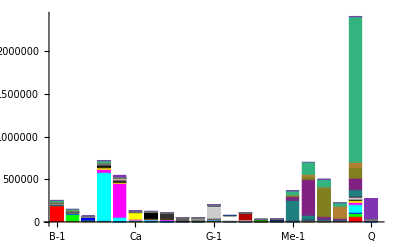

```mathematica
cited21Barchart=StackedBarChart[citingcited21Data,BarLabels->ClNames21,BarStyle->colors21]
```

```mathematica
StackedBarChart[citingcited21Data,BarLabels->ClNames21,BarStyle->colors21]
```

-Graphics-

```mathematica
ClNames21
```

{B-1,B-2,B-3,C-1,C-2,Ca,Cp,E-1,E-2,E-3,G-1,G-2,I-1,I-2,M,Me-1,Me-2,Me-3,Me-4,Mo,Q}

```mathematica
ClJNames21={"動植","農学","水産","化学","物性","分析","応化","金属","機械","化工","気象","地球","電子","数理","数学","臨床1","臨床2","神経","獣医","生化","量子"}
```

{動植,農学,水産,化学,物性,分析,応化,金属,機械,化工,気象,地球,電子,数理,数学,臨床1,臨床2,神経,獣医,生化,量子}

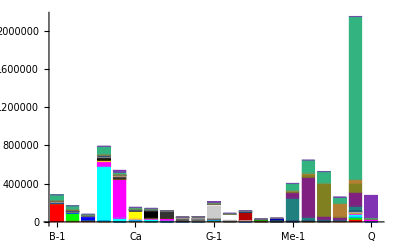

```mathematica
StackedBarChart[citedciting21Data,BarLabels->ClNames21,BarStyle->colors21]
```

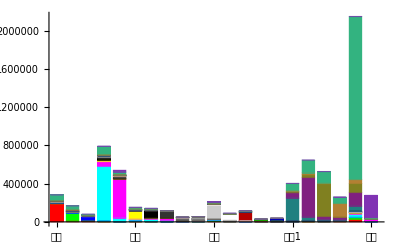

```mathematica
StackedBarChart[citedciting21Data,BarLabels->ClJNames21,BarStyle->colors21]
```

```mathematica
biomedPosition={16,17,18,19,20}
```

{16,17,18,19,20}

```mathematica
exbiomedPosition=Flatten[{Range[1,15],21}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,21}

```mathematica
biomedNames5=ClNames21[[biomedPosition]]
```

{Me-1,Me-2,Me-3,Me-4,Mo}

```mathematica
biomedJNames5={"臨床1","臨床2","神経","獣医","生化"}
```

{臨床1,臨床2,神経,獣医,生化}

```mathematica
colors5=colors21[[biomedPosition]]
```

{CMYKColor[0.75,0,0,0.5],CMYKColor[0,0.75,0,0.5],CMYKColor[0,0,0.75,0.5],RGBColor[0.7,0.5,0.2],RGBColor[0.2,0.7,0.5]}

```mathematica
citedciting5BiomedData=Transpose[Transpose[citedciting21Data[[biomedPosition]]][[biomedPosition]]]
```

{{239889,37875,13273,5445,53062},{55372,414878,32923,28083,142398},{13873,28591,343063,4739,94108},{5175,17796,3549,140776,41456},{78594,135450,123705,67304,1703555}}

```mathematica
citedcitingExBiomedData=Transpose[Transpose[citedciting21Data[[exbiomedPosition]]][[exbiomedPosition]]]
```

{{188946,8916,9838,934,562,1011,394,23,74,163,8033,2100,333,115,218,17},{7157,83165,2329,6428,146,6214,2337,81,23,1618,4885,621,78,42,13,14},{8428,1773,43839,335,91,416,68,12,222,21,6297,1090,26,10,3,15},{692,4926,268,571546,39515,15556,24422,11849,507,7580,3722,1613,479,53,96,744},{337,190,129,50665,403763,4829,7039,24046,3350,2374,3607,4540,4727,1824,2394,25433},{598,4323,219,14115,3592,85268,2261,939,189,1276,2955,628,282,60,9,124},{308,1982,70,20113,4418,2720,77685,3887,1034,2783,598,157,68,23,24,55},{13,59,10,11878,18194,984,3025,67463,2491,1549,309,373,379,287,22,44},{90,42,257,309,3243,202,1033,3095,33686,1878,1704,310,1951,192,982,307},{215,1168,46,5991,1818,1160,2520,1471,1550,30056,2449,284,554,144,106,69},{8191,4795,6357,4643,3100,6240,872,383,1514,3465,137796,10549,555,270,210,2460},{1490,254,788,1219,1222,833,170,294,78,195,8998,58837,26,0,72,605},{319,81,53,508,3916,223,109,520,1761,946,673,132,88752,3325,3283,192},{371,53,83,95,1829,85,51,450,391,316,544,48,3560,20155,618,23},{265,13,12,110,2011,4,19,44,949,115,76,118,3766,529,28792,1293},{11,7,2,1435,19773,213,128,129,291,68,3426,824,366,70,1002,241828}}

```mathematica
citedcitingExBiomedDataZeroSelf=Transpose[Transpose[citedciting21DataZeroSelf[[exbiomedPosition]]][[exbiomedPosition]]]
```

{{0,8916,9838,934,562,1011,394,23,74,163,8033,2100,333,115,218,17},{7157,0,2329,6428,146,6214,2337,81,23,1618,4885,621,78,42,13,14},{8428,1773,0,335,91,416,68,12,222,21,6297,1090,26,10,3,15},{692,4926,268,0,39515,15556,24422,11849,507,7580,3722,1613,479,53,96,744},{337,190,129,50665,0,4829,7039,24046,3350,2374,3607,4540,4727,1824,2394,25433},{598,4323,219,14115,3592,0,2261,939,189,1276,2955,628,282,60,9,124},{308,1982,70,20113,4418,2720,0,3887,1034,2783,598,157,68,23,24,55},{13,59,10,11878,18194,984,3025,0,2491,1549,309,373,379,287,22,44},{90,42,257,309,3243,202,1033,3095,0,1878,1704,310,1951,192,982,307},{215,1168,46,5991,1818,1160,2520,1471,1550,0,2449,284,554,144,106,69},{8191,4795,6357,4643,3100,6240,872,383,1514,3465,0,10549,555,270,210,2460},{1490,254,788,1219,1222,833,170,294,78,195,8998,0,26,0,72,605},{319,81,53,508,3916,223,109,520,1761,946,673,132,0,3325,3283,192},{371,53,83,95,1829,85,51,450,391,316,544,48,3560,0,618,23},{265,13,12,110,2011,4,19,44,949,115,76,118,3766,529,0,1293},{11,7,2,1435,19773,213,128,129,291,68,3426,824,366,70,1002,0}}

```mathematica
citingcitedExBiomedData=Transpose[citedcitingExBiomedData];
```

```mathematica
citingcitedExBiomedDataZeroSelf=Transpose[citedcitingExBiomedDataZeroSelf];
```

```mathematica
citingcited5BiomedData=Transpose[citedciting5BiomedData]
```

{{239889,55372,13873,5175,78594},{37875,414878,28591,17796,135450},{13273,32923,343063,3549,123705},{5445,28083,4739,140776,67304},{53062,142398,94108,41456,1703555}}

```mathematica
citedciting5BiomedDataZeroSelf=ReplacePart[citedciting5BiomedData,{{1,1}->0,{2,2}->0,{3,3}->0,{4,4}->0,{5,5}->0}]
```

{{0,37875,13273,5445,53062},{55372,0,32923,28083,142398},{13873,28591,0,4739,94108},{5175,17796,3549,0,41456},{78594,135450,123705,67304,0}}

```mathematica
citingcited5BiomedDataZeroSelf=ReplacePart[citingcited5BiomedData,{{1,1}->0,{2,2}->0,{3,3}->0,{4,4}->0,{5,5}->0}]
```

{{0,55372,13873,5175,78594},{37875,0,28591,17796,135450},{13273,32923,0,3549,123705},{5445,28083,4739,0,67304},{53062,142398,94108,41456,0}}

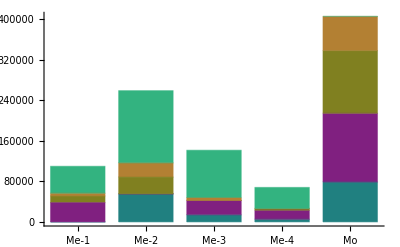

```mathematica
StackedBarChart[citingcited5BiomedDataZeroSelf,BarLabels->biomedNames5,BarStyle->colors5]
```

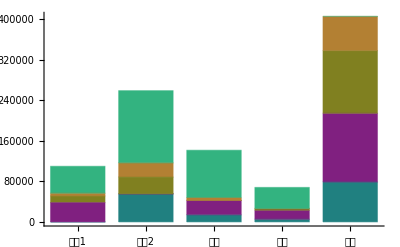

```mathematica
StackedBarChart[citingcited5BiomedDataZeroSelf,BarLabels->biomedJNames5,BarStyle->colors5]
```

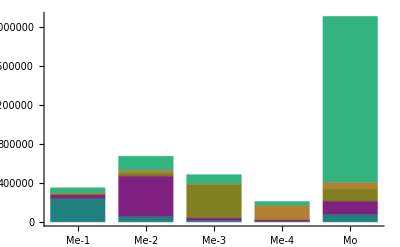

```mathematica
StackedBarChart[citingcited5BiomedData,BarLabels->biomedNames5,BarStyle->colors5]
```

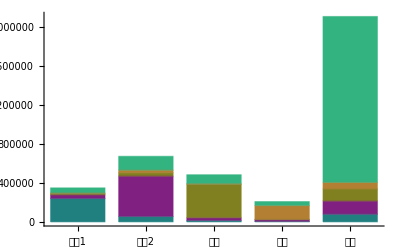

```mathematica
StackedBarChart[citingcited5BiomedData,BarLabels->biomedJNames5,BarStyle->colors5]
```

```mathematica
citedBiomed5DataZeroSelf=citedciting21DataZeroSelf[[biomedPosition]]
```

{{212,1303,167,2535,1389,894,4630,863,616,65,691,110,1800,204,29,0,37875,13273,5445,53062,199},{635,8719,366,3457,269,2978,1267,18,98,93,4516,84,1061,789,9,55372,0,32923,28083,142398,16},{1918,1355,1723,4254,765,1192,627,11,496,35,1095,173,2825,178,64,13873,28591,0,4739,94108,58},{2735,6834,1236,1970,375,789,792,9,11,10,680,125,91,49,22,5175,17796,3549,0,41456,0},{60318,38548,12174,88621,30036,20303,11894,1596,581,732,17038,8527,5138,740,402,78594,135450,123705,67304,0,4115}}

```mathematica
citedTotalOthersZeroSelf=Map[Tr[#[[exbiomedPosition]]]&,citedBiomed5DataZeroSelf]
```

{15707,24375,16769,15728,300763}

```mathematica
citedciting5BiomedDataANDTotalOthersZeroSelf=Transpose[Append[Transpose[citedciting5BiomedDataZeroSelf],citedTotalOthersZeroSelf]]
```

{{0,37875,13273,5445,53062,15707},{55372,0,32923,28083,142398,24375},{13873,28591,0,4739,94108,16769},{5175,17796,3549,0,41456,15728},{78594,135450,123705,67304,0,300763}}

```mathematica
citingBiomed5DataZeroSelf=citingcited21DataZeroSelf[[biomedPosition]]
```

{{144,969,117,959,1146,418,2092,271,487,53,384,99,1230,260,42,0,55372,13873,5175,78594,225},{293,4423,65,422,99,1369,425,11,59,25,2227,14,593,848,22,37875,0,28591,17796,135450,13},{1756,1018,1143,1068,751,860,361,10,442,17,425,24,1623,183,32,13273,32923,0,3549,123705,12},{2839,6449,1113,858,269,464,463,4,16,12,570,38,60,62,17,5445,28083,4739,0,67304,3},{24853,19638,4188,32565,5057,8288,4814,200,210,104,7590,1506,1513,528,157,53062,142398,94108,41456,0,1099}}

```mathematica
citingTotalOthersZeroSelf=Map[Tr[#[[exbiomedPosition]]]&,citingBiomed5DataZeroSelf]
```

{8896,10908,9725,13237,112310}

```mathematica
citingcited5BiomedDataANDTotalOthersZeroSelf=Transpose[Append[Transpose[citingcited5BiomedDataZeroSelf],citingTotalOthersZeroSelf]]
```

{{0,55372,13873,5175,78594,8896},{37875,0,28591,17796,135450,10908},{13273,32923,0,3549,123705,9725},{5445,28083,4739,0,67304,13237},{53062,142398,94108,41456,0,112310}}

```mathematica
colors6=colors21[[Flatten[{biomedPosition,21}]]]
```

{CMYKColor[0.75,0,0,0.5],CMYKColor[0,0.75,0,0.5],CMYKColor[0,0,0.75,0.5],RGBColor[0.7,0.5,0.2],RGBColor[0.2,0.7,0.5],RGBColor[0.5,0.2,0.7]}

```mathematica
biomedJNames5
```

{臨床1,臨床2,神経,獣医,生化}

```mathematica
biomedJNamesANDOther=Flatten[{biomedJNames5,"他"}]
```

{臨床1,臨床2,神経,獣医,生化,他}

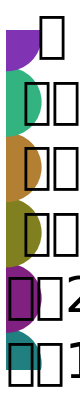

```mathematica
Graphics[Table[{PointSize[0.5],colors6[[n]],Point[{0,n}],RGBColor[0,0,0],Text[Style[biomedJNamesANDOther[[n]],FontSize->50],{1,n}]},{n,6}]]
```

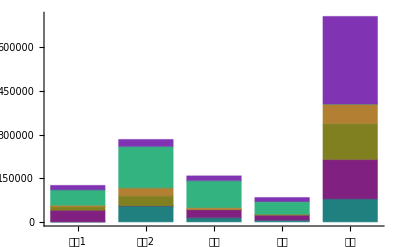

```mathematica
citedbarchart=StackedBarChart[Transpose[citedciting5BiomedDataANDTotalOthersZeroSelf],BarStyle->colors6,BarLabels->biomedJNamesANDOther]
```

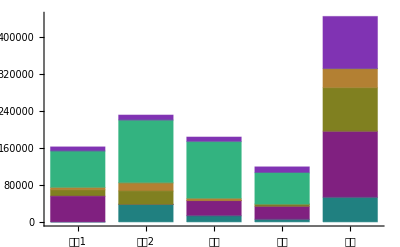

```mathematica
citingbarchart=StackedBarChart[Transpose[citingcited5BiomedDataANDTotalOthersZeroSelf],BarStyle->colors6,BarLabels->biomedJNamesANDOther]
```

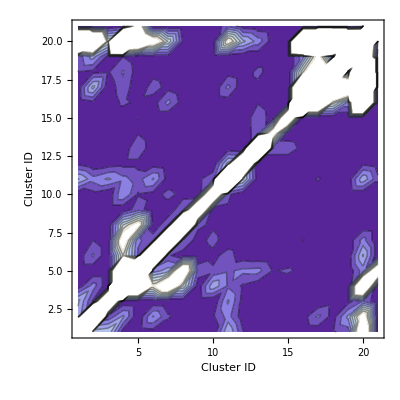

```mathematica
lcp21=ListContourPlot[citedciting21Data,FrameLabel->{"Cluster ID","Cluster ID"}]
```

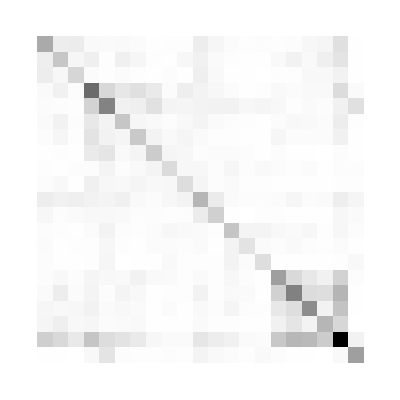

```mathematica
ArrayPlot[Sqrt[citedciting21Data]]
```

```mathematica
TableForm[(citingcited21Data=Transpose[citedciting21Data]),TableHeadings->{NosANDClNames21,NosANDClNames21}]
```

| {1,B-1} | {2,B-2} | {3,B-3} | {4,C-1} | {5,C-2} | {6,Ca} | {7,Cp} | {8,E-1} | {9,E-2} | {10,E-3} | {11,G-1} | {12,G-2} | {13,I-1} | {14,I-2} | {15,M} | {16,Me-1} | {17,Me-2} | {18,Me-3} | {19,Me-4} | {20,Mo} | {21,Q}
{1,B-1} | 188946 | 7157 | 8428 | 692 | 337 | 598 | 308 | 13 | 90 | 215 | 8191 | 1490 | 319 | 371 | 265 | 212 | 635 | 1918 | 2735 | 60318 | 11
{2,B-2} | 8916 | 83165 | 1773 | 4926 | 190 | 4323 | 1982 | 59 | 42 | 1168 | 4795 | 254 | 81 | 53 | 13 | 1303 | 8719 | 1355 | 6834 | 38548 | 7
{3,B-3} | 9838 | 2329 | 43839 | 268 | 129 | 219 | 70 | 10 | 257 | 46 | 6357 | 788 | 53 | 83 | 12 | 167 | 366 | 1723 | 1236 | 12174 | 2
{4,C-1} | 934 | 6428 | 335 | 571546 | 50665 | 14115 | 20113 | 11878 | 309 | 5991 | 4643 | 1219 | 508 | 95 | 110 | 2535 | 3457 | 4254 | 1970 | 88621 | 1435
{5,C-2} | 562 | 146 | 91 | 39515 | 403763 | 3592 | 4418 | 18194 | 3243 | 1818 | 3100 | 1222 | 3916 | 1829 | 2011 | 1389 | 269 | 765 | 375 | 30036 | 19773
{6,Ca} | 1011 | 6214 | 416 | 15556 | 4829 | 85268 | 2720 | 984 | 202 | 1160 | 6240 | 833 | 223 | 85 | 4 | 894 | 2978 | 1192 | 789 | 20303 | 213
{7,Cp} | 394 | 2337 | 68 | 24422 | 7039 | 2261 | 77685 | 3025 | 1033 | 2520 | 872 | 170 | 109 | 51 | 19 | 4630 | 1267 | 627 | 792 | 11894 | 128
{8,E-1} | 23 | 81 | 12 | 11849 | 24046 | 939 | 3887 | 67463 | 3095 | 1471 | 383 | 294 | 520 | 450 | 44 | 863 | 18 | 11 | 9 | 1596 | 129
{9,E-2} | 74 | 23 | 222 | 507 | 3350 | 189 | 1034 | 2491 | 33686 | 1550 | 1514 | 78 | 1761 | 391 | 949 | 616 | 98 | 496 | 11 | 581 | 291
{10,E-3} | 163 | 1618 | 21 | 7580 | 2374 | 1276 | 2783 | 1549 | 1878 | 30056 | 3465 | 195 | 946 | 316 | 115 | 65 | 93 | 35 | 10 | 732 | 68
{11,G-1} | 8033 | 4885 | 6297 | 3722 | 3607 | 2955 | 598 | 309 | 1704 | 2449 | 137796 | 8998 | 673 | 544 | 76 | 691 | 4516 | 1095 | 680 | 17038 | 3426
{12,G-2} | 2100 | 621 | 1090 | 1613 | 4540 | 628 | 157 | 373 | 310 | 284 | 10549 | 58837 | 132 | 48 | 118 | 110 | 84 | 173 | 125 | 8527 | 824
{13,I-1} | 333 | 78 | 26 | 479 | 4727 | 282 | 68 | 379 | 1951 | 554 | 555 | 26 | 88752 | 3560 | 3766 | 1800 | 1061 | 2825 | 91 | 5138 | 366
{14,I-2} | 115 | 42 | 10 | 53 | 1824 | 60 | 23 | 287 | 192 | 144 | 270 | 0 | 3325 | 20155 | 529 | 204 | 789 | 178 | 49 | 740 | 70
{15,M} | 218 | 13 | 3 | 96 | 2394 | 9 | 24 | 22 | 982 | 106 | 210 | 72 | 3283 | 618 | 28792 | 29 | 9 | 64 | 22 | 402 | 1002
{16,Me-1} | 144 | 969 | 117 | 959 | 1146 | 418 | 2092 | 271 | 487 | 53 | 384 | 99 | 1230 | 260 | 42 | 239889 | 55372 | 13873 | 5175 | 78594 | 225
{17,Me-2} | 293 | 4423 | 65 | 422 | 99 | 1369 | 425 | 11 | 59 | 25 | 2227 | 14 | 593 | 848 | 22 | 37875 | 414878 | 28591 | 17796 | 135450 | 13
{18,Me-3} | 1756 | 1018 | 1143 | 1068 | 751 | 860 | 361 | 10 | 442 | 17 | 425 | 24 | 1623 | 183 | 32 | 13273 | 32923 | 343063 | 3549 | 123705 | 12
{19,Me-4} | 2839 | 6449 | 1113 | 858 | 269 | 464 | 463 | 4 | 16 | 12 | 570 | 38 | 60 | 62 | 17 | 5445 | 28083 | 4739 | 140776 | 67304 | 3
{20,Mo} | 24853 | 19638 | 4188 | 32565 | 5057 | 8288 | 4814 | 200 | 210 | 104 | 7590 | 1506 | 1513 | 528 | 157 | 53062 | 142398 | 94108 | 41456 | 1703555 | 1099
{21,Q} | 17 | 14 | 15 | 744 | 25433 | 124 | 55 | 44 | 307 | 69 | 2460 | 605 | 192 | 23 | 1293 | 199 | 16 | 58 | 0 | 4115 | 241828

```mathematica
citingcited21DatawithClNames=Table[Prepend[citingcited21Data[[n]],ClNames21[[n]]],{n,numClusters}];
```

```mathematica
citedParciting21=citedciting21Data/Transpose[citedciting21Data//N]/.{ComplexInfinity->Infinity,Indeterminate->0};
```

Power::infy: 無限式1/0.が見付かりました．

```mathematica
TableForm[Round[citedParciting21,0.01],TableHeadings->{NosANDClNames21,NosANDClNames21}]
```

| {1,B-1} | {2,B-2} | {3,B-3} | {4,C-1} | {5,C-2} | {6,Ca} | {7,Cp} | {8,E-1} | {9,E-2} | {10,E-3} | {11,G-1} | {12,G-2} | {13,I-1} | {14,I-2} | {15,M} | {16,Me-1} | {17,Me-2} | {18,Me-3} | {19,Me-4} | {20,Mo} | {21,Q}
{1,B-1} | 1. | 1.25 | 1.17 | 1.35 | 1.67 | 1.69 | 1.28 | 1.77 | 0.82 | 0.76 | 0.98 | 1.41 | 1.04 | 0.31 | 0.82 | 0.68 | 0.46 | 0.92 | 1.04 | 0.41 | 1.55
{2,B-2} | 0.8 | 1. | 1.31 | 1.3 | 0.77 | 1.44 | 1.18 | 1.37 | 0.55 | 1.39 | 1.02 | 2.44 | 0.96 | 0.79 | 1. | 0.74 | 0.51 | 0.75 | 0.94 | 0.51 | 2.
{3,B-3} | 0.86 | 0.76 | 1. | 1.25 | 0.71 | 1.9 | 0.97 | 1.2 | 0.86 | 0.46 | 0.99 | 1.38 | 0.49 | 0.12 | 0.25 | 0.7 | 0.18 | 0.66 | 0.9 | 0.34 | 7.5
{4,C-1} | 0.74 | 0.77 | 0.8 | 1. | 0.78 | 1.1 | 1.21 | 1. | 1.64 | 1.27 | 0.8 | 1.32 | 0.94 | 0.56 | 0.87 | 0.38 | 0.12 | 0.25 | 0.44 | 0.37 | 0.52
{5,C-2} | 0.6 | 1.3 | 1.42 | 1.28 | 1. | 1.34 | 1.59 | 1.32 | 1.03 | 1.31 | 1.16 | 3.72 | 1.21 | 1. | 1.19 | 0.83 | 0.37 | 0.98 | 0.72 | 0.17 | 1.29
{6,Ca} | 0.59 | 0.7 | 0.53 | 0.91 | 0.74 | 1. | 0.83 | 0.95 | 0.94 | 1.1 | 0.47 | 0.75 | 1.26 | 0.71 | 2.25 | 0.47 | 0.46 | 0.72 | 0.59 | 0.41 | 0.58
{7,Cp} | 0.78 | 0.85 | 1.03 | 0.82 | 0.63 | 1.2 | 1. | 1.28 | 1. | 1.1 | 0.69 | 0.92 | 0.62 | 0.45 | 1.26 | 0.45 | 0.34 | 0.58 | 0.58 | 0.4 | 0.43
{8,E-1} | 0.57 | 0.73 | 0.83 | 1. | 0.76 | 1.05 | 0.78 | 1. | 0.8 | 1.05 | 0.81 | 1.27 | 0.73 | 0.64 | 0.5 | 0.31 | 0.61 | 0.91 | 0.44 | 0.13 | 0.34
{9,E-2} | 1.22 | 1.83 | 1.16 | 0.61 | 0.97 | 1.07 | 1. | 1.24 | 1. | 1.21 | 1.13 | 3.97 | 1.11 | 0.49 | 1.03 | 0.79 | 0.6 | 0.89 | 1.45 | 0.36 | 1.05
{10,E-3} | 1.32 | 0.72 | 2.19 | 0.79 | 0.77 | 0.91 | 0.91 | 0.95 | 0.83 | 1. | 0.71 | 1.46 | 0.59 | 0.46 | 0.92 | 0.82 | 0.27 | 0.49 | 1.2 | 0.14 | 1.01
{11,G-1} | 1.02 | 0.98 | 1.01 | 1.25 | 0.86 | 2.11 | 1.46 | 1.24 | 0.89 | 1.41 | 1. | 1.17 | 0.82 | 0.5 | 2.76 | 0.56 | 0.49 | 0.39 | 0.84 | 0.45 | 0.72
{12,G-2} | 0.71 | 0.41 | 0.72 | 0.76 | 0.27 | 1.33 | 1.08 | 0.79 | 0.25 | 0.69 | 0.85 | 1. | 0.2 | 0. | 0.61 | 0.9 | 0.17 | 0.14 | 0.3 | 0.18 | 0.73
{13,I-1} | 0.96 | 1.04 | 2.04 | 1.06 | 0.83 | 0.79 | 1.6 | 1.37 | 0.9 | 1.71 | 1.21 | 5.08 | 1. | 0.93 | 0.87 | 0.68 | 0.56 | 0.57 | 0.66 | 0.29 | 0.52
{14,I-2} | 3.23 | 1.26 | 8.3 | 1.79 | 1. | 1.42 | 2.22 | 1.57 | 2.04 | 2.19 | 2.01 | ∞ | 1.07 | 1. | 1.17 | 1.27 | 1.07 | 1.03 | 1.27 | 0.71 | 0.33
{15,M} | 1.22 | 1. | 4. | 1.15 | 0.84 | 0.44 | 0.79 | 2. | 0.97 | 1.08 | 0.36 | 1.64 | 1.15 | 0.86 | 1. | 1.45 | 2.44 | 0.5 | 0.77 | 0.39 | 1.29
{16,Me-1} | 1.47 | 1.34 | 1.43 | 2.64 | 1.21 | 2.14 | 2.21 | 3.18 | 1.26 | 1.23 | 1.8 | 1.11 | 1.46 | 0.78 | 0.69 | 1. | 0.68 | 0.96 | 1.05 | 0.68 | 0.88
{17,Me-2} | 2.17 | 1.97 | 5.63 | 8.19 | 2.72 | 2.18 | 2.98 | 1.64 | 1.66 | 3.72 | 2.03 | 6. | 1.79 | 0.93 | 0.41 | 1.46 | 1. | 1.15 | 1.58 | 1.05 | 1.23
{18,Me-3} | 1.09 | 1.33 | 1.51 | 3.98 | 1.02 | 1.39 | 1.74 | 1.1 | 1.12 | 2.06 | 2.58 | 7.21 | 1.74 | 0.97 | 2. | 1.05 | 0.87 | 1. | 1.34 | 0.76 | 4.83
{19,Me-4} | 0.96 | 1.06 | 1.11 | 2.3 | 1.39 | 1.7 | 1.71 | 2.25 | 0.69 | 0.83 | 1.19 | 3.29 | 1.52 | 0.79 | 1.29 | 0.95 | 0.63 | 0.75 | 1. | 0.62 | 0.
{20,Mo} | 2.43 | 1.96 | 2.91 | 2.72 | 5.94 | 2.45 | 2.47 | 7.98 | 2.77 | 7.04 | 2.24 | 5.66 | 3.4 | 1.4 | 2.56 | 1.48 | 0.95 | 1.31 | 1.62 | 1. | 3.74
{21,Q} | 0.65 | 0.5 | 0.13 | 1.93 | 0.78 | 1.72 | 2.33 | 2.93 | 0.95 | 0.99 | 1.39 | 1.36 | 1.91 | 3.04 | 0.77 | 1.13 | 0.81 | 0.21 | ∞ | 0.27 | 1.

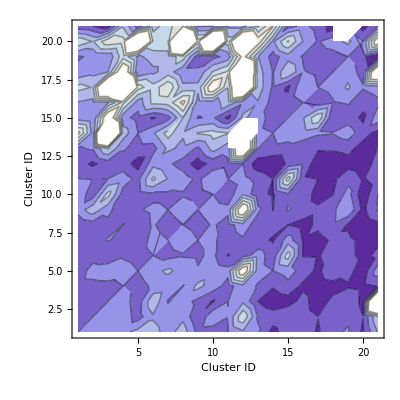

```mathematica
citedParcitingplot21=ListContourPlot[citedParciting21,FrameLabel->{"Cluster ID","Cluster ID"}]
```

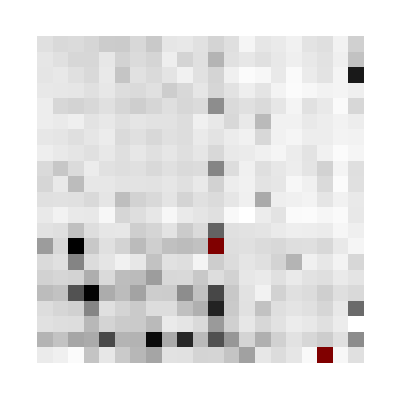

```mathematica
ArrayPlot[citedParciting21]
```

```mathematica
totalCited21=Map[Tr[#]&,citedciting21Data]
```

{251562,147648,69272,719440,546569,128237,124080,107576,50495,49812,202596,76762,109812,30553,38386,365251,698029,501143,224480,2409371,270925}

```mathematica
totalCiting21=Map[Tr[#]&,citingcited21Data]
```

{283249,168506,79966,791161,540027,152114,141343,117183,49912,55338,210092,91243,116817,29059,38370,401799,645498,526238,259584,2146889,277611}

```mathematica
totalCitedPartotalCiting21=totalCited21/totalCiting21//N
```

{0.88813,0.876218,0.866268,0.909347,1.01211,0.843032,0.877864,0.918017,1.01168,0.900141,0.96432,0.841292,0.940034,1.05141,1.00042,0.909039,1.08138,0.952312,0.864768,1.12226,0.975916}

## Totalcited / totalciting

```mathematica
totalCited21
```

{251562,147648,69272,719440,546569,128237,124080,107576,50495,49812,202596,76762,109812,30553,38386,365251,698029,501143,224480,2409371,270925}

```mathematica
grandTotalCited21=Tr[totalCited21]
```

7121999

```mathematica
totalCiting21
```

{283249,168506,79966,791161,540027,152114,141343,117183,49912,55338,210092,91243,116817,29059,38370,401799,645498,526238,259584,2146889,277611}

```mathematica
grandTotalCiting21=Tr[totalCiting21]
```

7121999

```mathematica
totalCited21DropSelf=(Map[Tr[#]&,citedciting21Data]-Tr[citedciting21Data,List])
```

{62616,64483,25433,147894,142806,42969,46395,40113,16809,19756,64800,17925,21060,10398,9594,125362,283151,158080,83704,705816,29097}

```mathematica
grandTotalCited21DropSelf=Tr[totalCited21DropSelf]
```

2118261

```mathematica
grandTotalCited21DropSelf/grandTotalCited21//N
```

0.297425

```mathematica
TableForm[totalCitedPartotalCiting21,TableHeadings->{NosANDClNames21}]
```

{1,B-1} | 0.88813
{2,B-2} | 0.876218
{3,B-3} | 0.866268
{4,C-1} | 0.909347
{5,C-2} | 1.01211
{6,Ca} | 0.843032
{7,Cp} | 0.877864
{8,E-1} | 0.918017
{9,E-2} | 1.01168
{10,E-3} | 0.900141
{11,G-1} | 0.96432
{12,G-2} | 0.841292
{13,I-1} | 0.940034
{14,I-2} | 1.05141
{15,M} | 1.00042
{16,Me-1} | 0.909039
{17,Me-2} | 1.08138
{18,Me-3} | 0.952312
{19,Me-4} | 0.864768
{20,Mo} | 1.12226
{21,Q} | 0.975916

```mathematica
totalCitedPartotalCiting21DropSelf=citedFromAllOthers/citingToAllOthers//N
```

{0.663987,0.755592,0.703989,0.673424,1.04801,0.642806,0.728816,0.806778,1.03593,0.781426,0.896315,0.553138,0.750401,1.16779,1.00167,0.77427,1.22778,0.863,0.704532,1.59206,0.813151}

```mathematica
TableForm[Round[citedFromAllOthers/citingToAllOthers//N,0.01],TableHeadings->{NosANDClNames21}]
```

{1,B-1} | 0.66
{2,B-2} | 0.76
{3,B-3} | 0.7
{4,C-1} | 0.67
{5,C-2} | 1.05
{6,Ca} | 0.64
{7,Cp} | 0.73
{8,E-1} | 0.81
{9,E-2} | 1.04
{10,E-3} | 0.78
{11,G-1} | 0.9
{12,G-2} | 0.55
{13,I-1} | 0.75
{14,I-2} | 1.17
{15,M} | 1.
{16,Me-1} | 0.77
{17,Me-2} | 1.23
{18,Me-3} | 0.86
{19,Me-4} | 0.7
{20,Mo} | 1.59
{21,Q} | 0.81

## Issues

### Issues

```mathematica
ClNamesANDIssues21//Length
```

21

```mathematica
ClNamesANDIssues21//TableForm
```

B-1 | 152543.
B-2 | 122403.
B-3 | 57635.
C-1 | 345502.
C-2 | 384818.
Ca | 81244.
Cp | 93381.
E-1 | 131554.
E-2 | 69050.
E-3 | 75438.
G-1 | 144004.
G-2 | 55707.
I-1 | 145987.
I-2 | 57812.
M | 77345.
Me-1 | 243966.
Me-2 | 296555.
Me-3 | 201248.
Me-4 | 144683.
Mo | 591227.
Q | 110448.

### Cited / Issues

```mathematica
totalCited21
```

{251562,147648,69272,719440,546569,128237,124080,107576,50495,49812,202596,76762,109812,30553,38386,365251,698029,501143,224480,2409371,270925}

```mathematica
(citedParIssues = Table[
{ClNamesANDIssues21[[n]][[1]],
totalCited21[[n]]/ClNamesANDIssues21[[n,2]]},
{n,21}])//TableForm
```

B-1 | 1.64912
B-2 | 1.20624
B-3 | 1.20191
C-1 | 2.0823
C-2 | 1.42033
Ca | 1.57842
Cp | 1.32875
E-1 | 0.817733
E-2 | 0.731282
E-3 | 0.660304
G-1 | 1.40688
G-2 | 1.37796
I-1 | 0.752204
I-2 | 0.528489
M | 0.496296
Me-1 | 1.49714
Me-2 | 2.35379
Me-3 | 2.49018
Me-4 | 1.55153
Mo | 4.0752
Q | 2.45296

```mathematica
(citedParIssuesDropSelf = Table[
{ClNamesANDIssues21[[n]][[1]],
totalCited21DropSelf[[n]]/ClNamesANDIssues21[[n,2]]},
{n,21}])
```

{{B-1,0.410481},{B-2,0.526809},{B-3,0.441277},{C-1,0.428055},{C-2,0.3711},{Ca,0.528888},{Cp,0.496836},{E-1,0.304917},{E-2,0.243432},{E-3,0.261884},{G-1,0.449988},{G-2,0.321773},{I-1,0.144259},{I-2,0.179859},{M,0.124042},{Me-1,0.51385},{Me-2,0.954801},{Me-3,0.785498},{Me-4,0.578534},{Mo,1.19382},{Q,0.263445}}

```mathematica
Map[{#[[1]],Round[#[[2]],0.01]}&,citedParIssuesDropSelf]//TableForm
```

B-1 | 0.41
B-2 | 0.53
B-3 | 0.44
C-1 | 0.43
C-2 | 0.37
Ca | 0.53
Cp | 0.5
E-1 | 0.3
E-2 | 0.24
E-3 | 0.26
G-1 | 0.45
G-2 | 0.32
I-1 | 0.14
I-2 | 0.18
M | 0.12
Me-1 | 0.51
Me-2 | 0.95
Me-3 | 0.79
Me-4 | 0.58
Mo | 1.19
Q | 0.26

## SpearmanRankCorrelation to citedParIssuesDropSelf

```mathematica
citedParIssuesDropSelf
```

{{B-1,0.410481},{B-2,0.526809},{B-3,0.441277},{C-1,0.428055},{C-2,0.3711},{Ca,0.528888},{Cp,0.496836},{E-1,0.304917},{E-2,0.243432},{E-3,0.261884},{G-1,0.449988},{G-2,0.321773},{I-1,0.144259},{I-2,0.179859},{M,0.124042},{Me-1,0.51385},{Me-2,0.954801},{Me-3,0.785498},{Me-4,0.578534},{Mo,1.19382},{Q,0.263445}}

### totalCitedPartotalCiting21DropSelf vs. citedParIssuesDropSelf

```mathematica
totalCitedPartotalCiting21DropSelf
```

{0.663987,0.755592,0.703989,0.673424,1.04801,0.642806,0.728816,0.806778,1.03593,0.781426,0.896315,0.553138,0.750401,1.16779,1.00167,0.77427,1.22778,0.863,0.704532,1.59206,0.813151}

```mathematica
SpearmanRankCorrelation[totalCitedPartotalCiting21DropSelf,Map[#[[2]]&,citedParIssuesDropSelf]]//N
```

-0.0350649

### totalCited21DropSelf vs. citedParIssuesDropSelf

```mathematica
totalCited21DropSelf
```

{62616,64483,25433,147894,142806,42969,46395,40113,16809,19756,64800,17925,21060,10398,9594,125362,283151,158080,83704,705816,29097}

```mathematica
SpearmanRankCorrelation[totalCited21DropSelf,Map[#[[2]]&,citedParIssuesDropSelf]]//N
```

0.82987

### ClNamesANDIssues21 vs. citedParIssuesDropSelf

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDIssues21],Map[#[[2]]&,citedParIssuesDropSelf]]//N
```

0.501299

### ClNamesANDSizes21 vs. citedParIssuesDropSelf

```mathematica
ClNamesANDSizes21
```

{{B-1,427},{B-2,243},{B-3,148},{C-1,315},{C-2,248},{Ca,130},{Cp,163},{E-1,209},{E-2,187},{E-3,173},{G-1,308},{G-2,165},{I-1,435},{I-2,182},{M,216},{Me-1,416},{Me-2,519},{Me-3,374},{Me-4,277},{Mo,751},{Q,78}}

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDSizes21],Map[#[[2]]&,citedParIssuesDropSelf]]//N
```

0.350649

## Self [cited | citing] ratio

```mathematica
TableForm[selfcitingRatio21=selfCiting21/totalCiting21//N,TableHeadings->{NosANDClNames21}]
```

{1,B-1} | 0.667067
{2,B-2} | 0.493543
{3,B-3} | 0.54822
{4,C-1} | 0.722414
{5,C-2} | 0.747672
{6,Ca} | 0.560553
{7,Cp} | 0.54962
{8,E-1} | 0.575706
{9,E-2} | 0.674908
{10,E-3} | 0.543135
{11,G-1} | 0.655884
{12,G-2} | 0.644839
{13,I-1} | 0.759752
{14,I-2} | 0.693589
{15,M} | 0.750378
{16,Me-1} | 0.597037
{17,Me-2} | 0.642725
{18,Me-3} | 0.651916
{19,Me-4} | 0.542314
{20,Mo} | 0.793499
{21,Q} | 0.871104

```mathematica
TableForm[selfcitedRatio21=selfCited21/totalCited21//N,TableHeadings->{NosANDClNames21}]
```

{1,B-1} | 0.751091
{2,B-2} | 0.563265
{3,B-3} | 0.632853
{4,C-1} | 0.794432
{5,C-2} | 0.738723
{6,Ca} | 0.664925
{7,Cp} | 0.626088
{8,E-1} | 0.627119
{9,E-2} | 0.667116
{10,E-3} | 0.603389
{11,G-1} | 0.680152
{12,G-2} | 0.766486
{13,I-1} | 0.808218
{14,I-2} | 0.659673
{15,M} | 0.750065
{16,Me-1} | 0.656778
{17,Me-2} | 0.594356
{18,Me-3} | 0.684561
{19,Me-4} | 0.62712
{20,Mo} | 0.707054
{21,Q} | 0.892601

## Cited / citing 21 diagonal standerdize table

対角要素を1/2 にするべき(まだしていない)、でも、影響の排除の仕方としてはどっちでもよい。

```mathematica
diagonalStanderdize[citedciting21Data+citingcited21Data]//TableForm
```

1. | 0.0641103 | 0.100349 | 0.00247398 | 0.00162741 | 0.00633817 | 0.00289714 | 0.00015943 | 0.00102783 | 0.002508 | 0.0502737 | 0.0170243 | 0.00251744 | 0.00393773 | 0.00327425 | 0.000836076 | 0.00165725 | 0.00721528 | 0.0170885 | 0.0750611 | 0.0000654947
0.0641103 | 1. | 0.0339676 | 0.0260389 | 0.000916802 | 0.0625639 | 0.0268667 | 0.000934534 | 0.000614028 | 0.0278622 | 0.0452123 | 0.00625435 | 0.000925354 | 0.0011602 | 0.000265667 | 0.00804272 | 0.0353754 | 0.00702442 | 0.0613807 | 0.077293 | 0.0000740399
0.100349 | 0.0339676 | 1. | 0.00190472 | 0.000826797 | 0.00519302 | 0.00118236 | 0.000202269 | 0.00623233 | 0.000922888 | 0.0814046 | 0.0184889 | 0.000633254 | 0.00156434 | 0.000211103 | 0.00138469 | 0.00159793 | 0.011685 | 0.0149506 | 0.0299363 | 0.0000825535
0.00247398 | 0.0260389 | 0.00190472 | 1. | 0.0938623 | 0.0672022 | 0.105676 | 0.0604163 | 0.00294042 | 0.0517715 | 0.0149036 | 0.00772169 | 0.00219115 | 0.000689469 | 0.000802926 | 0.00471805 | 0.00398294 | 0.00600942 | 0.00498494 | 0.0614071 | 0.00293054
0.00162741 | 0.000916802 | 0.000826797 | 0.0938623 | 1. | 0.0226922 | 0.0323451 | 0.127967 | 0.028266 | 0.0190267 | 0.0142173 | 0.018692 | 0.0228288 | 0.0202472 | 0.0204276 | 0.00407267 | 0.000449567 | 0.00203666 | 0.0013506 | 0.0211568 | 0.0723352
0.00633817 | 0.0625639 | 0.00519302 | 0.0672022 | 0.0226922 | 1. | 0.0306002 | 0.0126772 | 0.00364778 | 0.0240596 | 0.0424141 | 0.0103134 | 0.00290255 | 0.00174885 | 0.000131185 | 0.00458676 | 0.011556 | 0.00599884 | 0.00571826 | 0.0375084 | 0.00117342
0.00289714 | 0.0268667 | 0.00118236 | 0.105676 | 0.0323451 | 0.0306002 | 1. | 0.0477389 | 0.0202031 | 0.0548728 | 0.00710396 | 0.00241838 | 0.00106582 | 0.000935065 | 0.000454605 | 0.0246204 | 0.00471239 | 0.00302602 | 0.00600041 | 0.022964 | 0.000667574
0.00015943 | 0.000934534 | 0.000202269 | 0.0604163 | 0.127967 | 0.0126772 | 0.0477389 | 1. | 0.0585886 | 0.0335335 | 0.0035886 | 0.00529344 | 0.00580909 | 0.0099934 | 0.000748764 | 0.00445702 | 0.0000866712 | 0.0000690191 | 0.0000666985 | 0.0026489 | 0.00067722
0.00102783 | 0.000614028 | 0.00623233 | 0.00294042 | 0.028266 | 0.00364778 | 0.0202031 | 0.0585886 | 1. | 0.0538667 | 0.0236164 | 0.00435764 | 0.0339441 | 0.0111872 | 0.0310021 | 0.00613501 | 0.000664025 | 0.00436276 | 0.00019604 | 0.00165099 | 0.00331278
0.002508 | 0.0278622 | 0.000922888 | 0.0517715 | 0.0190267 | 0.0240596 | 0.0548728 | 0.0335335 | 0.0538667 | 1. | 0.0459481 | 0.00569527 | 0.0145213 | 0.00934482 | 0.0037563 | 0.000694834 | 0.000528355 | 0.000256048 | 0.000169107 | 0.00184728 | 0.000803474
0.0502737 | 0.0452123 | 0.0814046 | 0.0149036 | 0.0142173 | 0.0424141 | 0.00710396 | 0.0035886 | 0.0236164 | 0.0459481 | 1. | 0.108544 | 0.00555215 | 0.00772298 | 0.00227029 | 0.00295634 | 0.0141008 | 0.00349549 | 0.00448743 | 0.0254157 | 0.016122
0.0170243 | 0.00625435 | 0.0184889 | 0.00772169 | 0.018692 | 0.0103134 | 0.00241838 | 0.00529344 | 0.00435764 | 0.00569527 | 0.108544 | 1. | 0.00109323 | 0.000696939 | 0.00230814 | 0.000879601 | 0.000313625 | 0.000693305 | 0.000895505 | 0.0158452 | 0.00598996
0.00251744 | 0.000925354 | 0.000633254 | 0.00219115 | 0.0228288 | 0.00290255 | 0.00106582 | 0.00580909 | 0.0339441 | 0.0145213 | 0.00555215 | 0.00109323 | 1. | 0.0813942 | 0.0697224 | 0.0103829 | 0.00430979 | 0.0127456 | 0.000675451 | 0.00855244 | 0.00190442
0.00393773 | 0.0011602 | 0.00156434 | 0.000689469 | 0.0202472 | 0.00174885 | 0.000935065 | 0.0099934 | 0.0111872 | 0.00934482 | 0.00772298 | 0.000696939 | 0.0813942 | 1. | 0.0238071 | 0.0033365 | 0.00895091 | 0.0021707 | 0.00104193 | 0.00342153 | 0.000666052
0.00327425 | 0.000265667 | 0.000211103 | 0.000802926 | 0.0204276 | 0.000131185 | 0.000454605 | 0.000748764 | 0.0310021 | 0.0037563 | 0.00227029 | 0.00230814 | 0.0697224 | 0.0238071 | 1. | 0.000427157 | 0.000141819 | 0.000482968 | 0.000306291 | 0.00126202 | 0.0137519
0.000836076 | 0.00804272 | 0.00138469 | 0.00471805 | 0.00407267 | 0.00458676 | 0.0246204 | 0.00445702 | 0.00613501 | 0.000694834 | 0.00295634 | 0.000879601 | 0.0103829 | 0.0033365 | 0.000427157 | 1. | 0.147788 | 0.0473134 | 0.0288952 | 0.102974 | 0.000880192
0.00165725 | 0.0353754 | 0.00159793 | 0.00398294 | 0.000449567 | 0.011556 | 0.00471239 | 0.0000866712 | 0.000664025 | 0.000528355 | 0.0141008 | 0.000313625 | 0.00430979 | 0.00895091 | 0.000141819 | 0.147788 | 1. | 0.0815261 | 0.0949204 | 0.165249 | 0.0000457778
0.00721528 | 0.00702442 | 0.011685 | 0.00600942 | 0.00203666 | 0.00599884 | 0.00302602 | 0.0000690191 | 0.00436276 | 0.000256048 | 0.00349549 | 0.000693305 | 0.0127456 | 0.0021707 | 0.000482968 | 0.0473134 | 0.0815261 | 1. | 0.0188568 | 0.142459 | 0.000121514
0.0170885 | 0.0613807 | 0.0149506 | 0.00498494 | 0.0013506 | 0.00571826 | 0.00600041 | 0.0000666985 | 0.00019604 | 0.000169107 | 0.00448743 | 0.000895505 | 0.000675451 | 0.00104193 | 0.000306291 | 0.0288952 | 0.0949204 | 0.0188568 | 1. | 0.111044 | 8.12968×10^-6
0.0750611 | 0.077293 | 0.0299363 | 0.0614071 | 0.0211568 | 0.0375084 | 0.022964 | 0.0026489 | 0.00165099 | 0.00184728 | 0.0254157 | 0.0158452 | 0.00855244 | 0.00342153 | 0.00126202 | 0.102974 | 0.165249 | 0.142459 | 0.111044 | 1. | 0.00406172
0.0000654947 | 0.0000740399 | 0.0000825535 | 0.00293054 | 0.0723352 | 0.00117342 | 0.000667574 | 0.00067722 | 0.00331278 | 0.000803474 | 0.016122 | 0.00598996 | 0.00190442 | 0.000666052 | 0.0137519 | 0.000880192 | 0.0000457778 | 0.000121514 | 8.12968×10^-6 | 0.00406172 | 1.

## Standerdized [cited | citing]

```mathematica
TableForm[N[citedciting21Data/selfCited21],TableHeadings->{NosANDClNames21,NosANDClNames21}];
```

```mathematica
TableForm[Round[N[citedciting21Data/selfCited21],0.001],TableHeadings->{NosANDClNames21,NosANDClNames21}]
```

| {1,B-1} | {2,B-2} | {3,B-3} | {4,C-1} | {5,C-2} | {6,Ca} | {7,Cp} | {8,E-1} | {9,E-2} | {10,E-3} | {11,G-1} | {12,G-2} | {13,I-1} | {14,I-2} | {15,M} | {16,Me-1} | {17,Me-2} | {18,Me-3} | {19,Me-4} | {20,Mo} | {21,Q}
{1,B-1} | 1. | 0.047 | 0.052 | 0.005 | 0.003 | 0.005 | 0.002 | 0. | 0. | 0.001 | 0.043 | 0.011 | 0.002 | 0.001 | 0.001 | 0.001 | 0.002 | 0.009 | 0.015 | 0.132 | 0.
{2,B-2} | 0.086 | 1. | 0.028 | 0.077 | 0.002 | 0.075 | 0.028 | 0.001 | 0. | 0.019 | 0.059 | 0.007 | 0.001 | 0.001 | 0. | 0.012 | 0.053 | 0.012 | 0.078 | 0.236 | 0.
{3,B-3} | 0.192 | 0.04 | 1. | 0.008 | 0.002 | 0.009 | 0.002 | 0. | 0.005 | 0. | 0.144 | 0.025 | 0.001 | 0. | 0. | 0.003 | 0.001 | 0.026 | 0.025 | 0.096 | 0.
{4,C-1} | 0.001 | 0.009 | 0. | 1. | 0.069 | 0.027 | 0.043 | 0.021 | 0.001 | 0.013 | 0.007 | 0.003 | 0.001 | 0. | 0. | 0.002 | 0.001 | 0.002 | 0.002 | 0.057 | 0.001
{5,C-2} | 0.001 | 0. | 0. | 0.125 | 1. | 0.012 | 0.017 | 0.06 | 0.008 | 0.006 | 0.009 | 0.011 | 0.012 | 0.005 | 0.006 | 0.003 | 0. | 0.002 | 0.001 | 0.013 | 0.063
{6,Ca} | 0.007 | 0.051 | 0.003 | 0.166 | 0.042 | 1. | 0.027 | 0.011 | 0.002 | 0.015 | 0.035 | 0.007 | 0.003 | 0.001 | 0. | 0.005 | 0.016 | 0.01 | 0.005 | 0.097 | 0.001
{7,Cp} | 0.004 | 0.026 | 0.001 | 0.259 | 0.057 | 0.035 | 1. | 0.05 | 0.013 | 0.036 | 0.008 | 0.002 | 0.001 | 0. | 0. | 0.027 | 0.005 | 0.005 | 0.006 | 0.062 | 0.001
{8,E-1} | 0. | 0.001 | 0. | 0.176 | 0.27 | 0.015 | 0.045 | 1. | 0.037 | 0.023 | 0.005 | 0.006 | 0.006 | 0.004 | 0. | 0.004 | 0. | 0. | 0. | 0.003 | 0.001
{9,E-2} | 0.003 | 0.001 | 0.008 | 0.009 | 0.096 | 0.006 | 0.031 | 0.092 | 1. | 0.056 | 0.051 | 0.009 | 0.058 | 0.006 | 0.029 | 0.014 | 0.002 | 0.013 | 0. | 0.006 | 0.009
{10,E-3} | 0.007 | 0.039 | 0.002 | 0.199 | 0.06 | 0.039 | 0.084 | 0.049 | 0.052 | 1. | 0.081 | 0.009 | 0.018 | 0.005 | 0.004 | 0.002 | 0.001 | 0.001 | 0. | 0.003 | 0.002
{11,G-1} | 0.059 | 0.035 | 0.046 | 0.034 | 0.022 | 0.045 | 0.006 | 0.003 | 0.011 | 0.025 | 1. | 0.077 | 0.004 | 0.002 | 0.002 | 0.003 | 0.016 | 0.003 | 0.004 | 0.055 | 0.018
{12,G-2} | 0.025 | 0.004 | 0.013 | 0.021 | 0.021 | 0.014 | 0.003 | 0.005 | 0.001 | 0.003 | 0.153 | 1. | 0. | 0. | 0.001 | 0.002 | 0. | 0. | 0.001 | 0.026 | 0.01
{13,I-1} | 0.004 | 0.001 | 0.001 | 0.006 | 0.044 | 0.003 | 0.001 | 0.006 | 0.02 | 0.011 | 0.008 | 0.001 | 1. | 0.037 | 0.037 | 0.014 | 0.007 | 0.018 | 0.001 | 0.017 | 0.002
{14,I-2} | 0.018 | 0.003 | 0.004 | 0.005 | 0.091 | 0.004 | 0.003 | 0.022 | 0.019 | 0.016 | 0.027 | 0.002 | 0.177 | 1. | 0.031 | 0.013 | 0.042 | 0.009 | 0.003 | 0.026 | 0.001
{15,M} | 0.009 | 0. | 0. | 0.004 | 0.07 | 0. | 0.001 | 0.002 | 0.033 | 0.004 | 0.003 | 0.004 | 0.131 | 0.018 | 1. | 0.001 | 0.001 | 0.001 | 0.001 | 0.005 | 0.045
{16,Me-1} | 0.001 | 0.005 | 0.001 | 0.011 | 0.006 | 0.004 | 0.019 | 0.004 | 0.003 | 0. | 0.003 | 0. | 0.008 | 0.001 | 0. | 1. | 0.158 | 0.055 | 0.023 | 0.221 | 0.001
{17,Me-2} | 0.002 | 0.021 | 0.001 | 0.008 | 0.001 | 0.007 | 0.003 | 0. | 0. | 0. | 0.011 | 0. | 0.003 | 0.002 | 0. | 0.133 | 1. | 0.079 | 0.068 | 0.343 | 0.
{18,Me-3} | 0.006 | 0.004 | 0.005 | 0.012 | 0.002 | 0.003 | 0.002 | 0. | 0.001 | 0. | 0.003 | 0.001 | 0.008 | 0.001 | 0. | 0.04 | 0.083 | 1. | 0.014 | 0.274 | 0.
{19,Me-4} | 0.019 | 0.049 | 0.009 | 0.014 | 0.003 | 0.006 | 0.006 | 0. | 0. | 0. | 0.005 | 0.001 | 0.001 | 0. | 0. | 0.037 | 0.126 | 0.025 | 1. | 0.294 | 0.
{20,Mo} | 0.035 | 0.023 | 0.007 | 0.052 | 0.018 | 0.012 | 0.007 | 0.001 | 0. | 0. | 0.01 | 0.005 | 0.003 | 0. | 0. | 0.046 | 0.08 | 0.073 | 0.04 | 1. | 0.002
{21,Q} | 0. | 0. | 0. | 0.006 | 0.082 | 0.001 | 0.001 | 0.001 | 0.001 | 0. | 0.014 | 0.003 | 0.002 | 0. | 0.004 | 0.001 | 0. | 0. | 0. | 0.005 | 1.

```mathematica
TableForm[citingcited21Data/selfCiting21//N,TableHeadings->{NosANDClNames21,NosANDClNames21}];
```

```mathematica
TableForm[Round[citingcited21Data/selfCiting21//N,0.001],TableHeadings->{NosANDClNames21,NosANDClNames21}]
```

| {1,B-1} | {2,B-2} | {3,B-3} | {4,C-1} | {5,C-2} | {6,Ca} | {7,Cp} | {8,E-1} | {9,E-2} | {10,E-3} | {11,G-1} | {12,G-2} | {13,I-1} | {14,I-2} | {15,M} | {16,Me-1} | {17,Me-2} | {18,Me-3} | {19,Me-4} | {20,Mo} | {21,Q}
{1,B-1} | 1. | 0.038 | 0.045 | 0.004 | 0.002 | 0.003 | 0.002 | 0. | 0. | 0.001 | 0.043 | 0.008 | 0.002 | 0.002 | 0.001 | 0.001 | 0.003 | 0.01 | 0.014 | 0.319 | 0.
{2,B-2} | 0.107 | 1. | 0.021 | 0.059 | 0.002 | 0.052 | 0.024 | 0.001 | 0.001 | 0.014 | 0.058 | 0.003 | 0.001 | 0.001 | 0. | 0.016 | 0.105 | 0.016 | 0.082 | 0.464 | 0.
{3,B-3} | 0.224 | 0.053 | 1. | 0.006 | 0.003 | 0.005 | 0.002 | 0. | 0.006 | 0.001 | 0.145 | 0.018 | 0.001 | 0.002 | 0. | 0.004 | 0.008 | 0.039 | 0.028 | 0.278 | 0.
{4,C-1} | 0.002 | 0.011 | 0.001 | 1. | 0.089 | 0.025 | 0.035 | 0.021 | 0.001 | 0.01 | 0.008 | 0.002 | 0.001 | 0. | 0. | 0.004 | 0.006 | 0.007 | 0.003 | 0.155 | 0.003
{5,C-2} | 0.001 | 0. | 0. | 0.098 | 1. | 0.009 | 0.011 | 0.045 | 0.008 | 0.005 | 0.008 | 0.003 | 0.01 | 0.005 | 0.005 | 0.003 | 0.001 | 0.002 | 0.001 | 0.074 | 0.049
{6,Ca} | 0.012 | 0.073 | 0.005 | 0.182 | 0.057 | 1. | 0.032 | 0.012 | 0.002 | 0.014 | 0.073 | 0.01 | 0.003 | 0.001 | 0. | 0.01 | 0.035 | 0.014 | 0.009 | 0.238 | 0.002
{7,Cp} | 0.005 | 0.03 | 0.001 | 0.314 | 0.091 | 0.029 | 1. | 0.039 | 0.013 | 0.032 | 0.011 | 0.002 | 0.001 | 0.001 | 0. | 0.06 | 0.016 | 0.008 | 0.01 | 0.153 | 0.002
{8,E-1} | 0. | 0.001 | 0. | 0.176 | 0.356 | 0.014 | 0.058 | 1. | 0.046 | 0.022 | 0.006 | 0.004 | 0.008 | 0.007 | 0.001 | 0.013 | 0. | 0. | 0. | 0.024 | 0.002
{9,E-2} | 0.002 | 0.001 | 0.007 | 0.015 | 0.099 | 0.006 | 0.031 | 0.074 | 1. | 0.046 | 0.045 | 0.002 | 0.052 | 0.012 | 0.028 | 0.018 | 0.003 | 0.015 | 0. | 0.017 | 0.009
{10,E-3} | 0.005 | 0.054 | 0.001 | 0.252 | 0.079 | 0.042 | 0.093 | 0.052 | 0.062 | 1. | 0.115 | 0.006 | 0.031 | 0.011 | 0.004 | 0.002 | 0.003 | 0.001 | 0. | 0.024 | 0.002
{11,G-1} | 0.058 | 0.035 | 0.046 | 0.027 | 0.026 | 0.021 | 0.004 | 0.002 | 0.012 | 0.018 | 1. | 0.065 | 0.005 | 0.004 | 0.001 | 0.005 | 0.033 | 0.008 | 0.005 | 0.124 | 0.025
{12,G-2} | 0.036 | 0.011 | 0.019 | 0.027 | 0.077 | 0.011 | 0.003 | 0.006 | 0.005 | 0.005 | 0.179 | 1. | 0.002 | 0.001 | 0.002 | 0.002 | 0.001 | 0.003 | 0.002 | 0.145 | 0.014
{13,I-1} | 0.004 | 0.001 | 0. | 0.005 | 0.053 | 0.003 | 0.001 | 0.004 | 0.022 | 0.006 | 0.006 | 0. | 1. | 0.04 | 0.042 | 0.02 | 0.012 | 0.032 | 0.001 | 0.058 | 0.004
{14,I-2} | 0.006 | 0.002 | 0. | 0.003 | 0.09 | 0.003 | 0.001 | 0.014 | 0.01 | 0.007 | 0.013 | 0. | 0.165 | 1. | 0.026 | 0.01 | 0.039 | 0.009 | 0.002 | 0.037 | 0.003
{15,M} | 0.008 | 0. | 0. | 0.003 | 0.083 | 0. | 0.001 | 0.001 | 0.034 | 0.004 | 0.007 | 0.003 | 0.114 | 0.021 | 1. | 0.001 | 0. | 0.002 | 0.001 | 0.014 | 0.035
{16,Me-1} | 0.001 | 0.004 | 0. | 0.004 | 0.005 | 0.002 | 0.009 | 0.001 | 0.002 | 0. | 0.002 | 0. | 0.005 | 0.001 | 0. | 1. | 0.231 | 0.058 | 0.022 | 0.328 | 0.001
{17,Me-2} | 0.001 | 0.011 | 0. | 0.001 | 0. | 0.003 | 0.001 | 0. | 0. | 0. | 0.005 | 0. | 0.001 | 0.002 | 0. | 0.091 | 1. | 0.069 | 0.043 | 0.326 | 0.
{18,Me-3} | 0.005 | 0.003 | 0.003 | 0.003 | 0.002 | 0.003 | 0.001 | 0. | 0.001 | 0. | 0.001 | 0. | 0.005 | 0.001 | 0. | 0.039 | 0.096 | 1. | 0.01 | 0.361 | 0.
{19,Me-4} | 0.02 | 0.046 | 0.008 | 0.006 | 0.002 | 0.003 | 0.003 | 0. | 0. | 0. | 0.004 | 0. | 0. | 0. | 0. | 0.039 | 0.199 | 0.034 | 1. | 0.478 | 0.
{20,Mo} | 0.015 | 0.012 | 0.002 | 0.019 | 0.003 | 0.005 | 0.003 | 0. | 0. | 0. | 0.004 | 0.001 | 0.001 | 0. | 0. | 0.031 | 0.084 | 0.055 | 0.024 | 1. | 0.001
{21,Q} | 0. | 0. | 0. | 0.003 | 0.105 | 0.001 | 0. | 0. | 0.001 | 0. | 0.01 | 0.003 | 0.001 | 0. | 0.005 | 0.001 | 0. | 0. | 0. | 0.017 | 1.

## Standerdized [citedciting21Data / fieldPower]

```mathematica
(citedciting21DataReducedFieldPower=(citedciting21Data/fieldPower21))//TableForm
```

8.11995×10^-6 | 0.0652496 | 0.104922 | 0.00406842 | 0.0023196 | 0.00908154 | 0.00330119 | 0.00016236 | 0.000721031 | 0.00151948 | 0.0541994 | 0.0227808 | 0.00223147 | 0.0012246 | 0.00200699 | 0.000746452 | 0.00137759 | 0.0100222 | 0.01911 | 0.0827572 | 0.000130971
0.0523768 | 5.55081×10^-6 | 0.0277288 | 0.0312575 | 0.000672712 | 0.0623131 | 0.0218592 | 0.000638318 | 0.000250178 | 0.0168379 | 0.0367944 | 0.0075204 | 0.000583501 | 0.00049928 | 0.000133608 | 0.00560742 | 0.023215 | 0.00648613 | 0.0484605 | 0.0730002 | 0.000120407
0.0898846 | 0.0211091 | 0.0000131974 | 0.00237398 | 0.000611041 | 0.00607931 | 0.000926908 | 0.000137812 | 0.00351907 | 0.000318479 | 0.0691199 | 0.0192366 | 0.000283448 | 0.00017324 | 0.0000449326 | 0.000986684 | 0.000497185 | 0.010613 | 0.0121883 | 0.0226875 | 0.000188005
0.00301429 | 0.0239537 | 0.00189918 | 4.78795×10^-6 | 0.10837 | 0.092849 | 0.135965 | 0.0555782 | 0.00328247 | 0.0469514 | 0.0166864 | 0.0116266 | 0.00213281 | 0.000375009 | 0.000587259 | 0.00330315 | 0.00131836 | 0.00405023 | 0.00383754 | 0.0720524 | 0.00380863
0.00139093 | 0.000875447 | 0.000866201 | 0.138949 | 2.72656×10^-6 | 0.0273108 | 0.0371325 | 0.106872 | 0.0205511 | 0.0139334 | 0.0153226 | 0.031008 | 0.0199435 | 0.0122289 | 0.0138765 | 0.00374018 | 0.000293059 | 0.00269865 | 0.00114003 | 0.010602 | 0.123365
0.00537167 | 0.0433504 | 0.00320041 | 0.0842481 | 0.0203148 | 0.0000129182 | 0.0259583 | 0.00908276 | 0.00252339 | 0.016299 | 0.0273196 | 0.00933489 | 0.00258938 | 0.000875481 | 0.000113535 | 0.00296904 | 0.00881973 | 0.00672569 | 0.0042797 | 0.0378161 | 0.00130902
0.00258063 | 0.0185387 | 0.00095417 | 0.111975 | 0.0233061 | 0.031228 | 8.90882×10^-6 | 0.0350698 | 0.0128768 | 0.033158 | 0.00515685 | 0.00217678 | 0.000582402 | 0.000313033 | 0.000282401 | 0.0138601 | 0.00255392 | 0.00263337 | 0.0039833 | 0.020488 | 0.00054157
0.0000917688 | 0.000464948 | 0.000114843 | 0.0557142 | 0.0808627 | 0.00951804 | 0.0272925 | 3.89814×10^-6 | 0.026136 | 0.0155491 | 0.00224501 | 0.00435714 | 0.00273483 | 0.00329095 | 0.000218099 | 0.0015127 | 0.0000556914 | 0.0000614585 | 0.0000289934 | 0.000717135 | 0.000365024
0.000876929 | 0.000456848 | 0.00407388 | 0.00200056 | 0.0198947 | 0.00269696 | 0.0128644 | 0.0324733 | 7.06516×10^-6 | 0.0260207 | 0.0170884 | 0.00499833 | 0.019432 | 0.00303886 | 0.0134373 | 0.00375217 | 0.000412304 | 0.00374951 | 0.000160077 | 0.00103935 | 0.00351542
0.00200423 | 0.0121549 | 0.000697621 | 0.037109 | 0.0106702 | 0.0148172 | 0.0300245 | 0.0147661 | 0.0214761 | 5.28142×10^-6 | 0.0234967 | 0.00438095 | 0.00527907 | 0.00218051 | 0.0013877 | 0.000390675 | 0.000167145 | 0.000137971 | 0.000114862 | 0.000492449 | 0.000755919
0.0552654 | 0.0361165 | 0.0697785 | 0.0208155 | 0.0131688 | 0.0576901 | 0.00751969 | 0.00278266 | 0.015183 | 0.0332446 | 6.64489×10^-6 | 0.117779 | 0.00382779 | 0.00295915 | 0.00198983 | 0.0020487 | 0.0107766 | 0.00249652 | 0.00394892 | 0.0260122 | 0.019506
0.0161635 | 0.00307597 | 0.0139068 | 0.00878665 | 0.0083462 | 0.0123821 | 0.00235703 | 0.00343432 | 0.00125764 | 0.00300805 | 0.100462 | 0.0000189597 | 0.000288311 | 0. | 0.00109689 | 0.000849211 | 0.000108923 | 0.000226668 | 0.000423272 | 0.00829837 | 0.00771297
0.00213765 | 0.000605943 | 0.000577797 | 0.00226194 | 0.0165218 | 0.00204763 | 0.000933556 | 0.00375227 | 0.0175396 | 0.00901444 | 0.00464163 | 0.00146373 | 4.16437×10^-6 | 0.0361931 | 0.0308957 | 0.00651753 | 0.00285 | 0.00946882 | 0.000412843 | 0.00514997 | 0.00151205
0.00395065 | 0.000630044 | 0.00143789 | 0.000672186 | 0.0122624 | 0.00124026 | 0.000694116 | 0.00516002 | 0.00618851 | 0.00478501 | 0.00596215 | 0.000845819 | 0.0387511 | 6.03041×10^-6 | 0.00924194 | 0.00218927 | 0.00647641 | 0.00169659 | 0.000677913 | 0.00285593 | 0.000287833
0.00243968 | 0.000133608 | 0.000179731 | 0.000672901 | 0.0116565 | 0.0000504601 | 0.000223567 | 0.000436199 | 0.0129858 | 0.00150552 | 0.000720129 | 0.00179767 | 0.0354411 | 0.00791098 | 4.81291×10^-6 | 0.000305751 | 0.000145263 | 0.000256489 | 0.000160703 | 0.000734187 | 0.0139895
0.00109894 | 0.00754022 | 0.00140834 | 0.00873148 | 0.00453325 | 0.00635005 | 0.0306752 | 0.00481719 | 0.00474607 | 0.00047913 | 0.0036866 | 0.000943568 | 0.00953786 | 0.00171774 | 0.000211114 | 4.03043×10^-6 | 0.140811 | 0.0599016 | 0.0289817 | 0.139715 | 0.0012123
0.00298555 | 0.0457634 | 0.00279953 | 0.0107999 | 0.000796291 | 0.0191856 | 0.00761368 | 0.0000911314 | 0.000684844 | 0.000621778 | 0.0218531 | 0.000653539 | 0.00509924 | 0.00602581 | 0.0000594256 | 0.20586 | 4.71748×10^-6 | 0.134766 | 0.135576 | 0.340075 | 0.0000884074
0.0109468 | 0.00863331 | 0.0159984 | 0.0161327 | 0.00274896 | 0.00932212 | 0.00457375 | 0.0000676044 | 0.0042076 | 0.000284058 | 0.00643222 | 0.0016339 | 0.0164815 | 0.00165023 | 0.000512977 | 0.0626095 | 0.117034 | 8.47053×10^-6 | 0.0277723 | 0.272825 | 0.00038903
0.0184099 | 0.0513535 | 0.0135353 | 0.00881114 | 0.00158926 | 0.00727734 | 0.00681377 | 0.0000652352 | 0.000110053 | 0.0000957186 | 0.004711 | 0.00139234 | 0.000626146 | 0.00053577 | 0.000207969 | 0.0275446 | 0.0859134 | 0.0207985 | 6.72502×10^-6 | 0.141743 | 0.
0.200851 | 0.143294 | 0.0659497 | 0.19608 | 0.0629705 | 0.0926376 | 0.0506199 | 0.00572274 | 0.00287553 | 0.00346608 | 0.0583921 | 0.0469855 | 0.0174888 | 0.00400263 | 0.00187989 | 0.206942 | 0.323481 | 0.358628 | 0.23012 | 4.87357×10^-6 | 0.0161033
0.0000847457 | 0.0000602037 | 0.0000250673 | 0.00734595 | 0.0959105 | 0.00224856 | 0.00126038 | 0.00107018 | 0.00333221 | 0.000744963 | 0.0271657 | 0.0105049 | 0.00288234 | 0.000876012 | 0.0108411 | 0.00137069 | 0.000071831 | 0.000080489 | 0.000023732 | 0.00430072 | 0.000019824

## Raw Symmetric linkage

```mathematica
TableForm[(symmetricData21=citedciting21Data+citingcited21Data),TableHeadings->{NosANDClNames21,NosANDClNames21}]
```

| {1,B-1} | {2,B-2} | {3,B-3} | {4,C-1} | {5,C-2} | {6,Ca} | {7,Cp} | {8,E-1} | {9,E-2} | {10,E-3} | {11,G-1} | {12,G-2} | {13,I-1} | {14,I-2} | {15,M} | {16,Me-1} | {17,Me-2} | {18,Me-3} | {19,Me-4} | {20,Mo} | {21,Q}
{1,B-1} | 377892 | 16073 | 18266 | 1626 | 899 | 1609 | 702 | 36 | 164 | 378 | 16224 | 3590 | 652 | 486 | 483 | 356 | 928 | 3674 | 5574 | 85171 | 28
{2,B-2} | 16073 | 166330 | 4102 | 11354 | 336 | 10537 | 4319 | 140 | 65 | 2786 | 9680 | 875 | 159 | 95 | 26 | 2272 | 13142 | 2373 | 13283 | 58186 | 21
{3,B-3} | 18266 | 4102 | 87678 | 603 | 220 | 635 | 138 | 22 | 479 | 67 | 12654 | 1878 | 79 | 93 | 15 | 284 | 431 | 2866 | 2349 | 16362 | 17
{4,C-1} | 1626 | 11354 | 603 | 1143092 | 90180 | 29671 | 44535 | 23727 | 816 | 13571 | 8365 | 2832 | 987 | 148 | 206 | 3494 | 3879 | 5322 | 2828 | 121186 | 2179
{5,C-2} | 899 | 336 | 220 | 90180 | 807526 | 8421 | 11457 | 42240 | 6593 | 4192 | 6707 | 5762 | 8643 | 3653 | 4405 | 2535 | 368 | 1516 | 644 | 35093 | 45206
{6,Ca} | 1609 | 10537 | 635 | 29671 | 8421 | 170536 | 4981 | 1923 | 391 | 2436 | 9195 | 1461 | 505 | 145 | 13 | 1312 | 4347 | 2052 | 1253 | 28591 | 337
{7,Cp} | 702 | 4319 | 138 | 44535 | 11457 | 4981 | 155370 | 6912 | 2067 | 5303 | 1470 | 327 | 177 | 74 | 43 | 6722 | 1692 | 988 | 1255 | 16708 | 183
{8,E-1} | 36 | 140 | 22 | 23727 | 42240 | 1923 | 6912 | 134926 | 5586 | 3020 | 692 | 667 | 899 | 737 | 66 | 1134 | 29 | 21 | 13 | 1796 | 173
{9,E-2} | 164 | 65 | 479 | 816 | 6593 | 391 | 2067 | 5586 | 67372 | 3428 | 3218 | 388 | 3712 | 583 | 1931 | 1103 | 157 | 938 | 27 | 791 | 598
{10,E-3} | 378 | 2786 | 67 | 13571 | 4192 | 2436 | 5303 | 3020 | 3428 | 60112 | 5914 | 479 | 1500 | 460 | 221 | 118 | 118 | 52 | 22 | 836 | 137
{11,G-1} | 16224 | 9680 | 12654 | 8365 | 6707 | 9195 | 1470 | 692 | 3218 | 5914 | 275592 | 19547 | 1228 | 814 | 286 | 1075 | 6743 | 1520 | 1250 | 24628 | 5886
{12,G-2} | 3590 | 875 | 1878 | 2832 | 5762 | 1461 | 327 | 667 | 388 | 479 | 19547 | 117674 | 158 | 48 | 190 | 209 | 98 | 197 | 163 | 10033 | 1429
{13,I-1} | 652 | 159 | 79 | 987 | 8643 | 505 | 177 | 899 | 3712 | 1500 | 1228 | 158 | 177504 | 6885 | 7049 | 3030 | 1654 | 4448 | 151 | 6651 | 558
{14,I-2} | 486 | 95 | 93 | 148 | 3653 | 145 | 74 | 737 | 583 | 460 | 814 | 48 | 6885 | 40310 | 1147 | 464 | 1637 | 361 | 111 | 1268 | 93
{15,M} | 483 | 26 | 15 | 206 | 4405 | 13 | 43 | 66 | 1931 | 221 | 286 | 190 | 7049 | 1147 | 57584 | 71 | 31 | 96 | 39 | 559 | 2295
{16,Me-1} | 356 | 2272 | 284 | 3494 | 2535 | 1312 | 6722 | 1134 | 1103 | 118 | 1075 | 209 | 3030 | 464 | 71 | 479778 | 93247 | 27146 | 10620 | 131656 | 424
{17,Me-2} | 928 | 13142 | 431 | 3879 | 368 | 4347 | 1692 | 29 | 157 | 118 | 6743 | 98 | 1654 | 1637 | 31 | 93247 | 829756 | 61514 | 45879 | 277848 | 29
{18,Me-3} | 3674 | 2373 | 2866 | 5322 | 1516 | 2052 | 988 | 21 | 938 | 52 | 1520 | 197 | 4448 | 361 | 96 | 27146 | 61514 | 686126 | 8288 | 217813 | 70
{19,Me-4} | 5574 | 13283 | 2349 | 2828 | 644 | 1253 | 1255 | 13 | 27 | 22 | 1250 | 163 | 151 | 111 | 39 | 10620 | 45879 | 8288 | 281552 | 108760 | 3
{20,Mo} | 85171 | 58186 | 16362 | 121186 | 35093 | 28591 | 16708 | 1796 | 791 | 836 | 24628 | 10033 | 6651 | 1268 | 559 | 131656 | 277848 | 217813 | 108760 | 3407110 | 5214
{21,Q} | 28 | 21 | 17 | 2179 | 45206 | 337 | 183 | 173 | 598 | 137 | 5886 | 1429 | 558 | 93 | 2295 | 424 | 29 | 70 | 3 | 5214 | 483656

```mathematica
totalLinkage21=Map[Tr[#]&,symmetricData21]
```

{534811,316154,149238,1510601,1086596,280351,265423,224759,100407,105150,412688,168005,226629,59612,76756,767050,1343527,1027381,484064,4556260,548536}

```mathematica
TableForm[linkageIndex21[1]=Table[symmetricData21[[i]][[j]]/Sqrt[totalLinkage21[[i]]*totalLinkage21[[j]]]//N,{i,Length[symmetricData21]},{j,Length[symmetricData21]}],TableHeadings->{NosANDClNames21,NosANDClNames21}]
```

| {1,B-1} | {2,B-2} | {3,B-3} | {4,C-1} | {5,C-2} | {6,Ca} | {7,Cp} | {8,E-1} | {9,E-2} | {10,E-3} | {11,G-1} | {12,G-2} | {13,I-1} | {14,I-2} | {15,M} | {16,Me-1} | {17,Me-2} | {18,Me-3} | {19,Me-4} | {20,Mo} | {21,Q}
{1,B-1} | 0.70659 | 0.0390884 | 0.0646552 | 0.00180903 | 0.0011793 | 0.00415532 | 0.00186324 | 0.000103835 | 0.00070772 | 0.001594 | 0.034534 | 0.0119766 | 0.00187279 | 0.00272188 | 0.00238392 | 0.000555825 | 0.00109477 | 0.00495648 | 0.0109551 | 0.0545616 | 0.0000516958
{2,B-2} | 0.0390884 | 0.526104 | 0.0188845 | 0.0164295 | 0.000573266 | 0.0353929 | 0.0149096 | 0.000525194 | 0.000364823 | 0.0152801 | 0.0267988 | 0.00379662 | 0.000594005 | 0.000692002 | 0.000166904 | 0.00461368 | 0.0201646 | 0.00416373 | 0.0339544 | 0.0484803 | 0.0000504275
{3,B-3} | 0.0646552 | 0.0188845 | 0.587505 | 0.00127 | 0.000546322 | 0.00310444 | 0.000693378 | 0.000120123 | 0.00391304 | 0.000534848 | 0.0509891 | 0.0118603 | 0.000429566 | 0.000985999 | 0.000140151 | 0.000839396 | 0.00096253 | 0.00731932 | 0.00873961 | 0.0198423 | 0.0000594164
{4,C-1} | 0.00180903 | 0.0164295 | 0.00127 | 0.756713 | 0.0703884 | 0.0455938 | 0.0703327 | 0.0407202 | 0.00209524 | 0.0340512 | 0.0105945 | 0.00562157 | 0.00168688 | 0.000493196 | 0.000604973 | 0.00324591 | 0.00272284 | 0.00427203 | 0.00330714 | 0.0461927 | 0.00239376
{5,C-2} | 0.0011793 | 0.000573266 | 0.000546322 | 0.0703884 | 0.74317 | 0.0152573 | 0.0213338 | 0.0854735 | 0.0199603 | 0.0124017 | 0.0100157 | 0.0134858 | 0.017417 | 0.0143532 | 0.015253 | 0.00277672 | 0.000304572 | 0.00143483 | 0.000887974 | 0.0157718 | 0.0585544
{6,Ca} | 0.00415532 | 0.0353929 | 0.00310444 | 0.0455938 | 0.0152573 | 0.608295 | 0.0182598 | 0.00766072 | 0.00233047 | 0.014188 | 0.0270327 | 0.00673191 | 0.00200347 | 0.00112163 | 0.0000886209 | 0.00282925 | 0.00708297 | 0.0038235 | 0.00340133 | 0.0252973 | 0.000859362
{7,Cp} | 0.00186324 | 0.0149096 | 0.000693378 | 0.0703327 | 0.0213338 | 0.0182598 | 0.585368 | 0.0282993 | 0.0126616 | 0.031743 | 0.00444158 | 0.00154852 | 0.000721683 | 0.000588296 | 0.000301261 | 0.0148976 | 0.0028334 | 0.001892 | 0.00350125 | 0.0151933 | 0.0004796
{8,E-1} | 0.000103835 | 0.000525194 | 0.000120123 | 0.0407202 | 0.0854735 | 0.00766072 | 0.0282993 | 0.600314 | 0.0371844 | 0.0196446 | 0.00227215 | 0.00343247 | 0.0039833 | 0.00636711 | 0.000502492 | 0.00273113 | 0.0000527735 | 0.0000437014 | 0.0000394124 | 0.00177478 | 0.000492703
{9,E-2} | 0.00070772 | 0.000364823 | 0.00391304 | 0.00209524 | 0.0199603 | 0.00233047 | 0.0126616 | 0.0371844 | 0.670989 | 0.0333622 | 0.0158086 | 0.00298737 | 0.0246075 | 0.00753563 | 0.021996 | 0.00397449 | 0.000427459 | 0.00292049 | 0.00012247 | 0.00116947 | 0.0025481
{10,E-3} | 0.001594 | 0.0152801 | 0.000534848 | 0.0340512 | 0.0124017 | 0.014188 | 0.031743 | 0.0196446 | 0.0333622 | 0.571679 | 0.02839 | 0.00360388 | 0.00971693 | 0.00581014 | 0.00245998 | 0.000415495 | 0.000313945 | 0.00015821 | 0.0000975139 | 0.00120781 | 0.000570444
{11,G-1} | 0.034534 | 0.0267988 | 0.0509891 | 0.0105945 | 0.0100157 | 0.0270327 | 0.00444158 | 0.00227215 | 0.0158086 | 0.02839 | 0.667797 | 0.0742349 | 0.00401541 | 0.00518975 | 0.00160694 | 0.00191067 | 0.00905564 | 0.00233436 | 0.00279671 | 0.0179603 | 0.0123711
{12,G-2} | 0.0119766 | 0.00379662 | 0.0118603 | 0.00562157 | 0.0134858 | 0.00673191 | 0.00154852 | 0.00343247 | 0.00298737 | 0.00360388 | 0.0742349 | 0.70042 | 0.000809726 | 0.000479638 | 0.00167316 | 0.000582202 | 0.000206273 | 0.000474176 | 0.000571577 | 0.0114674 | 0.00470726
{13,I-1} | 0.00187279 | 0.000594005 | 0.000429566 | 0.00168688 | 0.017417 | 0.00200347 | 0.000721683 | 0.0039833 | 0.0246075 | 0.00971693 | 0.00401541 | 0.000809726 | 0.783236 | 0.0592351 | 0.0534458 | 0.0072673 | 0.00299747 | 0.0092181 | 0.000455898 | 0.00654523 | 0.00158261
{14,I-2} | 0.00272188 | 0.000692002 | 0.000985999 | 0.000493196 | 0.0143532 | 0.00112163 | 0.000588296 | 0.00636711 | 0.00753563 | 0.00581014 | 0.00518975 | 0.000479638 | 0.0592351 | 0.676206 | 0.0169567 | 0.0021699 | 0.0057844 | 0.00145873 | 0.000653439 | 0.00243303 | 0.000514296
{15,M} | 0.00238392 | 0.000166904 | 0.000140151 | 0.000604973 | 0.015253 | 0.0000886209 | 0.000301261 | 0.000502492 | 0.021996 | 0.00245998 | 0.00160694 | 0.00167316 | 0.0534458 | 0.0169567 | 0.750221 | 0.000292611 | 0.0000965345 | 0.000341861 | 0.000202328 | 0.00094526 | 0.0111847
{16,Me-1} | 0.000555825 | 0.00461368 | 0.000839396 | 0.00324591 | 0.00277672 | 0.00282925 | 0.0148976 | 0.00273113 | 0.00397449 | 0.000415495 | 0.00191067 | 0.000582202 | 0.0072673 | 0.0021699 | 0.000292611 | 0.625485 | 0.0918544 | 0.0305793 | 0.0174286 | 0.0704246 | 0.000653659
{17,Me-2} | 0.00109477 | 0.0201646 | 0.00096253 | 0.00272284 | 0.000304572 | 0.00708297 | 0.0028334 | 0.0000527735 | 0.000427459 | 0.000313945 | 0.00905564 | 0.000206273 | 0.00299747 | 0.0057844 | 0.0000965345 | 0.0918544 | 0.617595 | 0.0523582 | 0.0568904 | 0.1123 | 0.000033781
{18,Me-3} | 0.00495648 | 0.00416373 | 0.00731932 | 0.00427203 | 0.00143483 | 0.0038235 | 0.001892 | 0.0000437014 | 0.00292049 | 0.00015821 | 0.00233436 | 0.000474176 | 0.0092181 | 0.00145873 | 0.000341861 | 0.0305793 | 0.0523582 | 0.66784 | 0.0117526 | 0.100673 | 0.0000932459
{19,Me-4} | 0.0109551 | 0.0339544 | 0.00873961 | 0.00330714 | 0.000887974 | 0.00340133 | 0.00350125 | 0.0000394124 | 0.00012247 | 0.0000975139 | 0.00279671 | 0.000571577 | 0.000455898 | 0.000653439 | 0.000202328 | 0.0174286 | 0.0568904 | 0.0117526 | 0.581642 | 0.0732341 | 5.82193×10^-6
{20,Mo} | 0.0545616 | 0.0484803 | 0.0198423 | 0.0461927 | 0.0157718 | 0.0252973 | 0.0151933 | 0.00177478 | 0.00116947 | 0.00120781 | 0.0179603 | 0.0114674 | 0.00654523 | 0.00243303 | 0.00094526 | 0.0704246 | 0.1123 | 0.100673 | 0.0732341 | 0.747787 | 0.0032981
{21,Q} | 0.0000516958 | 0.0000504275 | 0.0000594164 | 0.00239376 | 0.0585544 | 0.000859362 | 0.0004796 | 0.000492703 | 0.0025481 | 0.000570444 | 0.0123711 | 0.00470726 | 0.00158261 | 0.000514296 | 0.0111847 | 0.000653659 | 0.000033781 | 0.0000932459 | 5.82193×10^-6 | 0.0032981 | 0.881722

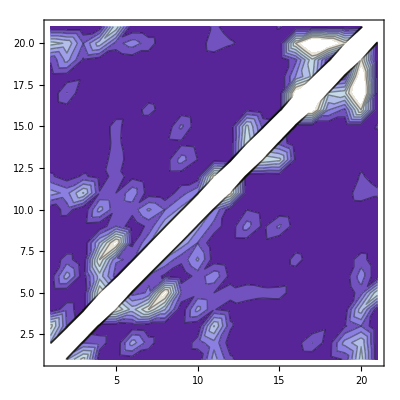

```mathematica
ListContourPlot[linkageIndex21[1]]
```

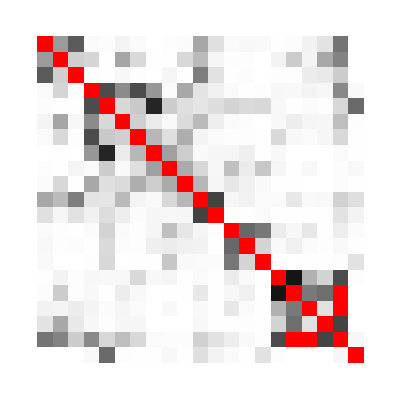

```mathematica
ArrayPlot[linkageIndex21[1],PlotRange->{0,0.1},ClippingStyle->Red,FrameTicks->Automatic]
```

```mathematica
linkRank21=Map[Ordering[Ordering[#]]&,symmetricData21]
```

{{21,17,19,13,10,12,9,2,3,5,18,14,8,7,6,4,11,15,16,20,1},{19,21,12,16,7,15,13,5,3,11,14,8,6,4,2,9,17,10,18,20,1},{20,17,21,12,8,13,7,3,11,4,18,14,5,6,1,9,10,16,15,19,2},{6,14,3,21,19,17,18,16,4,15,13,9,5,1,2,10,11,12,8,20,7},{5,2,1,20,21,14,16,18,12,9,13,11,15,8,10,7,3,6,4,17,19},{10,18,6,20,16,21,15,11,4,13,17,9,5,2,1,8,14,12,7,19,3},{7,13,3,20,18,14,21,17,12,15,10,6,4,2,1,16,11,8,9,19,5},{5,7,3,19,20,15,18,21,17,16,10,9,12,11,6,13,4,2,1,14,8},{4,2,7,11,20,6,15,19,21,17,16,5,18,8,14,13,3,12,1,10,9},{8,14,3,20,17,13,18,15,16,21,19,10,12,9,7,4,5,2,1,11,6},{18,16,17,14,12,15,7,2,9,11,21,19,5,3,1,4,13,8,6,20,10},{17,12,15,16,18,14,8,11,9,10,20,21,3,1,5,7,2,6,4,19,13},{8,4,1,10,20,6,5,9,15,12,11,3,21,18,19,14,13,16,2,17,7},{12,5,3,8,19,7,2,14,13,10,15,1,20,21,16,11,18,9,6,17,4},{14,3,2,11,19,1,6,7,17,12,13,10,20,16,21,8,4,9,5,15,18},{5,12,4,15,13,11,16,10,9,2,8,3,14,7,1,21,19,18,17,20,6},{9,16,8,13,7,14,12,1,6,5,15,4,11,10,3,19,21,18,17,20,2},{14,12,13,16,9,11,8,1,7,2,10,5,15,6,4,18,19,21,17,20,3},{15,18,13,14,9,11,12,2,4,3,10,8,7,6,5,17,19,16,21,20,1},{15,14,9,17,13,12,10,5,2,3,11,8,7,4,1,18,20,19,16,21,6},{4,3,2,16,20,11,10,9,14,8,19,15,13,7,17,12,5,6,1,18,21}}

```mathematica
Tr[linkRank21,List]
```

{21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21,21}

```mathematica
secondpos21=Sort[Position[linkRank21,20],#1<#2&]
```

{{1,20},{2,20},{3,1},{4,20},{5,4},{6,4},{7,4},{8,5},{9,5},{10,4},{11,20},{12,11},{13,5},{14,13},{15,13},{16,20},{17,20},{18,20},{19,20},{20,17},{21,5}}

```mathematica
symmetricData21[[2,20]]
```

58186

```mathematica
Part[symmetricData21,2,20]
```

58186

```mathematica
secondvars21=Map[Part[symmetricData21,#[[1]],#[[2]]]&,secondpos21]
```

{85171,58186,18266,121186,90180,29671,44535,42240,6593,13571,24628,19547,8643,6885,7049,131656,277848,217813,108760,277848,45206}

reduce self linkage : symmetric linkage

```mathematica
symmetricDataReduceSelf21=symmetricData21;
```

```mathematica
pos=1;Do[symmetricDataReduceSelf21[[pos,pos]]=secondvars21[[pos]];pos++,{pos,21}];pos=.
```

```mathematica
totalLinkageReduceSel21f=Map[Tr[#]&,symmetricDataReduceSelf21]
```

{242090,208010,79826,488695,369250,139486,154588,132073,39628,58609,161724,69878,57768,26187,26221,418928,791619,559068,311272,1426998,110086}

```mathematica
symmetricData21-symmetricDataReduceSelf21
```

{{292721,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,108144,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,69412,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1021906,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,717346,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,140865,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,110835,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,92686,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,60779,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,46541,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,250964,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,98127,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,168861,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,33425,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,50535,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,348122,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,551908,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,468313,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,172792,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3129262,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,438450}}

reduce self linkage : cited/citing data

```mathematica
citedciting21DataReduceSelf=citedciting21Data;
```

```mathematica
pos=1;Do[citedciting21DataReduceSelf[[pos,pos]]=secondvars21[[pos]];pos++,{pos,21}];pos=.
```

```mathematica
citedciting21Data-citedciting21DataReduceSelf//TableForm
```

103775 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 24979 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 25573 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 450360 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 313583 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 55597 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 33150 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 25223 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27093 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16485 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 113168 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 39290 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 80109 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13270 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21743 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 108233 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137030 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 125250 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32016 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1425707 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 196622

reduce self linkage : citing/cited data

```mathematica
citingcited21DataReduceSelf=citingcited21Data;
```

```mathematica
pos=1;Do[citingcited21DataReduceSelf[[pos,pos]]=secondvars21[[pos]];pos++,{pos,21}];pos=.
```

```mathematica
citingcited21Data-citingcited21DataReduceSelf//TableForm
```

103775 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 24979 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 25573 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 450360 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 313583 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 55597 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 33150 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 25223 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27093 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 16485 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 113168 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 39290 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 80109 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 13270 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 21743 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 108233 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 137030 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 125250 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 32016 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1425707 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 196622

## Standerdized asymmetric linkage (Cited ratio VS. citing ratio)

```mathematica
zeroself=Map[#->0&,Transpose[{Range[21],Range[21]}]]
```

{{1,1}→0,{2,2}→0,{3,3}→0,{4,4}→0,{5,5}→0,{6,6}→0,{7,7}→0,{8,8}→0,{9,9}→0,{10,10}→0,{11,11}→0,{12,12}→0,{13,13}→0,{14,14}→0,{15,15}→0,{16,16}→0,{17,17}→0,{18,18}→0,{19,19}→0,{20,20}→0,{21,21}→0}

```mathematica
standerdizeline[m_]:=Map[#/Tr[#]&,m]
```

```mathematica
standerdizecolumn[m_]:=Transpose[Map[#/Tr[#]&,Transpose[m]]]
```

```mathematica
standerdizecolumnline[m_]:=standerdizeline[standerdizecolumn[m]]
```

```mathematica
citedciting21Datastanderdized=Nest[standerdizecolumnline,N[citedciting21Data],84];
```

```mathematica
citingcited21Datastanderdized=Transpose[citedciting21Datastanderdized];
```

```mathematica
citedciting21DatastanderdizedcitedParciting=citedciting21Datastanderdized/Transpose[citedciting21Datastanderdized];
```

Power::infy: 無限式1/0.が見付かりました．

```mathematica
TableForm[Round[citedciting21Datastanderdized,0.01],TableHeadings->{ClNames21,ClNames21}]
```

| B-1 | B-2 | B-3 | C-1 | C-2 | Ca | Cp | E-1 | E-2 | E-3 | G-1 | G-2 | I-1 | I-2 | M | Me-1 | Me-2 | Me-3 | Me-4 | Mo | Q
B-1 | 0.75 | 0.05 | 0.08 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03 | 0.01 | 0. | 0. | 0. | 0. | 0. | 0.01 | 0.01 | 0.04 | 0.
B-2 | 0.04 | 0.67 | 0.03 | 0.02 | 0. | 0.04 | 0.02 | 0. | 0. | 0.02 | 0.03 | 0.01 | 0. | 0. | 0. | 0.01 | 0.02 | 0.01 | 0.05 | 0.04 | 0.
B-3 | 0.08 | 0.02 | 0.77 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.06 | 0.01 | 0. | 0. | 0. | 0. | 0. | 0.01 | 0.01 | 0.01 | 0.
C-1 | 0. | 0.02 | 0. | 0.66 | 0.06 | 0.05 | 0.08 | 0.04 | 0. | 0.04 | 0.01 | 0.01 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.03 | 0.
C-2 | 0. | 0. | 0. | 0.06 | 0.64 | 0.01 | 0.02 | 0.08 | 0.02 | 0.01 | 0.01 | 0.02 | 0.02 | 0.02 | 0.02 | 0. | 0. | 0. | 0. | 0. | 0.06
Ca | 0. | 0.04 | 0. | 0.05 | 0.02 | 0.75 | 0.02 | 0.01 | 0. | 0.02 | 0.02 | 0.01 | 0. | 0. | 0. | 0. | 0.01 | 0.01 | 0. | 0.02 | 0.
Cp | 0. | 0.02 | 0. | 0.07 | 0.02 | 0.02 | 0.72 | 0.04 | 0.02 | 0.04 | 0. | 0. | 0. | 0. | 0. | 0.02 | 0. | 0. | 0. | 0.01 | 0.
E-1 | 0. | 0. | 0. | 0.04 | 0.09 | 0.01 | 0.03 | 0.73 | 0.04 | 0.02 | 0. | 0. | 0. | 0.01 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
E-2 | 0. | 0. | 0. | 0. | 0.02 | 0. | 0.01 | 0.04 | 0.78 | 0.04 | 0.02 | 0. | 0.03 | 0.01 | 0.03 | 0. | 0. | 0. | 0. | 0. | 0.
E-3 | 0. | 0.02 | 0. | 0.03 | 0.01 | 0.02 | 0.04 | 0.02 | 0.04 | 0.75 | 0.03 | 0.01 | 0.01 | 0.01 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
G-1 | 0.04 | 0.03 | 0.06 | 0.01 | 0.01 | 0.03 | 0.01 | 0. | 0.02 | 0.03 | 0.64 | 0.07 | 0. | 0. | 0. | 0. | 0.01 | 0. | 0. | 0.01 | 0.01
G-2 | 0.01 | 0. | 0.01 | 0.01 | 0.01 | 0.01 | 0. | 0. | 0. | 0. | 0.09 | 0.83 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.01 | 0.01
I-1 | 0. | 0. | 0. | 0. | 0.02 | 0. | 0. | 0. | 0.02 | 0.01 | 0. | 0. | 0.78 | 0.07 | 0.05 | 0.01 | 0. | 0.01 | 0. | 0. | 0.
I-2 | 0. | 0. | 0. | 0. | 0.01 | 0. | 0. | 0.01 | 0.01 | 0.01 | 0.01 | 0. | 0.06 | 0.85 | 0.02 | 0. | 0.01 | 0. | 0. | 0. | 0.
M | 0. | 0. | 0. | 0. | 0.01 | 0. | 0. | 0. | 0.02 | 0. | 0. | 0. | 0.06 | 0.02 | 0.86 | 0. | 0. | 0. | 0. | 0. | 0.01
Me-1 | 0. | 0.01 | 0. | 0. | 0. | 0. | 0.02 | 0. | 0. | 0. | 0. | 0. | 0.01 | 0. | 0. | 0.73 | 0.1 | 0.04 | 0.02 | 0.06 | 0.
Me-2 | 0. | 0.02 | 0. | 0. | 0. | 0.01 | 0. | 0. | 0. | 0. | 0.01 | 0. | 0. | 0.01 | 0. | 0.1 | 0.63 | 0.05 | 0.06 | 0.1 | 0.
Me-3 | 0. | 0. | 0.01 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.01 | 0. | 0. | 0.03 | 0.06 | 0.76 | 0.01 | 0.09 | 0.
Me-4 | 0.01 | 0.04 | 0.01 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.02 | 0.07 | 0.01 | 0.75 | 0.07 | 0.
Mo | 0.04 | 0.04 | 0.02 | 0.03 | 0.01 | 0.02 | 0.01 | 0. | 0. | 0. | 0.01 | 0.01 | 0.01 | 0. | 0. | 0.06 | 0.09 | 0.09 | 0.06 | 0.49 | 0.
Q | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0.01 | 0. | 0. | 0. | 0.01 | 0. | 0. | 0. | 0. | 0. | 0.9

```mathematica
TableForm[Round[citedciting21DatastanderdizedcitedParciting,0.01]/.{ComplexInfinity->"None"},TableHeadings->{ClNames21,ClNames21}]
```

| B-1 | B-2 | B-3 | C-1 | C-2 | Ca | Cp | E-1 | E-2 | E-3 | G-1 | G-2 | I-1 | I-2 | M | Me-1 | Me-2 | Me-3 | Me-4 | Mo | Q
B-1 | 1. | 1.24 | 1. | 1.08 | 1.76 | 1.15 | 0.97 | 1.31 | 0.78 | 0.53 | 0.89 | 0.89 | 1.02 | 0.39 | 0.85 | 0.96 | 0.92 | 1.44 | 1.25 | 0.87 | 1.4
B-2 | 0.81 | 1. | 1.13 | 1.05 | 0.81 | 0.98 | 0.89 | 1.02 | 0.52 | 0.96 | 0.92 | 1.54 | 0.95 | 1. | 1.03 | 1.05 | 1.02 | 1.19 | 1.14 | 1.08 | 1.82
B-3 | 1. | 0.89 | 1. | 1.17 | 0.87 | 1.51 | 0.86 | 1.04 | 0.95 | 0.37 | 1.05 | 1.02 | 0.56 | 0.18 | 0.3 | 1.15 | 0.41 | 1.22 | 1.27 | 0.85 | 7.93
C-1 | 0.93 | 0.96 | 0.86 | 1. | 1.03 | 0.94 | 1.15 | 0.93 | 1.94 | 1.1 | 0.91 | 1.04 | 1.16 | 0.88 | 1.13 | 0.67 | 0.31 | 0.5 | 0.66 | 0.97 | 0.59
C-2 | 0.57 | 1.23 | 1.15 | 0.97 | 1. | 0.87 | 1.14 | 0.93 | 0.92 | 0.86 | 0.99 | 2.21 | 1.12 | 1.19 | 1.16 | 1.1 | 0.7 | 1.46 | 0.82 | 0.34 | 1.1
Ca | 0.87 | 1.02 | 0.66 | 1.06 | 1.15 | 1. | 0.92 | 1.04 | 1.3 | 1.12 | 0.63 | 0.69 | 1.82 | 1.31 | 3.4 | 0.97 | 1.35 | 1.67 | 1.04 | 1.27 | 0.77
Cp | 1.04 | 1.12 | 1.17 | 0.87 | 0.88 | 1.09 | 1. | 1.26 | 1.25 | 1.01 | 0.82 | 0.77 | 0.81 | 0.75 | 1.72 | 0.84 | 0.89 | 1.2 | 0.93 | 1.13 | 0.51
E-1 | 0.76 | 0.98 | 0.96 | 1.08 | 1.08 | 0.96 | 0.79 | 1. | 1.03 | 0.99 | 0.98 | 1.08 | 0.97 | 1.09 | 0.7 | 0.6 | 1.65 | 1.94 | 0.72 | 0.36 | 0.42
E-2 | 1.29 | 1.92 | 1.05 | 0.51 | 1.08 | 0.77 | 0.8 | 0.97 | 1. | 0.89 | 1.08 | 2.64 | 1.15 | 0.66 | 1.13 | 1.18 | 1.27 | 1.49 | 1.86 | 0.81 | 1.01
E-3 | 1.9 | 1.04 | 2.7 | 0.91 | 1.17 | 0.89 | 0.99 | 1.01 | 1.13 | 1. | 0.92 | 1.32 | 0.83 | 0.83 | 1.37 | 1.66 | 0.78 | 1.1 | 2.09 | 0.43 | 1.32
G-1 | 1.13 | 1.08 | 0.96 | 1.1 | 1.01 | 1.59 | 1.22 | 1.02 | 0.93 | 1.09 | 1. | 0.82 | 0.9 | 0.69 | 3.15 | 0.87 | 1.09 | 0.68 | 1.12 | 1.04 | 0.72
G-2 | 1.13 | 0.65 | 0.98 | 0.96 | 0.45 | 1.44 | 1.3 | 0.93 | 0.38 | 0.76 | 1.23 | 1. | 0.31 | 0. | 1. | 2.02 | 0.53 | 0.35 | 0.58 | 0.59 | 1.06
I-1 | 0.98 | 1.05 | 1.78 | 0.86 | 0.89 | 0.55 | 1.23 | 1.04 | 0.87 | 1.21 | 1.12 | 3.25 | 1. | 1.2 | 0.91 | 0.98 | 1.14 | 0.92 | 0.81 | 0.63 | 0.48
I-2 | 2.56 | 1. | 5.63 | 1.13 | 0.84 | 0.77 | 1.33 | 0.92 | 1.53 | 1.21 | 1.44 | None | 0.83 | 1. | 0.95 | 1.42 | 1.7 | 1.28 | 1.21 | 1.19 | 0.24
M | 1.18 | 0.97 | 3.32 | 0.89 | 0.86 | 0.29 | 0.58 | 1.44 | 0.89 | 0.73 | 0.32 | 1. | 1.09 | 1.05 | 1. | 1.98 | 4.75 | 0.77 | 0.91 | 0.8 | 1.13
Me-1 | 1.04 | 0.95 | 0.87 | 1.5 | 0.91 | 1.03 | 1.18 | 1.67 | 0.85 | 0.6 | 1.15 | 0.49 | 1.02 | 0.7 | 0.5 | 1. | 0.97 | 1.07 | 0.9 | 1.01 | 0.57
Me-2 | 1.08 | 0.98 | 2.41 | 3.27 | 1.44 | 0.74 | 1.13 | 0.61 | 0.79 | 1.29 | 0.92 | 1.89 | 0.88 | 0.59 | 0.21 | 1.03 | 1. | 0.91 | 0.95 | 1.11 | 0.56
Me-3 | 0.69 | 0.84 | 0.82 | 2.02 | 0.68 | 0.6 | 0.83 | 0.52 | 0.67 | 0.91 | 1.48 | 2.87 | 1.08 | 0.78 | 1.31 | 0.94 | 1.1 | 1. | 1.02 | 1.02 | 2.77
Me-4 | 0.8 | 0.88 | 0.79 | 1.52 | 1.22 | 0.96 | 1.07 | 1.38 | 0.54 | 0.48 | 0.89 | 1.71 | 1.23 | 0.83 | 1.1 | 1.11 | 1.05 | 0.98 | 1. | 1.08 | 0.
Mo | 1.15 | 0.93 | 1.18 | 1.03 | 2.97 | 0.79 | 0.88 | 2.8 | 1.24 | 2.31 | 0.96 | 1.68 | 1.58 | 0.84 | 1.25 | 0.99 | 0.9 | 0.98 | 0.93 | 1. | 1.6
Q | 0.72 | 0.55 | 0.13 | 1.7 | 0.91 | 1.29 | 1.94 | 2.4 | 0.99 | 0.76 | 1.39 | 0.95 | 2.07 | 4.25 | 0.88 | 1.76 | 1.8 | 0.36 | None | 0.62 | 1.

```mathematica
TableForm[Round[citedciting21DatastanderdizedcitedParciting,0.01]/.{ComplexInfinity->"None"},TableHeadings->{Flatten[jFieldName21],Flatten[jFieldName21withLF]},TableSpacing->{0.5,0.5}]
```

| 動植物学 | 農学・
食品学 | 水産・海洋 | 化学 | 物性物理 | 分析化学 | 応用化学 | 金属・セラ
ミックス | 機械・
土木建築 | 化学工学・
エネルギー
工学 | 気象・環境 | 地球科学 | 電子情報
工学 | 数理工学 | 数学 | 臨床医学1 | 臨床医学2 | 心理・
神経科学 | 獣医学・
感染症 | 生化学・
生理学 | 素粒子・
天体物理
動植物学 | 1. | 1.24 | 1. | 1.08 | 1.76 | 1.15 | 0.97 | 1.31 | 0.78 | 0.53 | 0.89 | 0.89 | 1.02 | 0.39 | 0.85 | 0.96 | 0.92 | 1.44 | 1.25 | 0.87 | 1.4
農学・食品学 | 0.81 | 1. | 1.13 | 1.05 | 0.81 | 0.98 | 0.89 | 1.02 | 0.52 | 0.96 | 0.92 | 1.54 | 0.95 | 1. | 1.03 | 1.05 | 1.02 | 1.19 | 1.14 | 1.08 | 1.82
水産・海洋 | 1. | 0.89 | 1. | 1.17 | 0.87 | 1.51 | 0.86 | 1.04 | 0.95 | 0.37 | 1.05 | 1.02 | 0.56 | 0.18 | 0.3 | 1.15 | 0.41 | 1.22 | 1.27 | 0.85 | 7.93
化学 | 0.93 | 0.96 | 0.86 | 1. | 1.03 | 0.94 | 1.15 | 0.93 | 1.94 | 1.1 | 0.91 | 1.04 | 1.16 | 0.88 | 1.13 | 0.67 | 0.31 | 0.5 | 0.66 | 0.97 | 0.59
物性物理 | 0.57 | 1.23 | 1.15 | 0.97 | 1. | 0.87 | 1.14 | 0.93 | 0.92 | 0.86 | 0.99 | 2.21 | 1.12 | 1.19 | 1.16 | 1.1 | 0.7 | 1.46 | 0.82 | 0.34 | 1.1
分析化学 | 0.87 | 1.02 | 0.66 | 1.06 | 1.15 | 1. | 0.92 | 1.04 | 1.3 | 1.12 | 0.63 | 0.69 | 1.82 | 1.31 | 3.4 | 0.97 | 1.35 | 1.67 | 1.04 | 1.27 | 0.77
応用化学 | 1.04 | 1.12 | 1.17 | 0.87 | 0.88 | 1.09 | 1. | 1.26 | 1.25 | 1.01 | 0.82 | 0.77 | 0.81 | 0.75 | 1.72 | 0.84 | 0.89 | 1.2 | 0.93 | 1.13 | 0.51
金属・セラミックス | 0.76 | 0.98 | 0.96 | 1.08 | 1.08 | 0.96 | 0.79 | 1. | 1.03 | 0.99 | 0.98 | 1.08 | 0.97 | 1.09 | 0.7 | 0.6 | 1.65 | 1.94 | 0.72 | 0.36 | 0.42
機械・土木建築 | 1.29 | 1.92 | 1.05 | 0.51 | 1.08 | 0.77 | 0.8 | 0.97 | 1. | 0.89 | 1.08 | 2.64 | 1.15 | 0.66 | 1.13 | 1.18 | 1.27 | 1.49 | 1.86 | 0.81 | 1.01
化学工学・エネルギー工学 | 1.9 | 1.04 | 2.7 | 0.91 | 1.17 | 0.89 | 0.99 | 1.01 | 1.13 | 1. | 0.92 | 1.32 | 0.83 | 0.83 | 1.37 | 1.66 | 0.78 | 1.1 | 2.09 | 0.43 | 1.32
気象・環境 | 1.13 | 1.08 | 0.96 | 1.1 | 1.01 | 1.59 | 1.22 | 1.02 | 0.93 | 1.09 | 1. | 0.82 | 0.9 | 0.69 | 3.15 | 0.87 | 1.09 | 0.68 | 1.12 | 1.04 | 0.72
地球科学 | 1.13 | 0.65 | 0.98 | 0.96 | 0.45 | 1.44 | 1.3 | 0.93 | 0.38 | 0.76 | 1.23 | 1. | 0.31 | 0. | 1. | 2.02 | 0.53 | 0.35 | 0.58 | 0.59 | 1.06
電子情報工学 | 0.98 | 1.05 | 1.78 | 0.86 | 0.89 | 0.55 | 1.23 | 1.04 | 0.87 | 1.21 | 1.12 | 3.25 | 1. | 1.2 | 0.91 | 0.98 | 1.14 | 0.92 | 0.81 | 0.63 | 0.48
数理工学 | 2.56 | 1. | 5.63 | 1.13 | 0.84 | 0.77 | 1.33 | 0.92 | 1.53 | 1.21 | 1.44 | None | 0.83 | 1. | 0.95 | 1.42 | 1.7 | 1.28 | 1.21 | 1.19 | 0.24
数学 | 1.18 | 0.97 | 3.32 | 0.89 | 0.86 | 0.29 | 0.58 | 1.44 | 0.89 | 0.73 | 0.32 | 1. | 1.09 | 1.05 | 1. | 1.98 | 4.75 | 0.77 | 0.91 | 0.8 | 1.13
臨床医学1 | 1.04 | 0.95 | 0.87 | 1.5 | 0.91 | 1.03 | 1.18 | 1.67 | 0.85 | 0.6 | 1.15 | 0.49 | 1.02 | 0.7 | 0.5 | 1. | 0.97 | 1.07 | 0.9 | 1.01 | 0.57
臨床医学2 | 1.08 | 0.98 | 2.41 | 3.27 | 1.44 | 0.74 | 1.13 | 0.61 | 0.79 | 1.29 | 0.92 | 1.89 | 0.88 | 0.59 | 0.21 | 1.03 | 1. | 0.91 | 0.95 | 1.11 | 0.56
心理・神経科学 | 0.69 | 0.84 | 0.82 | 2.02 | 0.68 | 0.6 | 0.83 | 0.52 | 0.67 | 0.91 | 1.48 | 2.87 | 1.08 | 0.78 | 1.31 | 0.94 | 1.1 | 1. | 1.02 | 1.02 | 2.77
獣医学・感染症 | 0.8 | 0.88 | 0.79 | 1.52 | 1.22 | 0.96 | 1.07 | 1.38 | 0.54 | 0.48 | 0.89 | 1.71 | 1.23 | 0.83 | 1.1 | 1.11 | 1.05 | 0.98 | 1. | 1.08 | 0.
生化学・生理学 | 1.15 | 0.93 | 1.18 | 1.03 | 2.97 | 0.79 | 0.88 | 2.8 | 1.24 | 2.31 | 0.96 | 1.68 | 1.58 | 0.84 | 1.25 | 0.99 | 0.9 | 0.98 | 0.93 | 1. | 1.6
素粒子・天体物理 | 0.72 | 0.55 | 0.13 | 1.7 | 0.91 | 1.29 | 1.94 | 2.4 | 0.99 | 0.76 | 1.39 | 0.95 | 2.07 | 4.25 | 0.88 | 1.76 | 1.8 | 0.36 | None | 0.62 | 1.

for jsims letter ->

```mathematica
asymmetrictable=TableForm[Round[citedciting21DatastanderdizedcitedParciting,0.01]/.{ComplexInfinity->"None"},TableHeadings->{jFieldName21Text,jFieldName21withLFText},TableSpacing->{0.75,0.5}]
```

| 動植物学 | 農学・
食品学 | 水産・海洋 | 化学 | 物性物理 | 分析化学 | 応用化学 | 金属・セラ
ミックス | 機械・
土木建築 | 化学工学・
エネルギー
工学 | 気象・環境 | 地球科学 | 電子情報
工学 | 数理工学 | 数学 | 臨床医学1 | 臨床医学2 | 心理・
神経科学 | 獣医学・
感染症 | 生化学・
生理学 | 素粒子・
天体物理
動植物学 | 1. | 1.24 | 1. | 1.08 | 1.76 | 1.15 | 0.97 | 1.31 | 0.78 | 0.53 | 0.89 | 0.89 | 1.02 | 0.39 | 0.85 | 0.96 | 0.92 | 1.44 | 1.25 | 0.87 | 1.4
農学・食品学 | 0.81 | 1. | 1.13 | 1.05 | 0.81 | 0.98 | 0.89 | 1.02 | 0.52 | 0.96 | 0.92 | 1.54 | 0.95 | 1. | 1.03 | 1.05 | 1.02 | 1.19 | 1.14 | 1.08 | 1.82
水産・海洋 | 1. | 0.89 | 1. | 1.17 | 0.87 | 1.51 | 0.86 | 1.04 | 0.95 | 0.37 | 1.05 | 1.02 | 0.56 | 0.18 | 0.3 | 1.15 | 0.41 | 1.22 | 1.27 | 0.85 | 7.93
化学 | 0.93 | 0.96 | 0.86 | 1. | 1.03 | 0.94 | 1.15 | 0.93 | 1.94 | 1.1 | 0.91 | 1.04 | 1.16 | 0.88 | 1.13 | 0.67 | 0.31 | 0.5 | 0.66 | 0.97 | 0.59
物性物理 | 0.57 | 1.23 | 1.15 | 0.97 | 1. | 0.87 | 1.14 | 0.93 | 0.92 | 0.86 | 0.99 | 2.21 | 1.12 | 1.19 | 1.16 | 1.1 | 0.7 | 1.46 | 0.82 | 0.34 | 1.1
分析化学 | 0.87 | 1.02 | 0.66 | 1.06 | 1.15 | 1. | 0.92 | 1.04 | 1.3 | 1.12 | 0.63 | 0.69 | 1.82 | 1.31 | 3.4 | 0.97 | 1.35 | 1.67 | 1.04 | 1.27 | 0.77
応用化学 | 1.04 | 1.12 | 1.17 | 0.87 | 0.88 | 1.09 | 1. | 1.26 | 1.25 | 1.01 | 0.82 | 0.77 | 0.81 | 0.75 | 1.72 | 0.84 | 0.89 | 1.2 | 0.93 | 1.13 | 0.51
金属・
セラミックス | 0.76 | 0.98 | 0.96 | 1.08 | 1.08 | 0.96 | 0.79 | 1. | 1.03 | 0.99 | 0.98 | 1.08 | 0.97 | 1.09 | 0.7 | 0.6 | 1.65 | 1.94 | 0.72 | 0.36 | 0.42
機械・土木建築 | 1.29 | 1.92 | 1.05 | 0.51 | 1.08 | 0.77 | 0.8 | 0.97 | 1. | 0.89 | 1.08 | 2.64 | 1.15 | 0.66 | 1.13 | 1.18 | 1.27 | 1.49 | 1.86 | 0.81 | 1.01
化学工学・エ
ネルギー工学 | 1.9 | 1.04 | 2.7 | 0.91 | 1.17 | 0.89 | 0.99 | 1.01 | 1.13 | 1. | 0.92 | 1.32 | 0.83 | 0.83 | 1.37 | 1.66 | 0.78 | 1.1 | 2.09 | 0.43 | 1.32
気象・環境 | 1.13 | 1.08 | 0.96 | 1.1 | 1.01 | 1.59 | 1.22 | 1.02 | 0.93 | 1.09 | 1. | 0.82 | 0.9 | 0.69 | 3.15 | 0.87 | 1.09 | 0.68 | 1.12 | 1.04 | 0.72
地球科学 | 1.13 | 0.65 | 0.98 | 0.96 | 0.45 | 1.44 | 1.3 | 0.93 | 0.38 | 0.76 | 1.23 | 1. | 0.31 | 0. | 1. | 2.02 | 0.53 | 0.35 | 0.58 | 0.59 | 1.06
電子情報工学 | 0.98 | 1.05 | 1.78 | 0.86 | 0.89 | 0.55 | 1.23 | 1.04 | 0.87 | 1.21 | 1.12 | 3.25 | 1. | 1.2 | 0.91 | 0.98 | 1.14 | 0.92 | 0.81 | 0.63 | 0.48
数理工学 | 2.56 | 1. | 5.63 | 1.13 | 0.84 | 0.77 | 1.33 | 0.92 | 1.53 | 1.21 | 1.44 | None | 0.83 | 1. | 0.95 | 1.42 | 1.7 | 1.28 | 1.21 | 1.19 | 0.24
数学 | 1.18 | 0.97 | 3.32 | 0.89 | 0.86 | 0.29 | 0.58 | 1.44 | 0.89 | 0.73 | 0.32 | 1. | 1.09 | 1.05 | 1. | 1.98 | 4.75 | 0.77 | 0.91 | 0.8 | 1.13
臨床医学1 | 1.04 | 0.95 | 0.87 | 1.5 | 0.91 | 1.03 | 1.18 | 1.67 | 0.85 | 0.6 | 1.15 | 0.49 | 1.02 | 0.7 | 0.5 | 1. | 0.97 | 1.07 | 0.9 | 1.01 | 0.57
臨床医学2 | 1.08 | 0.98 | 2.41 | 3.27 | 1.44 | 0.74 | 1.13 | 0.61 | 0.79 | 1.29 | 0.92 | 1.89 | 0.88 | 0.59 | 0.21 | 1.03 | 1. | 0.91 | 0.95 | 1.11 | 0.56
心理・神経科学 | 0.69 | 0.84 | 0.82 | 2.02 | 0.68 | 0.6 | 0.83 | 0.52 | 0.67 | 0.91 | 1.48 | 2.87 | 1.08 | 0.78 | 1.31 | 0.94 | 1.1 | 1. | 1.02 | 1.02 | 2.77
獣医学・感染症 | 0.8 | 0.88 | 0.79 | 1.52 | 1.22 | 0.96 | 1.07 | 1.38 | 0.54 | 0.48 | 0.89 | 1.71 | 1.23 | 0.83 | 1.1 | 1.11 | 1.05 | 0.98 | 1. | 1.08 | 0.
生化学・生理学 | 1.15 | 0.93 | 1.18 | 1.03 | 2.97 | 0.79 | 0.88 | 2.8 | 1.24 | 2.31 | 0.96 | 1.68 | 1.58 | 0.84 | 1.25 | 0.99 | 0.9 | 0.98 | 0.93 | 1. | 1.6
素粒子・
天体物理 | 0.72 | 0.55 | 0.13 | 1.7 | 0.91 | 1.29 | 1.94 | 2.4 | 0.99 | 0.76 | 1.39 | 0.95 | 2.07 | 4.25 | 0.88 | 1.76 | 1.8 | 0.36 | None | 0.62 | 1.

```mathematica
asymmetrictable=TableForm[Ceiling[citedciting21DatastanderdizedcitedParciting,1]/.{ComplexInfinity->"None"},TableHeadings->{jFieldName21Text,jFieldName21withLFText},TableSpacing->{0.75,0.5}]
```

| 動植物学 | 農学・
食品学 | 水産・海洋 | 化学 | 物性物理 | 分析化学 | 応用化学 | 金属・セラ
ミックス | 機械・
土木建築 | 化学工学・
エネルギー
工学 | 気象・環境 | 地球科学 | 電子情報
工学 | 数理工学 | 数学 | 臨床医学1 | 臨床医学2 | 心理・
神経科学 | 獣医学・
感染症 | 生化学・
生理学 | 素粒子・
天体物理
動植物学 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2
農学・食品学 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
水産・海洋 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 1 | 8
化学 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1
物性物理 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 3 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 2
分析化学 | 1 | 2 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 4 | 1 | 2 | 2 | 2 | 2 | 1
応用化学 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1
金属・
セラミックス | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1
機械・土木建築 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2
化学工学・エ
ネルギー工学 | 2 | 2 | 3 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 2 | 2 | 1 | 2 | 3 | 1 | 2
気象・環境 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 4 | 1 | 2 | 1 | 2 | 2 | 1
地球科学 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 0 | 2 | 3 | 1 | 1 | 1 | 1 | 2
電子情報工学 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 4 | 1 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1
数理工学 | 3 | 1 | 6 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | None | 1 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1
数学 | 2 | 1 | 4 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 5 | 1 | 1 | 1 | 2
臨床医学1 | 2 | 1 | 1 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 2 | 1
臨床医学2 | 2 | 1 | 3 | 4 | 2 | 1 | 2 | 1 | 1 | 2 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1
心理・神経科学 | 1 | 1 | 1 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 2 | 3
獣医学・感染症 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 2 | 2 | 2 | 1 | 1 | 2 | 0
生化学・生理学 | 2 | 1 | 2 | 2 | 3 | 1 | 1 | 3 | 2 | 3 | 1 | 2 | 2 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 2
素粒子・
天体物理 | 1 | 1 | 1 | 2 | 1 | 2 | 2 | 3 | 1 | 1 | 2 | 1 | 3 | 5 | 1 | 2 | 2 | 1 | None | 1 | 1

```mathematica
Tr[Round[citedciting21DatastanderdizedcitedParciting,0.01]/.{ComplexInfinity->"None"},List]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
(asymmetricEffectTable=Ceiling[citedciting21DatastanderdizedcitedParciting,1]-1/.{ComplexInfinity->"None"})//TableForm
```

0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 7
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 3 | 0 | 1 | 1 | 1 | 1 | 0
1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 2 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 2 | 0 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 3 | 0 | 1 | 0 | 1 | 1 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 1 | 2 | 0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 3 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
2 | 0 | 5 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | None | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0
1 | 0 | 3 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
1 | 0 | 2 | 3 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 2
0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | -1
1 | 0 | 1 | 1 | 2 | 0 | 0 | 2 | 1 | 2 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 1 | 1 | 2 | 0 | 0 | 1 | 0 | 2 | 4 | 0 | 1 | 1 | 0 | None | 0 | 0

```mathematica
Table[Count[asymmetricEffectTable[[n]],x_/;x>0],{n,21}]
```

{9,12,10,7,10,13,10,7,13,12,12,7,9,12,8,9,9,9,10,11,9}

```mathematica
(Table[Count[asymmetricEffectTable[[n]],x_/;x>0],{n,21}]//Tr)
```

208

```mathematica
((21*21)-21)/2
```

210

```mathematica
Position[Table[Count[asymmetricEffectTable[[n]],x_/;x>0],{n,21}],13]
```

{{6},{9}}

```mathematica
jFieldName21[[{6,9}]]
```

{{分析化学},{機械・土木建築}}

```mathematica
Position[Table[Count[asymmetricEffectTable[[n]],x_/;x>0],{n,21}],7]
```

{{4},{8},{12}}

```mathematica
jFieldName21[[{4,8,12}]]
```

{{化学},{金属・セラミックス},{地球科学}}

```mathematica
Map[Select[#,#≥4&]&,citedciting21DatastanderdizedcitedParciting]
```

GreaterEqual::nord: ComplexInfinityとの無効な比較が試みられました．

{{},{},{7.92644},{},{},{},{},{},{},{},{},{},{},{5.62715},{4.74506},{},{},{},{},{},{4.24759}}

## Standerdized symmetric linkage

```mathematica
symmetricLinkage21Datastanderdized=citedciting21Datastanderdized+citingcited21Datastanderdized;
```

```mathematica
TableForm[Round[symmetricLinkage21Datastanderdized,0.001]]
```

1.497 | 0.091 | 0.152 | 0.003 | 0.002 | 0.009 | 0.004 | 0. | 0.002 | 0.004 | 0.07 | 0.027 | 0.004 | 0.006 | 0.005 | 0.001 | 0.002 | 0.011 | 0.026 | 0.083 | 0.
0.091 | 1.35 | 0.049 | 0.034 | 0.001 | 0.088 | 0.037 | 0.001 | 0.001 | 0.039 | 0.06 | 0.009 | 0.001 | 0.002 | 0. | 0.011 | 0.044 | 0.01 | 0.087 | 0.084 | 0.
0.152 | 0.049 | 1.55 | 0.003 | 0.001 | 0.008 | 0.002 | 0. | 0.01 | 0.001 | 0.115 | 0.029 | 0.001 | 0.002 | 0. | 0.002 | 0.002 | 0.018 | 0.023 | 0.032 | 0.
0.003 | 0.034 | 0.003 | 1.313 | 0.121 | 0.094 | 0.145 | 0.084 | 0.004 | 0.072 | 0.019 | 0.011 | 0.003 | 0.001 | 0.001 | 0.006 | 0.004 | 0.007 | 0.007 | 0.062 | 0.004
0.002 | 0.001 | 0.001 | 0.121 | 1.285 | 0.031 | 0.043 | 0.174 | 0.04 | 0.026 | 0.018 | 0.024 | 0.032 | 0.03 | 0.03 | 0.006 | 0.001 | 0.003 | 0.002 | 0.019 | 0.109
0.009 | 0.088 | 0.008 | 0.094 | 0.031 | 1.502 | 0.045 | 0.019 | 0.006 | 0.036 | 0.057 | 0.016 | 0.005 | 0.003 | 0. | 0.006 | 0.015 | 0.009 | 0.008 | 0.042 | 0.002
0.004 | 0.037 | 0.002 | 0.145 | 0.043 | 0.045 | 1.448 | 0.069 | 0.03 | 0.081 | 0.01 | 0.004 | 0.002 | 0.001 | 0.001 | 0.033 | 0.006 | 0.004 | 0.009 | 0.025 | 0.001
0. | 0.001 | 0. | 0.084 | 0.174 | 0.019 | 0.069 | 1.467 | 0.088 | 0.05 | 0.005 | 0.008 | 0.009 | 0.015 | 0.001 | 0.006 | 0. | 0. | 0. | 0.002 | 0.001
0.002 | 0.001 | 0.01 | 0.004 | 0.04 | 0.006 | 0.03 | 0.088 | 1.553 | 0.082 | 0.033 | 0.006 | 0.053 | 0.017 | 0.051 | 0.009 | 0.001 | 0.007 | 0. | 0.002 | 0.006
0.004 | 0.039 | 0.001 | 0.072 | 0.026 | 0.036 | 0.081 | 0.05 | 0.082 | 1.491 | 0.063 | 0.009 | 0.021 | 0.014 | 0.006 | 0.001 | 0.001 | 0. | 0. | 0.002 | 0.001
0.07 | 0.06 | 0.115 | 0.019 | 0.018 | 0.057 | 0.01 | 0.005 | 0.033 | 0.063 | 1.287 | 0.159 | 0.008 | 0.011 | 0.003 | 0.004 | 0.017 | 0.004 | 0.006 | 0.026 | 0.025
0.027 | 0.009 | 0.029 | 0.011 | 0.024 | 0.016 | 0.004 | 0.008 | 0.006 | 0.009 | 0.159 | 1.662 | 0.002 | 0.001 | 0.004 | 0.001 | 0. | 0.001 | 0.001 | 0.015 | 0.01
0.004 | 0.001 | 0.001 | 0.003 | 0.032 | 0.005 | 0.002 | 0.009 | 0.053 | 0.021 | 0.008 | 0.002 | 1.56 | 0.133 | 0.114 | 0.015 | 0.006 | 0.019 | 0.001 | 0.009 | 0.003
0.006 | 0.002 | 0.002 | 0.001 | 0.03 | 0.003 | 0.001 | 0.015 | 0.017 | 0.014 | 0.011 | 0.001 | 0.133 | 1.694 | 0.04 | 0.005 | 0.014 | 0.004 | 0.002 | 0.004 | 0.001
0.005 | 0. | 0. | 0.001 | 0.03 | 0. | 0.001 | 0.001 | 0.051 | 0.006 | 0.003 | 0.004 | 0.114 | 0.04 | 1.714 | 0.001 | 0. | 0.001 | 0. | 0.001 | 0.024
0.001 | 0.011 | 0.002 | 0.006 | 0.006 | 0.006 | 0.033 | 0.006 | 0.009 | 0.001 | 0.004 | 0.001 | 0.015 | 0.005 | 0.001 | 1.459 | 0.197 | 0.07 | 0.043 | 0.121 | 0.001
0.002 | 0.044 | 0.002 | 0.004 | 0.001 | 0.015 | 0.006 | 0. | 0.001 | 0.001 | 0.017 | 0. | 0.006 | 0.014 | 0. | 0.197 | 1.267 | 0.113 | 0.127 | 0.184 | 0.
0.011 | 0.01 | 0.018 | 0.007 | 0.003 | 0.009 | 0.004 | 0. | 0.007 | 0. | 0.004 | 0.001 | 0.019 | 0.004 | 0.001 | 0.07 | 0.113 | 1.518 | 0.028 | 0.172 | 0.
0.026 | 0.087 | 0.023 | 0.007 | 0.002 | 0.008 | 0.009 | 0. | 0. | 0. | 0.006 | 0.001 | 0.001 | 0.002 | 0. | 0.043 | 0.127 | 0.028 | 1.498 | 0.131 | 0.
0.083 | 0.084 | 0.032 | 0.062 | 0.019 | 0.042 | 0.025 | 0.002 | 0.002 | 0.002 | 0.026 | 0.015 | 0.009 | 0.004 | 0.001 | 0.121 | 0.184 | 0.172 | 0.131 | 0.979 | 0.005
0. | 0. | 0. | 0.004 | 0.109 | 0.002 | 0.001 | 0.001 | 0.006 | 0.001 | 0.025 | 0.01 | 0.003 | 0.001 | 0.024 | 0.001 | 0. | 0. | 0. | 0.005 | 1.805

```mathematica
(symmetricLinkage21DataDiagonalstanderdized=diagonalStanderdize[ symmetricLinkage21Datastanderdized])//TableForm
```

1. | 0.0640989 | 0.10005 | 0.00244814 | 0.00163928 | 0.00614128 | 0.00287575 | 0.000154558 | 0.00103104 | 0.00261369 | 0.0503632 | 0.0168077 | 0.00251705 | 0.0037222 | 0.00326986 | 0.00082087 | 0.00154185 | 0.0073301 | 0.0171941 | 0.068407 | 0.0000648732
0.0640989 | 1. | 0.0337152 | 0.0258165 | 0.000913682 | 0.0615503 | 0.0268186 | 0.000922969 | 0.000618971 | 0.027501 | 0.0452461 | 0.00581098 | 0.000925513 | 0.0011524 | 0.000265703 | 0.00795794 | 0.0334332 | 0.00697918 | 0.0614913 | 0.073152 | 0.0000729299
0.10005 | 0.0337152 | 1. | 0.00189852 | 0.000816315 | 0.00504301 | 0.00118577 | 0.000201467 | 0.00621737 | 0.000964353 | 0.081424 | 0.0182488 | 0.000619899 | 0.00135385 | 0.000200252 | 0.00136659 | 0.00125607 | 0.0115008 | 0.0150366 | 0.0262151 | 0.0000843308
0.00244814 | 0.0258165 | 0.00189852 | 1. | 0.0931538 | 0.067154 | 0.105431 | 0.0604619 | 0.00301127 | 0.0514721 | 0.0148307 | 0.00764815 | 0.00219618 | 0.000662427 | 0.000802481 | 0.00429663 | 0.0029287 | 0.00511294 | 0.00468395 | 0.054448 | 0.00287827
0.00163928 | 0.000913682 | 0.000816315 | 0.0931538 | 1. | 0.0225029 | 0.0315534 | 0.126826 | 0.0282842 | 0.0189149 | 0.0141767 | 0.0164975 | 0.0227653 | 0.0203249 | 0.0204067 | 0.00405864 | 0.000405259 | 0.00207379 | 0.00133881 | 0.0171152 | 0.0718491
0.00614128 | 0.0615503 | 0.00504301 | 0.067154 | 0.0225029 | 1. | 0.0304962 | 0.0126758 | 0.00367675 | 0.0240701 | 0.0406946 | 0.0103811 | 0.00301305 | 0.00173814 | 0.000144482 | 0.00427482 | 0.0108554 | 0.00611487 | 0.00552367 | 0.0342721 | 0.00114121
0.00287575 | 0.0268186 | 0.00118577 | 0.105431 | 0.0315534 | 0.0304962 | 1. | 0.0476842 | 0.0203323 | 0.0548067 | 0.00701354 | 0.00243741 | 0.00104252 | 0.000874171 | 0.000468362 | 0.0228798 | 0.00409459 | 0.00292669 | 0.00579387 | 0.020841 | 0.000646194
0.000154558 | 0.000922969 | 0.000201467 | 0.0604619 | 0.126826 | 0.0126758 | 0.0476842 | 1. | 0.0582505 | 0.0335232 | 0.00356814 | 0.00525973 | 0.00573805 | 0.00975442 | 0.000717608 | 0.00392774 | 0.0000867597 | 0.0000727325 | 0.000062371 | 0.00189169 | 0.000647289
0.00103104 | 0.000618971 | 0.00621737 | 0.00301127 | 0.0282842 | 0.00367675 | 0.0203323 | 0.0582505 | 1. | 0.0537134 | 0.0235908 | 0.00391279 | 0.0339826 | 0.0107504 | 0.0310534 | 0.00611367 | 0.000647915 | 0.00444124 | 0.000201942 | 0.00146641 | 0.00331163
0.00261369 | 0.027501 | 0.000964353 | 0.0514721 | 0.0189149 | 0.0240701 | 0.0548067 | 0.0335232 | 0.0537134 | 1. | 0.0453032 | 0.00565007 | 0.0140782 | 0.00870473 | 0.00379972 | 0.000713488 | 0.0004353 | 0.000240516 | 0.000179959 | 0.0013276 | 0.000811371
0.0503632 | 0.0452461 | 0.081424 | 0.0148307 | 0.0141767 | 0.0406946 | 0.00701354 | 0.00356814 | 0.0235908 | 0.0453032 | 1. | 0.108766 | 0.00553479 | 0.00739441 | 0.00234507 | 0.00284037 | 0.0132762 | 0.0031973 | 0.00447716 | 0.0234761 | 0.0161204
0.0168077 | 0.00581098 | 0.0182488 | 0.00764815 | 0.0164975 | 0.0103811 | 0.00243741 | 0.00525973 | 0.00391279 | 0.00565007 | 0.108766 | 1. | 0.000955572 | 0.000491673 | 0.00223947 | 0.000933262 | 0.000230611 | 0.000518135 | 0.000784846 | 0.0117046 | 0.00592147
0.00251705 | 0.000925513 | 0.000619899 | 0.00219618 | 0.0227653 | 0.00301305 | 0.00104252 | 0.00573805 | 0.0339826 | 0.0140782 | 0.00553479 | 0.000955572 | 1. | 0.0816887 | 0.0696273 | 0.0101979 | 0.00414239 | 0.0122812 | 0.000664709 | 0.0073573 | 0.00193029
0.0037222 | 0.0011524 | 0.00135385 | 0.000662427 | 0.0203249 | 0.00173814 | 0.000874171 | 0.00975442 | 0.0107504 | 0.00870473 | 0.00739441 | 0.000491673 | 0.0816887 | 1. | 0.0237421 | 0.00336399 | 0.00926362 | 0.00218747 | 0.00103944 | 0.00338672 | 0.00073169
0.00326986 | 0.000265703 | 0.000200252 | 0.000802481 | 0.0204067 | 0.000144482 | 0.000468362 | 0.000717608 | 0.0310534 | 0.00379972 | 0.00234507 | 0.00223947 | 0.0696273 | 0.0237421 | 1. | 0.000444775 | 0.000169777 | 0.000459428 | 0.000304141 | 0.00114132 | 0.0136675
0.00082087 | 0.00795794 | 0.00136659 | 0.00429663 | 0.00405864 | 0.00427482 | 0.0228798 | 0.00392774 | 0.00611367 | 0.000713488 | 0.00284037 | 0.000933262 | 0.0101979 | 0.00336399 | 0.000444775 | 1. | 0.14518 | 0.0473285 | 0.0289257 | 0.101021 | 0.00091409
0.00154185 | 0.0334332 | 0.00125607 | 0.0029287 | 0.000405259 | 0.0108554 | 0.00409459 | 0.0000867597 | 0.000647915 | 0.0004353 | 0.0132762 | 0.000230611 | 0.00414239 | 0.00926362 | 0.000169777 | 0.14518 | 1. | 0.0814187 | 0.0925312 | 0.165427 | 0.000047499
0.0073301 | 0.00697918 | 0.0115008 | 0.00511294 | 0.00207379 | 0.00611487 | 0.00292669 | 0.0000727325 | 0.00444124 | 0.000240516 | 0.0031973 | 0.000518135 | 0.0122812 | 0.00218747 | 0.000459428 | 0.0473285 | 0.0814187 | 1. | 0.0186625 | 0.141144 | 0.000103762
0.0171941 | 0.0614913 | 0.0150366 | 0.00468395 | 0.00133881 | 0.00552367 | 0.00579387 | 0.000062371 | 0.000201942 | 0.000179959 | 0.00447716 | 0.000784846 | 0.000664709 | 0.00103944 | 0.000304141 | 0.0289257 | 0.0925312 | 0.0186625 | 1. | 0.10794 | 9.39029×10^-6
0.068407 | 0.073152 | 0.0262151 | 0.054448 | 0.0171152 | 0.0342721 | 0.020841 | 0.00189169 | 0.00146641 | 0.0013276 | 0.0234761 | 0.0117046 | 0.0073573 | 0.00338672 | 0.00114132 | 0.101021 | 0.165427 | 0.141144 | 0.10794 | 1. | 0.00340572
0.0000648732 | 0.0000729299 | 0.0000843308 | 0.00287827 | 0.0718491 | 0.00114121 | 0.000646194 | 0.000647289 | 0.00331163 | 0.000811371 | 0.0161204 | 0.00592147 | 0.00193029 | 0.00073169 | 0.0136675 | 0.00091409 | 0.000047499 | 0.000103762 | 9.39029×10^-6 | 0.00340572 | 1.

for jsims letter ->

```mathematica
TableForm[Round[symmetricLinkage21DataDiagonalstanderdized,0.001],TableHeadings->{jFieldName21Text,jFieldName21withLFText},TableSpacing->{0.75,0.5}]
```

| 動植物学 | 農学・
食品学 | 水産・海洋 | 化学 | 物性物理 | 分析化学 | 応用化学 | 金属・セラ
ミックス | 機械・
土木建築 | 化学工学・
エネルギー
工学 | 気象・環境 | 地球科学 | 電子情報
工学 | 数理工学 | 数学 | 臨床医学1 | 臨床医学2 | 心理・
神経科学 | 獣医学・
感染症 | 生化学・
生理学 | 素粒子・
天体物理
動植物学 | 1. | 0.064 | 0.1 | 0.002 | 0.002 | 0.006 | 0.003 | 0. | 0.001 | 0.003 | 0.05 | 0.017 | 0.003 | 0.004 | 0.003 | 0.001 | 0.002 | 0.007 | 0.017 | 0.068 | 0.
農学・食品学 | 0.064 | 1. | 0.034 | 0.026 | 0.001 | 0.062 | 0.027 | 0.001 | 0.001 | 0.028 | 0.045 | 0.006 | 0.001 | 0.001 | 0. | 0.008 | 0.033 | 0.007 | 0.061 | 0.073 | 0.
水産・海洋 | 0.1 | 0.034 | 1. | 0.002 | 0.001 | 0.005 | 0.001 | 0. | 0.006 | 0.001 | 0.081 | 0.018 | 0.001 | 0.001 | 0. | 0.001 | 0.001 | 0.012 | 0.015 | 0.026 | 0.
化学 | 0.002 | 0.026 | 0.002 | 1. | 0.093 | 0.067 | 0.105 | 0.06 | 0.003 | 0.051 | 0.015 | 0.008 | 0.002 | 0.001 | 0.001 | 0.004 | 0.003 | 0.005 | 0.005 | 0.054 | 0.003
物性物理 | 0.002 | 0.001 | 0.001 | 0.093 | 1. | 0.023 | 0.032 | 0.127 | 0.028 | 0.019 | 0.014 | 0.016 | 0.023 | 0.02 | 0.02 | 0.004 | 0. | 0.002 | 0.001 | 0.017 | 0.072
分析化学 | 0.006 | 0.062 | 0.005 | 0.067 | 0.023 | 1. | 0.03 | 0.013 | 0.004 | 0.024 | 0.041 | 0.01 | 0.003 | 0.002 | 0. | 0.004 | 0.011 | 0.006 | 0.006 | 0.034 | 0.001
応用化学 | 0.003 | 0.027 | 0.001 | 0.105 | 0.032 | 0.03 | 1. | 0.048 | 0.02 | 0.055 | 0.007 | 0.002 | 0.001 | 0.001 | 0. | 0.023 | 0.004 | 0.003 | 0.006 | 0.021 | 0.001
金属・
セラミックス | 0. | 0.001 | 0. | 0.06 | 0.127 | 0.013 | 0.048 | 1. | 0.058 | 0.034 | 0.004 | 0.005 | 0.006 | 0.01 | 0.001 | 0.004 | 0. | 0. | 0. | 0.002 | 0.001
機械・土木建築 | 0.001 | 0.001 | 0.006 | 0.003 | 0.028 | 0.004 | 0.02 | 0.058 | 1. | 0.054 | 0.024 | 0.004 | 0.034 | 0.011 | 0.031 | 0.006 | 0.001 | 0.004 | 0. | 0.001 | 0.003
化学工学・エ
ネルギー工学 | 0.003 | 0.028 | 0.001 | 0.051 | 0.019 | 0.024 | 0.055 | 0.034 | 0.054 | 1. | 0.045 | 0.006 | 0.014 | 0.009 | 0.004 | 0.001 | 0. | 0. | 0. | 0.001 | 0.001
気象・環境 | 0.05 | 0.045 | 0.081 | 0.015 | 0.014 | 0.041 | 0.007 | 0.004 | 0.024 | 0.045 | 1. | 0.109 | 0.006 | 0.007 | 0.002 | 0.003 | 0.013 | 0.003 | 0.004 | 0.023 | 0.016
地球科学 | 0.017 | 0.006 | 0.018 | 0.008 | 0.016 | 0.01 | 0.002 | 0.005 | 0.004 | 0.006 | 0.109 | 1. | 0.001 | 0. | 0.002 | 0.001 | 0. | 0.001 | 0.001 | 0.012 | 0.006
電子情報工学 | 0.003 | 0.001 | 0.001 | 0.002 | 0.023 | 0.003 | 0.001 | 0.006 | 0.034 | 0.014 | 0.006 | 0.001 | 1. | 0.082 | 0.07 | 0.01 | 0.004 | 0.012 | 0.001 | 0.007 | 0.002
数理工学 | 0.004 | 0.001 | 0.001 | 0.001 | 0.02 | 0.002 | 0.001 | 0.01 | 0.011 | 0.009 | 0.007 | 0. | 0.082 | 1. | 0.024 | 0.003 | 0.009 | 0.002 | 0.001 | 0.003 | 0.001
数学 | 0.003 | 0. | 0. | 0.001 | 0.02 | 0. | 0. | 0.001 | 0.031 | 0.004 | 0.002 | 0.002 | 0.07 | 0.024 | 1. | 0. | 0. | 0. | 0. | 0.001 | 0.014
臨床医学1 | 0.001 | 0.008 | 0.001 | 0.004 | 0.004 | 0.004 | 0.023 | 0.004 | 0.006 | 0.001 | 0.003 | 0.001 | 0.01 | 0.003 | 0. | 1. | 0.145 | 0.047 | 0.029 | 0.101 | 0.001
臨床医学2 | 0.002 | 0.033 | 0.001 | 0.003 | 0. | 0.011 | 0.004 | 0. | 0.001 | 0. | 0.013 | 0. | 0.004 | 0.009 | 0. | 0.145 | 1. | 0.081 | 0.093 | 0.165 | 0.
心理・神経科学 | 0.007 | 0.007 | 0.012 | 0.005 | 0.002 | 0.006 | 0.003 | 0. | 0.004 | 0. | 0.003 | 0.001 | 0.012 | 0.002 | 0. | 0.047 | 0.081 | 1. | 0.019 | 0.141 | 0.
獣医学・感染症 | 0.017 | 0.061 | 0.015 | 0.005 | 0.001 | 0.006 | 0.006 | 0. | 0. | 0. | 0.004 | 0.001 | 0.001 | 0.001 | 0. | 0.029 | 0.093 | 0.019 | 1. | 0.108 | 0.
生化学・生理学 | 0.068 | 0.073 | 0.026 | 0.054 | 0.017 | 0.034 | 0.021 | 0.002 | 0.001 | 0.001 | 0.023 | 0.012 | 0.007 | 0.003 | 0.001 | 0.101 | 0.165 | 0.141 | 0.108 | 1. | 0.003
素粒子・
天体物理 | 0. | 0. | 0. | 0.003 | 0.072 | 0.001 | 0.001 | 0.001 | 0.003 | 0.001 | 0.016 | 0.006 | 0.002 | 0.001 | 0.014 | 0.001 | 0. | 0. | 0. | 0.003 | 1.

```mathematica
TableForm[Round[symmetricLinkage21Datastanderdized,0.001],TableHeadings->{jFieldName21Text,jFieldName21withLFText},TableSpacing->{0.75,0.5}]
```

| 動植物学 | 農学・
食品学 | 水産・海洋 | 化学 | 物性物理 | 分析化学 | 応用化学 | 金属・セラ
ミックス | 機械・
土木建築 | 化学工学・
エネルギー
工学 | 気象・環境 | 地球科学 | 電子情報
工学 | 数理工学 | 数学 | 臨床医学1 | 臨床医学2 | 心理・
神経科学 | 獣医学・
感染症 | 生化学・
生理学 | 素粒子・
天体物理
動植物学 | 1.497 | 0.091 | 0.152 | 0.003 | 0.002 | 0.009 | 0.004 | 0. | 0.002 | 0.004 | 0.07 | 0.027 | 0.004 | 0.006 | 0.005 | 0.001 | 0.002 | 0.011 | 0.026 | 0.083 | 0.
農学・食品学 | 0.091 | 1.35 | 0.049 | 0.034 | 0.001 | 0.088 | 0.037 | 0.001 | 0.001 | 0.039 | 0.06 | 0.009 | 0.001 | 0.002 | 0. | 0.011 | 0.044 | 0.01 | 0.087 | 0.084 | 0.
水産・海洋 | 0.152 | 0.049 | 1.55 | 0.003 | 0.001 | 0.008 | 0.002 | 0. | 0.01 | 0.001 | 0.115 | 0.029 | 0.001 | 0.002 | 0. | 0.002 | 0.002 | 0.018 | 0.023 | 0.032 | 0.
化学 | 0.003 | 0.034 | 0.003 | 1.313 | 0.121 | 0.094 | 0.145 | 0.084 | 0.004 | 0.072 | 0.019 | 0.011 | 0.003 | 0.001 | 0.001 | 0.006 | 0.004 | 0.007 | 0.007 | 0.062 | 0.004
物性物理 | 0.002 | 0.001 | 0.001 | 0.121 | 1.285 | 0.031 | 0.043 | 0.174 | 0.04 | 0.026 | 0.018 | 0.024 | 0.032 | 0.03 | 0.03 | 0.006 | 0.001 | 0.003 | 0.002 | 0.019 | 0.109
分析化学 | 0.009 | 0.088 | 0.008 | 0.094 | 0.031 | 1.502 | 0.045 | 0.019 | 0.006 | 0.036 | 0.057 | 0.016 | 0.005 | 0.003 | 0. | 0.006 | 0.015 | 0.009 | 0.008 | 0.042 | 0.002
応用化学 | 0.004 | 0.037 | 0.002 | 0.145 | 0.043 | 0.045 | 1.448 | 0.069 | 0.03 | 0.081 | 0.01 | 0.004 | 0.002 | 0.001 | 0.001 | 0.033 | 0.006 | 0.004 | 0.009 | 0.025 | 0.001
金属・
セラミックス | 0. | 0.001 | 0. | 0.084 | 0.174 | 0.019 | 0.069 | 1.467 | 0.088 | 0.05 | 0.005 | 0.008 | 0.009 | 0.015 | 0.001 | 0.006 | 0. | 0. | 0. | 0.002 | 0.001
機械・土木建築 | 0.002 | 0.001 | 0.01 | 0.004 | 0.04 | 0.006 | 0.03 | 0.088 | 1.553 | 0.082 | 0.033 | 0.006 | 0.053 | 0.017 | 0.051 | 0.009 | 0.001 | 0.007 | 0. | 0.002 | 0.006
化学工学・エ
ネルギー工学 | 0.004 | 0.039 | 0.001 | 0.072 | 0.026 | 0.036 | 0.081 | 0.05 | 0.082 | 1.491 | 0.063 | 0.009 | 0.021 | 0.014 | 0.006 | 0.001 | 0.001 | 0. | 0. | 0.002 | 0.001
気象・環境 | 0.07 | 0.06 | 0.115 | 0.019 | 0.018 | 0.057 | 0.01 | 0.005 | 0.033 | 0.063 | 1.287 | 0.159 | 0.008 | 0.011 | 0.003 | 0.004 | 0.017 | 0.004 | 0.006 | 0.026 | 0.025
地球科学 | 0.027 | 0.009 | 0.029 | 0.011 | 0.024 | 0.016 | 0.004 | 0.008 | 0.006 | 0.009 | 0.159 | 1.662 | 0.002 | 0.001 | 0.004 | 0.001 | 0. | 0.001 | 0.001 | 0.015 | 0.01
電子情報工学 | 0.004 | 0.001 | 0.001 | 0.003 | 0.032 | 0.005 | 0.002 | 0.009 | 0.053 | 0.021 | 0.008 | 0.002 | 1.56 | 0.133 | 0.114 | 0.015 | 0.006 | 0.019 | 0.001 | 0.009 | 0.003
数理工学 | 0.006 | 0.002 | 0.002 | 0.001 | 0.03 | 0.003 | 0.001 | 0.015 | 0.017 | 0.014 | 0.011 | 0.001 | 0.133 | 1.694 | 0.04 | 0.005 | 0.014 | 0.004 | 0.002 | 0.004 | 0.001
数学 | 0.005 | 0. | 0. | 0.001 | 0.03 | 0. | 0.001 | 0.001 | 0.051 | 0.006 | 0.003 | 0.004 | 0.114 | 0.04 | 1.714 | 0.001 | 0. | 0.001 | 0. | 0.001 | 0.024
臨床医学1 | 0.001 | 0.011 | 0.002 | 0.006 | 0.006 | 0.006 | 0.033 | 0.006 | 0.009 | 0.001 | 0.004 | 0.001 | 0.015 | 0.005 | 0.001 | 1.459 | 0.197 | 0.07 | 0.043 | 0.121 | 0.001
臨床医学2 | 0.002 | 0.044 | 0.002 | 0.004 | 0.001 | 0.015 | 0.006 | 0. | 0.001 | 0.001 | 0.017 | 0. | 0.006 | 0.014 | 0. | 0.197 | 1.267 | 0.113 | 0.127 | 0.184 | 0.
心理・神経科学 | 0.011 | 0.01 | 0.018 | 0.007 | 0.003 | 0.009 | 0.004 | 0. | 0.007 | 0. | 0.004 | 0.001 | 0.019 | 0.004 | 0.001 | 0.07 | 0.113 | 1.518 | 0.028 | 0.172 | 0.
獣医学・感染症 | 0.026 | 0.087 | 0.023 | 0.007 | 0.002 | 0.008 | 0.009 | 0. | 0. | 0. | 0.006 | 0.001 | 0.001 | 0.002 | 0. | 0.043 | 0.127 | 0.028 | 1.498 | 0.131 | 0.
生化学・生理学 | 0.083 | 0.084 | 0.032 | 0.062 | 0.019 | 0.042 | 0.025 | 0.002 | 0.002 | 0.002 | 0.026 | 0.015 | 0.009 | 0.004 | 0.001 | 0.121 | 0.184 | 0.172 | 0.131 | 0.979 | 0.005
素粒子・
天体物理 | 0. | 0. | 0. | 0.004 | 0.109 | 0.002 | 0.001 | 0.001 | 0.006 | 0.001 | 0.025 | 0.01 | 0.003 | 0.001 | 0.024 | 0.001 | 0. | 0. | 0. | 0.005 | 1.805

## Higher linkage > 0.075

```mathematica
linkTH=0.075
```

0.075

```mathematica
higherlinkage[linkTH]=Cases[Position[symmetricLinkage21DataDiagonalstanderdized,x_/;x>linkTH,{2}],y_/;y[[1]]≠y[[2]],{1}]
```

{{1,3},{3,1},{3,11},{4,5},{4,7},{5,4},{5,8},{7,4},{8,5},{11,3},{11,12},{12,11},{13,14},{14,13},{16,17},{16,20},{17,16},{17,18},{17,19},{17,20},{18,17},{18,20},{19,17},{19,20},{20,16},{20,17},{20,18},{20,19}}

```mathematica
higherlinkedFieldsSorted=Map[Sort[{jFieldName21Text[[#[[1]]]],jFieldName21Text[[#[[2]]]]}]&,higherlinkage[linkTH]]//Union
```

{{化学,応用化学},{化学,物性物理},{動植物学,水産・海洋},{地球科学,気象・環境},{数理工学,電子情報工学},{物性物理,金属・
セラミックス},{気象・環境,水産・海洋},{心理・神経科学,生化学・生理学},{心理・神経科学,臨床医学2},{獣医学・感染症,生化学・生理学},{獣医学・感染症,臨床医学2},{生化学・生理学,臨床医学1},{生化学・生理学,臨床医学2},{臨床医学1,臨床医学2}}

```mathematica
higherlinkedFields=Map[{jFieldName21Text[[#[[1]]]],jFieldName21Text[[#[[2]]]]}&,higherlinkage[linkTH]]
```

{{動植物学,水産・海洋},{水産・海洋,動植物学},{水産・海洋,気象・環境},{化学,物性物理},{化学,応用化学},{物性物理,化学},{物性物理,金属・
セラミックス},{応用化学,化学},{金属・
セラミックス,物性物理},{気象・環境,水産・海洋},{気象・環境,地球科学},{地球科学,気象・環境},{電子情報工学,数理工学},{数理工学,電子情報工学},{臨床医学1,臨床医学2},{臨床医学1,生化学・生理学},{臨床医学2,臨床医学1},{臨床医学2,心理・神経科学},{臨床医学2,獣医学・感染症},{臨床医学2,生化学・生理学},{心理・神経科学,臨床医学2},{心理・神経科学,生化学・生理学},{獣医学・感染症,臨床医学2},{獣医学・感染症,生化学・生理学},{生化学・生理学,臨床医学1},{生化学・生理学,臨床医学2},{生化学・生理学,心理・神経科学},{生化学・生理学,獣医学・感染症}}

```mathematica
hihgerlinkedValue=Map[citedciting21DatastanderdizedcitedParciting[[#[[1]]]][[#[[2]]]]&,higherlinkage[linkTH]]
```

{0.999153,1.00085,1.04565,1.03211,1.14795,0.968891,0.926325,0.871121,1.07954,0.956341,0.815292,1.22655,1.20119,0.832509,0.969787,1.01172,1.03115,0.907887,0.952273,1.11116,1.10146,1.01984,1.05012,1.07885,0.988413,0.899957,0.980548,0.926916}

```mathematica
Table[{higherlinkedFields[[n]],hihgerlinkedValue[[n]]},{n,Length[hihgerlinkedValue]}]
```

{{{動植物学,水産・海洋},0.999153},{{水産・海洋,動植物学},1.00085},{{水産・海洋,気象・環境},1.04565},{{化学,物性物理},1.03211},{{化学,応用化学},1.14795},{{物性物理,化学},0.968891},{{物性物理,金属・
セラミックス},0.926325},{{応用化学,化学},0.871121},{{金属・
セラミックス,物性物理},1.07954},{{気象・環境,水産・海洋},0.956341},{{気象・環境,地球科学},0.815292},{{地球科学,気象・環境},1.22655},{{電子情報工学,数理工学},1.20119},{{数理工学,電子情報工学},0.832509},{{臨床医学1,臨床医学2},0.969787},{{臨床医学1,生化学・生理学},1.01172},{{臨床医学2,臨床医学1},1.03115},{{臨床医学2,心理・神経科学},0.907887},{{臨床医学2,獣医学・感染症},0.952273},{{臨床医学2,生化学・生理学},1.11116},{{心理・神経科学,臨床医学2},1.10146},{{心理・神経科学,生化学・生理学},1.01984},{{獣医学・感染症,臨床医学2},1.05012},{{獣医学・感染症,生化学・生理学},1.07885},{{生化学・生理学,臨床医学1},0.988413},{{生化学・生理学,臨床医学2},0.899957},{{生化学・生理学,心理・神経科学},0.980548},{{生化学・生理学,獣医学・感染症},0.926916}}

```mathematica
Sort[Table[{higherlinkedFields[[n]],hihgerlinkedValue[[n]]},{n,Length[hihgerlinkedValue]}],#1[[2]]>#2[[2]]&]//TableForm
```

地球科学
気象・環境 | 1.22655
電子情報工学
数理工学 | 1.20119
化学
応用化学 | 1.14795
臨床医学2
生化学・生理学 | 1.11116
心理・神経科学
臨床医学2 | 1.10146
金属・
セラミックス
物性物理 | 1.07954
獣医学・感染症
生化学・生理学 | 1.07885
獣医学・感染症
臨床医学2 | 1.05012
水産・海洋
気象・環境 | 1.04565
化学
物性物理 | 1.03211
臨床医学2
臨床医学1 | 1.03115
心理・神経科学
生化学・生理学 | 1.01984
臨床医学1
生化学・生理学 | 1.01172
水産・海洋
動植物学 | 1.00085
動植物学
水産・海洋 | 0.999153
生化学・生理学
臨床医学1 | 0.988413
生化学・生理学
心理・神経科学 | 0.980548
臨床医学1
臨床医学2 | 0.969787
物性物理
化学 | 0.968891
気象・環境
水産・海洋 | 0.956341
臨床医学2
獣医学・感染症 | 0.952273
生化学・生理学
獣医学・感染症 | 0.926916
物性物理
金属・
セラミックス | 0.926325
臨床医学2
心理・神経科学 | 0.907887
生化学・生理学
臨床医学2 | 0.899957
応用化学
化学 | 0.871121
数理工学
電子情報工学 | 0.832509
気象・環境
地球科学 | 0.815292

## Higher linkage > 0.1

```mathematica
higherlinkage[0.1]=Cases[Position[symmetricLinkage21DataDiagonalstanderdized,x_/;x>0.1,{2}],y_/;y[[1]]≠y[[2]],{1}]
```

{{1,3},{3,1},{4,7},{5,8},{7,4},{8,5},{11,12},{12,11},{16,17},{16,20},{17,16},{17,20},{18,20},{19,20},{20,16},{20,17},{20,18},{20,19}}

```mathematica
higherlinkedFieldsSorted=Map[Sort[{jFieldName21Text[[#[[1]]]],jFieldName21Text[[#[[2]]]]}]&,higherlinkage[0.1]]//Union
```

{{化学,応用化学},{動植物学,水産・海洋},{地球科学,気象・環境},{物性物理,金属・
セラミックス},{心理・神経科学,生化学・生理学},{獣医学・感染症,生化学・生理学},{生化学・生理学,臨床医学1},{生化学・生理学,臨床医学2},{臨床医学1,臨床医学2}}

```mathematica
higherlinkedFields=Map[{jFieldName21Text[[#[[1]]]],jFieldName21Text[[#[[2]]]]}&,higherlinkage[0.1]]
```

{{動植物学,水産・海洋},{水産・海洋,動植物学},{化学,応用化学},{物性物理,金属・
セラミックス},{応用化学,化学},{金属・
セラミックス,物性物理},{気象・環境,地球科学},{地球科学,気象・環境},{臨床医学1,臨床医学2},{臨床医学1,生化学・生理学},{臨床医学2,臨床医学1},{臨床医学2,生化学・生理学},{心理・神経科学,生化学・生理学},{獣医学・感染症,生化学・生理学},{生化学・生理学,臨床医学1},{生化学・生理学,臨床医学2},{生化学・生理学,心理・神経科学},{生化学・生理学,獣医学・感染症}}

```mathematica
hihgerlinkedValue=Map[citedciting21DatastanderdizedcitedParciting[[#[[1]]]][[#[[2]]]]&,higherlinkage[0.1]]
```

{0.999153,1.00085,1.14795,0.926325,0.871121,1.07954,0.815292,1.22655,0.969787,1.01172,1.03115,1.11116,1.01984,1.07885,0.988413,0.899957,0.980548,0.926916}

```mathematica
Table[{higherlinkedFields[[n]],hihgerlinkedValue[[n]]},{n,Length[hihgerlinkedValue]}]
```

{{{動植物学,水産・海洋},0.999153},{{水産・海洋,動植物学},1.00085},{{化学,応用化学},1.14795},{{物性物理,金属・
セラミックス},0.926325},{{応用化学,化学},0.871121},{{金属・
セラミックス,物性物理},1.07954},{{気象・環境,地球科学},0.815292},{{地球科学,気象・環境},1.22655},{{臨床医学1,臨床医学2},0.969787},{{臨床医学1,生化学・生理学},1.01172},{{臨床医学2,臨床医学1},1.03115},{{臨床医学2,生化学・生理学},1.11116},{{心理・神経科学,生化学・生理学},1.01984},{{獣医学・感染症,生化学・生理学},1.07885},{{生化学・生理学,臨床医学1},0.988413},{{生化学・生理学,臨床医学2},0.899957},{{生化学・生理学,心理・神経科学},0.980548},{{生化学・生理学,獣医学・感染症},0.926916}}

```mathematica
Sort[Table[{higherlinkedFields[[n]],hihgerlinkedValue[[n]]},{n,Length[hihgerlinkedValue]}],#1[[2]]>#2[[2]]&]//TableForm
```

地球科学
気象・環境 | 1.22655
化学
応用化学 | 1.14795
臨床医学2
生化学・生理学 | 1.11116
金属・
セラミックス
物性物理 | 1.07954
獣医学・感染症
生化学・生理学 | 1.07885
臨床医学2
臨床医学1 | 1.03115
心理・神経科学
生化学・生理学 | 1.01984
臨床医学1
生化学・生理学 | 1.01172
水産・海洋
動植物学 | 1.00085
動植物学
水産・海洋 | 0.999153
生化学・生理学
臨床医学1 | 0.988413
生化学・生理学
心理・神経科学 | 0.980548
臨床医学1
臨床医学2 | 0.969787
生化学・生理学
獣医学・感染症 | 0.926916
物性物理
金属・
セラミックス | 0.926325
生化学・生理学
臨床医学2 | 0.899957
応用化学
化学 | 0.871121
気象・環境
地球科学 | 0.815292

## Cluster analysis

```mathematica
Needs["HierarchicalClustering`"]
```

### raw cited matrix

```mathematica
Agglomerate[citedciting21Data->ClNames21,DistanceFunction->EuclideanDistance]
```

Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[B-1,Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[Cluster[B-3,Cluster[Cluster[Cluster[I-2,M,√1182301091,1,1],E-3,√1344491923,2,1],E-2,√1524707474,3,1],7 √50099659,1,4],G-2,√3952802499,5,1],E-1,√5319325437,6,1],Cp,4 √414969801,7,1],I-1,√7558961635,8,1],B-2,√7902557669,9,1],Ca,√7962419258,10,1],G-1,√18894892862,11,1],Me-4,√22274925053,12,1],2 √8557389247,1,13],Q,√58971590353,14,1],Me-1,2 √15546098405,15,1],Me-3,√127728068390,16,1],C-2,√152810091039,17,1],Me-2,√183977864939,18,1],C-1,2 √77297996438,19,1],Mo,√2539018231022,20,1]

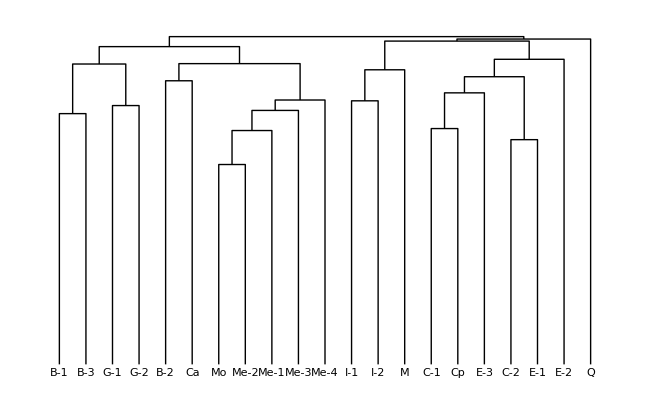

```mathematica
DendrogramPlot[N[citedciting21Data]->ClNames21,DistanceFunction->CosineDistance,Linkage->"Average",LeafLabels->ClNames21]
```

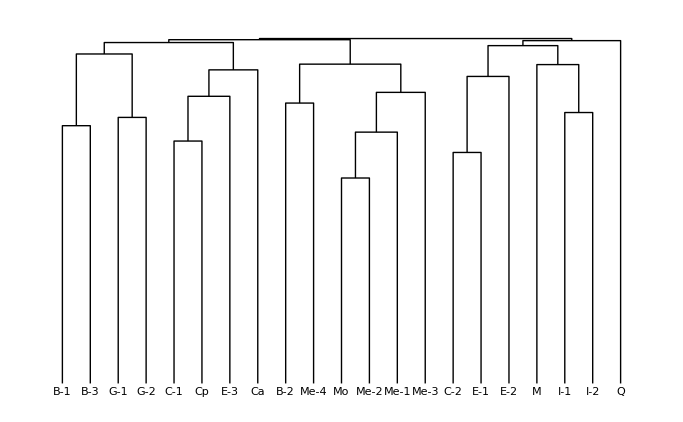

```mathematica
DendrogramPlot[N[citedciting21Data]->ClNames21,DistanceFunction->CosineDistance,Linkage->"Complete",LeafLabels->ClNames21]
```

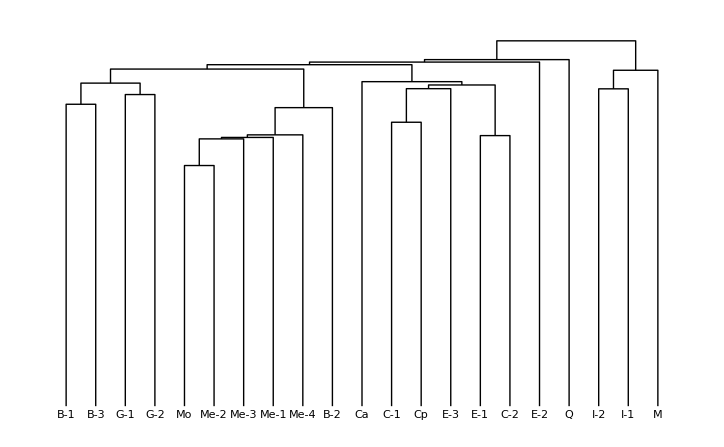

```mathematica
DendrogramPlot[N[citedciting21Data]->ClNames21,DistanceFunction->CosineDistance,Linkage->"Single",LeafLabels->ClNames21]
```

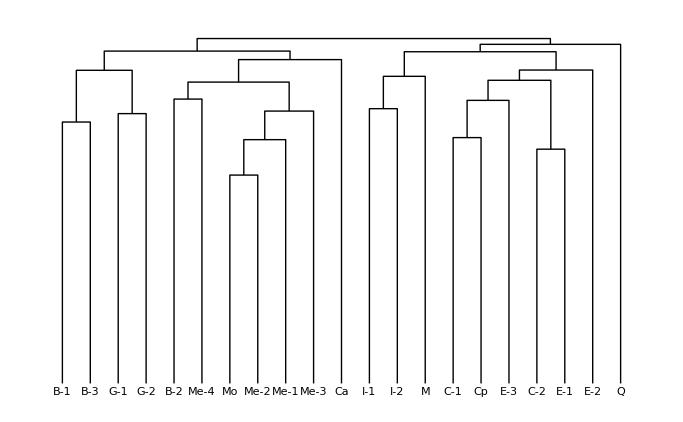

```mathematica
DendrogramPlot[N[citedciting21Data]->ClNames21,DistanceFunction->CosineDistance,Linkage->"WeightedAverage",LeafLabels->ClNames21]
```

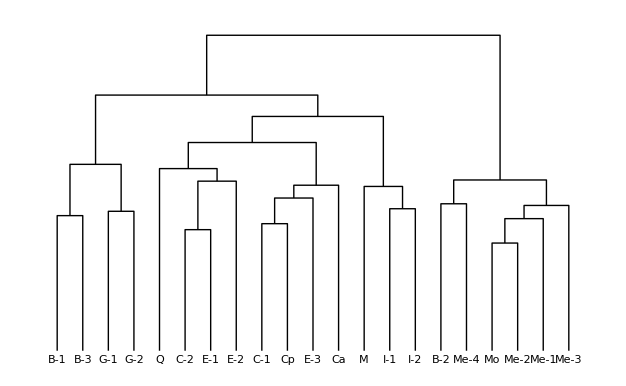

```mathematica
DendrogramPlot[N[citedciting21Data]->ClNames21,DistanceFunction->CosineDistance,Linkage->"Ward",LeafLabels->ClNames21]
```

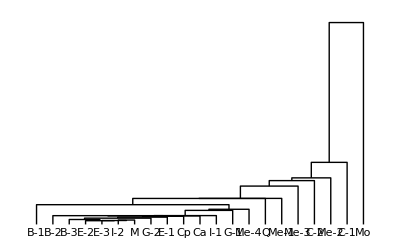

```mathematica
DendrogramPlot[N[citedciting21Data]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Centroid",LeafLabels->ClNames21]
```

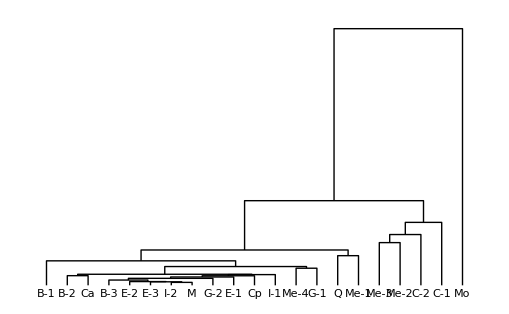

```mathematica
DendrogramPlot[N[citedciting21Data]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Ward",LeafLabels->ClNames21]
```

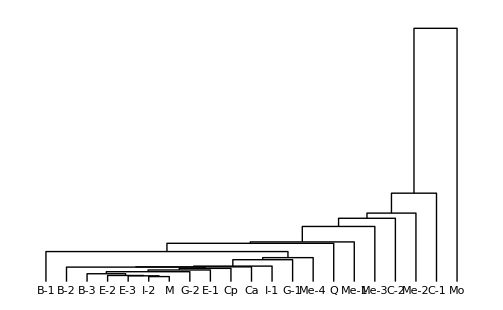

```mathematica
DendrogramPlot[N[citedciting21Data]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Average",LeafLabels->ClNames21]
```

### self-link-reduced cited matrix

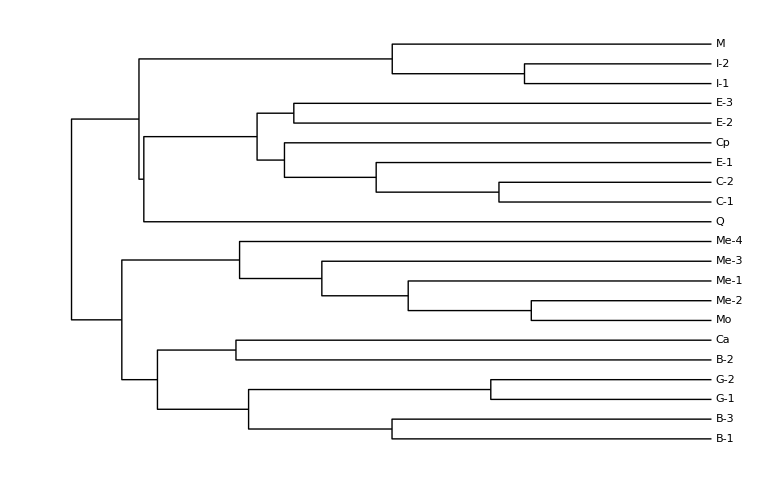

```mathematica
DendrogramPlot[N[citedciting21DataReduceSelf]->ClNames21,DistanceFunction->CosineDistance,Linkage->"Average",LeafLabels->ClNames21,Orientation->Left]
```

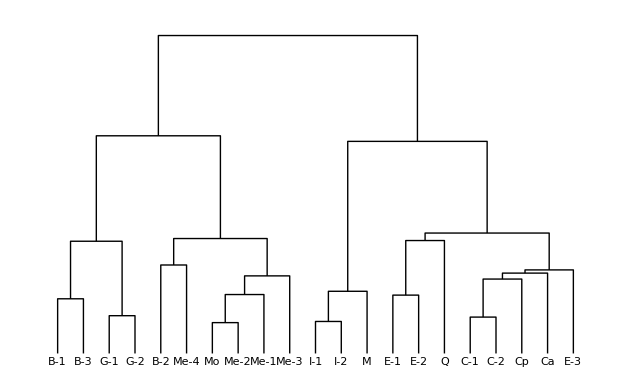

```mathematica
DendrogramPlot[N[citedciting21DataReduceSelf]->ClNames21,DistanceFunction->CosineDistance,Linkage->"Ward",LeafLabels->ClNames21]
```

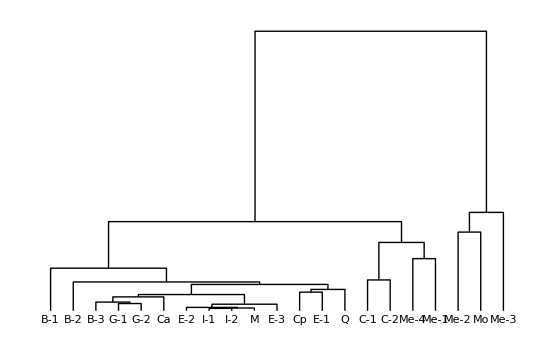

```mathematica
DendrogramPlot[N[citedciting21DataReduceSelf]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Ward",LeafLabels->ClNames21]
```

### self-link-reduced citing matrix

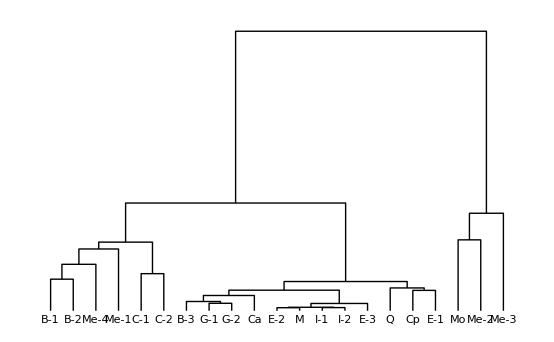

```mathematica
DendrogramPlot[N[citingcited21DataReduceSelf]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Ward",LeafLabels->ClNames21]
```

### self-link-reduced symmetric linkage

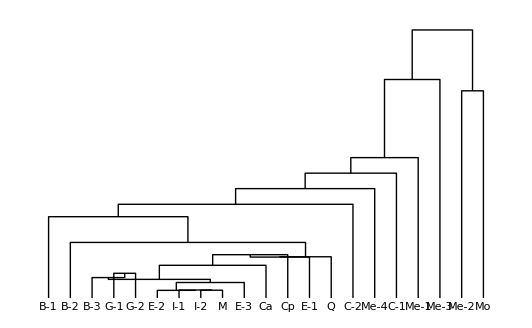

```mathematica
DendrogramPlot[N[symmetricDataReduceSelf21]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Centroid",LeafLabels->ClNames21]
```

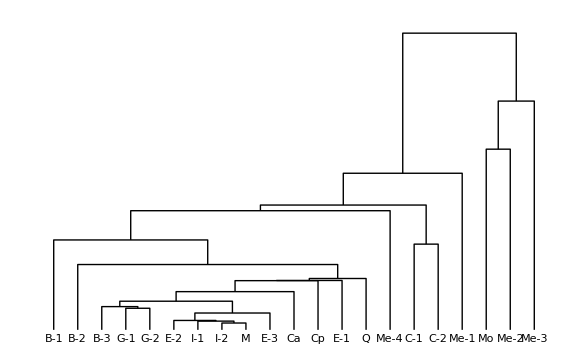

```mathematica
DendrogramPlot[N[symmetricDataReduceSelf21]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Average",LeafLabels->ClNames21]
```

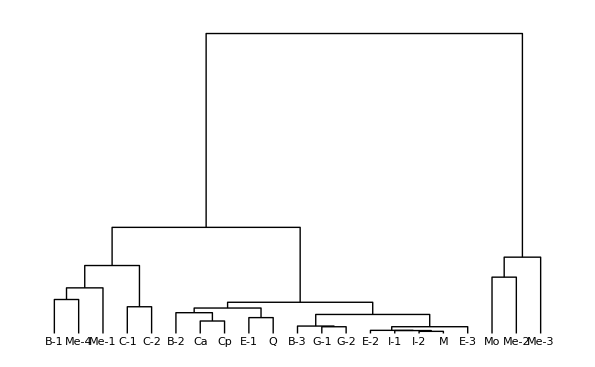

```mathematica
DendrogramPlot[N[symmetricDataReduceSelf21]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Ward",LeafLabels->ClNames21]
```

### symmetric linkage

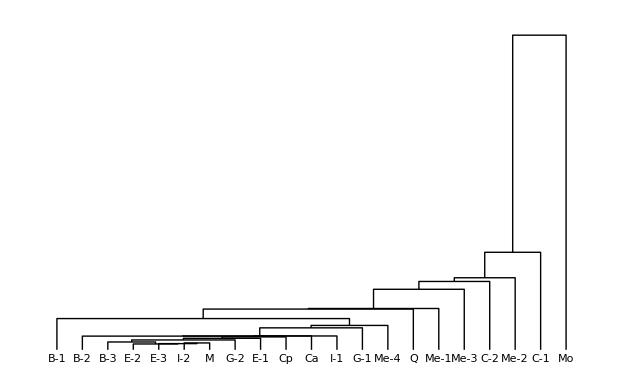

```mathematica
DendrogramPlot[N[symmetricData21]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Centroid",LeafLabels->ClNames21]
```

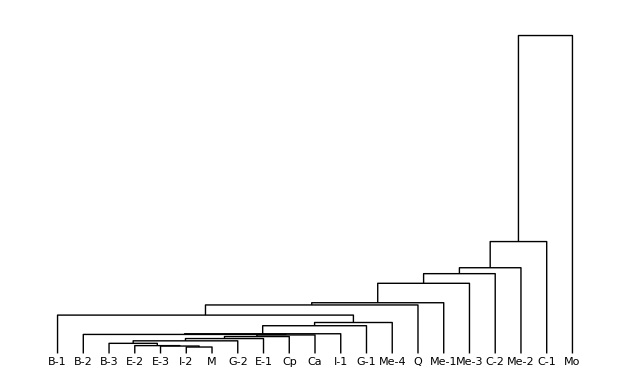

```mathematica
DendrogramPlot[N[symmetricData21]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Average",LeafLabels->ClNames21]
```

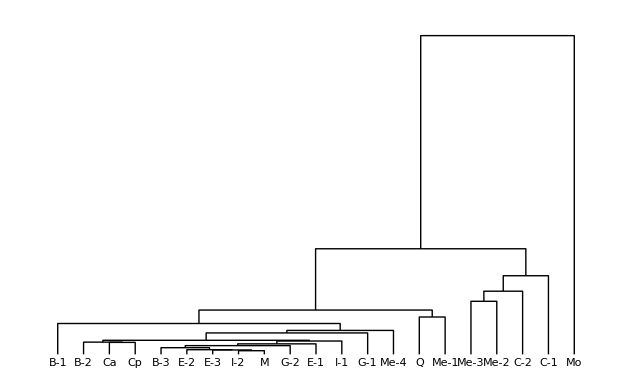

```mathematica
DendrogramPlot[N[symmetricData21]->ClNames21,DistanceFunction->EuclideanDistance,Linkage->"Ward",LeafLabels->ClNames21]
```

### field-power-reduced cited matrix

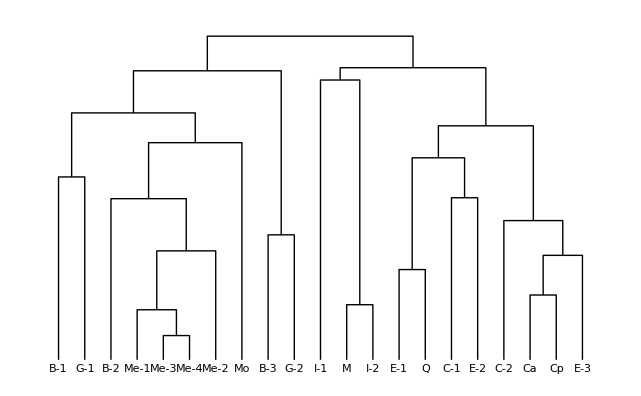

```mathematica
DendrogramPlot[N[citedciting21DataReducedFieldPower]->ClNames21,DistanceFunction->CosineDistance,Linkage->"Average",LeafLabels->ClNames21]
```

```mathematica
PCcitedciting21DataReducedFieldPower=PrincipalComponents[N[citedciting21DataReducedFieldPower]];
```

```mathematica
PCPoint=Map[Point[{#[[1]],#[[2]],#[[3]]}]&,PCcitedciting21DataReducedFieldPower]
```

{Point[{0.0316454,0.0328247,0.0444622}],Point[{0.00739026,0.00903388,0.0117497}],Point[{0.0400394,-0.0316625,0.0574368}],Point[{0.0454588,0.00217064,-0.0791711}],Point[{0.0482756,-0.0784023,-0.147611}],Point[{0.0385428,-0.0261235,-0.0226552}],Point[{0.0429773,-0.0461984,-0.0563402}],Point[{0.0705794,-0.0527234,-0.0205961}],Point[{0.0811246,-0.0333903,0.0094082}],Point[{0.0720904,-0.0431703,-0.00207334}],Point[{0.0321751,-0.0438352,0.01684}],Point[{0.0715153,-0.0326494,0.0398313}],Point[{0.0756938,-0.0264089,0.0250415}],Point[{0.079329,-0.027545,0.0313359}],Point[{0.085133,-0.0287891,0.0263693}],Point[{-0.0551266,0.0713032,0.0410538}],Point[{-0.19549,0.290032,-0.0573595}],Point[{-0.0653279,0.206504,0.0138866}],Point[{-0.0213866,0.0834964,0.0374633}],Point[{-0.564675,-0.187113,0.0134444}],Point[{0.0800362,-0.0373538,0.0174833}]}

```mathematica
Graphics3D[{PCPoint,PointSize->0.05,Point[{0,0,0}]}]
```

-Graphics3D-

## Google score and ranking

### citingcited21Data

```mathematica
citingcited21Data==Transpose[citedciting21Data]
```

True

```mathematica
googlePageScore[citingcited21Data,0.9,50]//TableForm
```

0.605122
0.0275027
0.0315412
0.00696068
0.00583269
0.006662
0.00574055
0.00480321
0.00504787
0.00544505
0.0307881
0.00949626
0.0057755
0.00594073
0.00560392
0.00543552
0.00677956
0.0108562
0.0134521
0.196417
0.00479686 | 0.0523828
0.448951
0.0142316
0.0310719
0.00577671
0.0278513
0.0153479
0.00507703
0.00498623
0.0110003
0.0303723
0.00611853
0.00519453
0.00504498
0.00483134
0.0117213
0.0513306
0.011999
0.0412627
0.210649
0.00479929 | 0.115486
0.0309743
0.49816
0.00777819
0.00621377
0.0072267
0.00554974
0.00487445
0.00765438
0.00527962
0.0763086
0.0136307
0.00535841
0.00569605
0.00489696
0.00664145
0.00888116
0.0241539
0.0186728
0.141778
0.00478441 | 0.00582439
0.0120742
0.00514299
0.654935
0.0623968
0.0208187
0.0276418
0.0182739
0.00511341
0.0115771
0.0100436
0.0061486
0.00533979
0.00486997
0.00488704
0.00764564
0.00869448
0.00960112
0.00700292
0.105574
0.00639432 | 0.00569852
0.00500523
0.00491356
0.0706169
0.677667
0.0107483
0.0121249
0.0350837
0.0101666
0.00779175
0.00992831
0.00679847
0.0112882
0.00781009
0.0081134
0.00707679
0.00521022
0.00603684
0.00538687
0.0548194
0.0377153 | 0.0107436
0.0415278
0.00722322
0.0968008
0.0333332
0.50926
0.0208551
0.0105839
0.00595706
0.0116252
0.0416816
0.00969045
0.00608131
0.00526482
0.00478557
0.0100514
0.0223816
0.0118145
0.00943011
0.124887
0.00602214 | 0.0072707
0.0196427
0.00519489
0.160269
0.0495827
0.0191588
0.49942
0.0240236
0.0113395
0.020808
0.0103144
0.00584438
0.00545596
0.00508665
0.00488289
0.0342434
0.0128295
0.00875432
0.00980496
0.0804968
0.00557694 | 0.00493855
0.00538401
0.00485407
0.0957657
0.189442
0.0119737
0.0346152
0.522898
0.0285324
0.0160596
0.00770346
0.00701991
0.00875566
0.00821804
0.00509984
0.01139
0.00490015
0.00484639
0.00483103
0.0170197
0.00575266 | 0.00609625
0.00517663
0.00876495
0.013904
0.0651682
0.0081699
0.0234067
0.049679
0.612179
0.0327111
0.032062
0.00616838
0.0365158
0.0118123
0.021874
0.0158695
0.00652901
0.0137056
0.00496025
0.0152383
0.0100091 | 0.00741289
0.0310766
0.00510344
0.128041
0.0433719
0.0255144
0.0500238
0.0299544
0.0353051
0.493583
0.0611156
0.00793332
0.0201474
0.00990123
0.00663223
0.00581904
0.00627443
0.00533113
0.00492454
0.0166669
0.00586784 | 0.039174
0.0256885
0.0317372
0.0207063
0.0202137
0.0174206
0.00732364
0.00608561
0.0120616
0.015253
0.595058
0.0433079
0.00764493
0.00709231
0.00508748
0.00772204
0.0241077
0.00945271
0.00767491
0.0777499
0.0194383 | 0.0254758
0.0108873
0.0155134
0.0206722
0.0495434
0.0109564
0.00631052
0.00844109
0.00781967
0.00756322
0.108815
0.585117
0.00606392
0.00523537
0.00592583
0.00584692
0.00559046
0.00646834
0.00599488
0.0888703
0.0128897 | 0.00732746
0.00536284
0.00496222
0.00845229
0.0411804
0.00693453
0.0052858
0.00768186
0.0197931
0.00903012
0.00903782
0.00496222
0.688539
0.0321894
0.0337765
0.0186297
0.0129362
0.0265267
0.005463
0.0443469
0.0075817 | 0.00832362
0.00606271
0.00507162
0.00640339
0.0612539
0.00662019
0.00547425
0.0136507
0.0107084
0.0092218
0.0131242
0.0047619
0.107742
0.628992
0.0211458
0.0110801
0.0291984
0.0102748
0.00627951
0.0276808
0.00692991 | 0.00987527
0.00506683
0.00483227
0.00701366
0.0609151
0.00497301
0.00532484
0.00527793
0.0277955
0.00724822
0.00968763
0.00645072
0.0817674
0.0192576
0.680102
0.00544212
0.00497301
0.00626308
0.00527793
0.0141911
0.0282646 | 0.00508445
0.00693239
0.00502398
0.00690999
0.00732886
0.00569819
0.00944783
0.00536892
0.00585275
0.00488062
0.00562204
0.00498366
0.00751701
0.00534429
0.00485598
0.542095
0.128791
0.0358364
0.0163535
0.180807
0.00526589 | 0.00517043
0.0109288
0.00485253
0.00535029
0.00489994
0.00667066
0.00535447
0.00477724
0.00484417
0.00479676
0.00786695
0.00478142
0.00558871
0.00594425
0.00479258
0.05757
0.583215
0.0446255
0.0295744
0.193616
0.00478003 | 0.00776511
0.00650294
0.00671672
0.00658845
0.0060463
0.00623272
0.00537931
0.00477901
0.00551784
0.00479098
0.00548876
0.00480295
0.00753765
0.00507488
0.00481663
0.0274621
0.0610686
0.591486
0.0108316
0.216329
0.00478243 | 0.014605
0.0271211
0.00862077
0.00773666
0.00569455
0.00637063
0.00636717
0.00477577
0.00481738
0.00480351
0.00673814
0.00489365
0.00496993
0.00497686
0.00482085
0.0236402
0.102128
0.0211924
0.492844
0.238111
0.00477231 | 0.0151806
0.0129944
0.00651756
0.0184135
0.00688186
0.00823633
0.00677999
0.00484575
0.00484994
0.0048055
0.00794372
0.00539324
0.00539617
0.00498325
0.00482772
0.0270061
0.0644567
0.044213
0.0221407
0.718911
0.00522262 | 0.00481702
0.00480729
0.00481053
0.00717391
0.0872143
0.00516391
0.00494021
0.00490455
0.00575718
0.0049856
0.0127371
0.00672328
0.00538436
0.00483647
0.00895374
0.00540705
0.00481378
0.00494994
0.0047619
0.0181025
0.788755
0.0334618 | 0.0227304 | 0.015724 | 0.0716876 | 0.0774319 | 0.0199319 | 0.0205336 | 0.0214446 | 0.0203194 | 0.0149882 | 0.034949 | 0.01732 | 0.0335566 | 0.0184193 | 0.0214451 | 0.0438682 | 0.0886718 | 0.0588465 | 0.0290458 | 0.293624 | 0.0420006

```mathematica
googlePageScore[citingcited21Data,0.9,100]//TableForm
```

0.605122
0.0275027
0.0315412
0.00696068
0.00583269
0.006662
0.00574055
0.00480321
0.00504787
0.00544505
0.0307881
0.00949626
0.0057755
0.00594073
0.00560392
0.00543552
0.00677956
0.0108562
0.0134521
0.196417
0.00479686 | 0.0523828
0.448951
0.0142316
0.0310719
0.00577671
0.0278513
0.0153479
0.00507703
0.00498623
0.0110003
0.0303723
0.00611853
0.00519453
0.00504498
0.00483134
0.0117213
0.0513306
0.011999
0.0412627
0.210649
0.00479929 | 0.115486
0.0309743
0.49816
0.00777819
0.00621377
0.0072267
0.00554974
0.00487445
0.00765438
0.00527962
0.0763086
0.0136307
0.00535841
0.00569605
0.00489696
0.00664145
0.00888116
0.0241539
0.0186728
0.141778
0.00478441 | 0.00582439
0.0120742
0.00514299
0.654935
0.0623968
0.0208187
0.0276418
0.0182739
0.00511341
0.0115771
0.0100436
0.0061486
0.00533979
0.00486997
0.00488704
0.00764564
0.00869448
0.00960112
0.00700292
0.105574
0.00639432 | 0.00569852
0.00500523
0.00491356
0.0706169
0.677667
0.0107483
0.0121249
0.0350837
0.0101666
0.00779175
0.00992831
0.00679847
0.0112882
0.00781009
0.0081134
0.00707679
0.00521022
0.00603684
0.00538687
0.0548194
0.0377153 | 0.0107436
0.0415278
0.00722322
0.0968008
0.0333332
0.50926
0.0208551
0.0105839
0.00595706
0.0116252
0.0416816
0.00969045
0.00608131
0.00526482
0.00478557
0.0100514
0.0223816
0.0118145
0.00943011
0.124887
0.00602214 | 0.0072707
0.0196427
0.00519489
0.160269
0.0495827
0.0191588
0.49942
0.0240236
0.0113395
0.020808
0.0103144
0.00584438
0.00545596
0.00508665
0.00488289
0.0342434
0.0128295
0.00875432
0.00980496
0.0804968
0.00557694 | 0.00493855
0.00538401
0.00485407
0.0957657
0.189442
0.0119737
0.0346152
0.522898
0.0285324
0.0160596
0.00770346
0.00701991
0.00875566
0.00821804
0.00509984
0.01139
0.00490015
0.00484639
0.00483103
0.0170197
0.00575266 | 0.00609625
0.00517663
0.00876495
0.013904
0.0651682
0.0081699
0.0234067
0.049679
0.612179
0.0327111
0.032062
0.00616838
0.0365158
0.0118123
0.021874
0.0158695
0.00652901
0.0137056
0.00496025
0.0152383
0.0100091 | 0.00741289
0.0310766
0.00510344
0.128041
0.0433719
0.0255144
0.0500238
0.0299544
0.0353051
0.493583
0.0611156
0.00793332
0.0201474
0.00990123
0.00663223
0.00581904
0.00627443
0.00533113
0.00492454
0.0166669
0.00586784 | 0.039174
0.0256885
0.0317372
0.0207063
0.0202137
0.0174206
0.00732364
0.00608561
0.0120616
0.015253
0.595058
0.0433079
0.00764493
0.00709231
0.00508748
0.00772204
0.0241077
0.00945271
0.00767491
0.0777499
0.0194383 | 0.0254758
0.0108873
0.0155134
0.0206722
0.0495434
0.0109564
0.00631052
0.00844109
0.00781967
0.00756322
0.108815
0.585117
0.00606392
0.00523537
0.00592583
0.00584692
0.00559046
0.00646834
0.00599488
0.0888703
0.0128897 | 0.00732746
0.00536284
0.00496222
0.00845229
0.0411804
0.00693453
0.0052858
0.00768186
0.0197931
0.00903012
0.00903782
0.00496222
0.688539
0.0321894
0.0337765
0.0186297
0.0129362
0.0265267
0.005463
0.0443469
0.0075817 | 0.00832362
0.00606271
0.00507162
0.00640339
0.0612539
0.00662019
0.00547425
0.0136507
0.0107084
0.0092218
0.0131242
0.0047619
0.107742
0.628992
0.0211458
0.0110801
0.0291984
0.0102748
0.00627951
0.0276808
0.00692991 | 0.00987527
0.00506683
0.00483227
0.00701366
0.0609151
0.00497301
0.00532484
0.00527793
0.0277955
0.00724822
0.00968763
0.00645072
0.0817674
0.0192576
0.680102
0.00544212
0.00497301
0.00626308
0.00527793
0.0141911
0.0282646 | 0.00508445
0.00693239
0.00502398
0.00690999
0.00732886
0.00569819
0.00944783
0.00536892
0.00585275
0.00488062
0.00562204
0.00498366
0.00751701
0.00534429
0.00485598
0.542095
0.128791
0.0358364
0.0163535
0.180807
0.00526589 | 0.00517043
0.0109288
0.00485253
0.00535029
0.00489994
0.00667066
0.00535447
0.00477724
0.00484417
0.00479676
0.00786695
0.00478142
0.00558871
0.00594425
0.00479258
0.05757
0.583215
0.0446255
0.0295744
0.193616
0.00478003 | 0.00776511
0.00650294
0.00671672
0.00658845
0.0060463
0.00623272
0.00537931
0.00477901
0.00551784
0.00479098
0.00548876
0.00480295
0.00753765
0.00507488
0.00481663
0.0274621
0.0610686
0.591486
0.0108316
0.216329
0.00478243 | 0.014605
0.0271211
0.00862077
0.00773666
0.00569455
0.00637063
0.00636717
0.00477577
0.00481738
0.00480351
0.00673814
0.00489365
0.00496993
0.00497686
0.00482085
0.0236402
0.102128
0.0211924
0.492844
0.238111
0.00477231 | 0.0151806
0.0129944
0.00651756
0.0184135
0.00688186
0.00823633
0.00677999
0.00484575
0.00484994
0.0048055
0.00794372
0.00539324
0.00539617
0.00498325
0.00482772
0.0270061
0.0644567
0.044213
0.0221407
0.718911
0.00522262 | 0.00481702
0.00480729
0.00481053
0.00717391
0.0872143
0.00516391
0.00494021
0.00490455
0.00575718
0.0049856
0.0127371
0.00672328
0.00538436
0.00483647
0.00895374
0.00540705
0.00481378
0.00494994
0.0047619
0.0181025
0.788755
0.033462 | 0.0227305 | 0.015724 | 0.0716865 | 0.0774295 | 0.0199318 | 0.0205334 | 0.0214443 | 0.0203192 | 0.0149881 | 0.0349489 | 0.0173199 | 0.0335562 | 0.0184192 | 0.0214449 | 0.0438688 | 0.0886733 | 0.0588474 | 0.0290461 | 0.293628 | 0.0419984

```mathematica
(gps[200]=googlePageScore[citingcited21Data,0.9,200])//TableForm
```

0.605122
0.0275027
0.0315412
0.00696068
0.00583269
0.006662
0.00574055
0.00480321
0.00504787
0.00544505
0.0307881
0.00949626
0.0057755
0.00594073
0.00560392
0.00543552
0.00677956
0.0108562
0.0134521
0.196417
0.00479686 | 0.0523828
0.448951
0.0142316
0.0310719
0.00577671
0.0278513
0.0153479
0.00507703
0.00498623
0.0110003
0.0303723
0.00611853
0.00519453
0.00504498
0.00483134
0.0117213
0.0513306
0.011999
0.0412627
0.210649
0.00479929 | 0.115486
0.0309743
0.49816
0.00777819
0.00621377
0.0072267
0.00554974
0.00487445
0.00765438
0.00527962
0.0763086
0.0136307
0.00535841
0.00569605
0.00489696
0.00664145
0.00888116
0.0241539
0.0186728
0.141778
0.00478441 | 0.00582439
0.0120742
0.00514299
0.654935
0.0623968
0.0208187
0.0276418
0.0182739
0.00511341
0.0115771
0.0100436
0.0061486
0.00533979
0.00486997
0.00488704
0.00764564
0.00869448
0.00960112
0.00700292
0.105574
0.00639432 | 0.00569852
0.00500523
0.00491356
0.0706169
0.677667
0.0107483
0.0121249
0.0350837
0.0101666
0.00779175
0.00992831
0.00679847
0.0112882
0.00781009
0.0081134
0.00707679
0.00521022
0.00603684
0.00538687
0.0548194
0.0377153 | 0.0107436
0.0415278
0.00722322
0.0968008
0.0333332
0.50926
0.0208551
0.0105839
0.00595706
0.0116252
0.0416816
0.00969045
0.00608131
0.00526482
0.00478557
0.0100514
0.0223816
0.0118145
0.00943011
0.124887
0.00602214 | 0.0072707
0.0196427
0.00519489
0.160269
0.0495827
0.0191588
0.49942
0.0240236
0.0113395
0.020808
0.0103144
0.00584438
0.00545596
0.00508665
0.00488289
0.0342434
0.0128295
0.00875432
0.00980496
0.0804968
0.00557694 | 0.00493855
0.00538401
0.00485407
0.0957657
0.189442
0.0119737
0.0346152
0.522898
0.0285324
0.0160596
0.00770346
0.00701991
0.00875566
0.00821804
0.00509984
0.01139
0.00490015
0.00484639
0.00483103
0.0170197
0.00575266 | 0.00609625
0.00517663
0.00876495
0.013904
0.0651682
0.0081699
0.0234067
0.049679
0.612179
0.0327111
0.032062
0.00616838
0.0365158
0.0118123
0.021874
0.0158695
0.00652901
0.0137056
0.00496025
0.0152383
0.0100091 | 0.00741289
0.0310766
0.00510344
0.128041
0.0433719
0.0255144
0.0500238
0.0299544
0.0353051
0.493583
0.0611156
0.00793332
0.0201474
0.00990123
0.00663223
0.00581904
0.00627443
0.00533113
0.00492454
0.0166669
0.00586784 | 0.039174
0.0256885
0.0317372
0.0207063
0.0202137
0.0174206
0.00732364
0.00608561
0.0120616
0.015253
0.595058
0.0433079
0.00764493
0.00709231
0.00508748
0.00772204
0.0241077
0.00945271
0.00767491
0.0777499
0.0194383 | 0.0254758
0.0108873
0.0155134
0.0206722
0.0495434
0.0109564
0.00631052
0.00844109
0.00781967
0.00756322
0.108815
0.585117
0.00606392
0.00523537
0.00592583
0.00584692
0.00559046
0.00646834
0.00599488
0.0888703
0.0128897 | 0.00732746
0.00536284
0.00496222
0.00845229
0.0411804
0.00693453
0.0052858
0.00768186
0.0197931
0.00903012
0.00903782
0.00496222
0.688539
0.0321894
0.0337765
0.0186297
0.0129362
0.0265267
0.005463
0.0443469
0.0075817 | 0.00832362
0.00606271
0.00507162
0.00640339
0.0612539
0.00662019
0.00547425
0.0136507
0.0107084
0.0092218
0.0131242
0.0047619
0.107742
0.628992
0.0211458
0.0110801
0.0291984
0.0102748
0.00627951
0.0276808
0.00692991 | 0.00987527
0.00506683
0.00483227
0.00701366
0.0609151
0.00497301
0.00532484
0.00527793
0.0277955
0.00724822
0.00968763
0.00645072
0.0817674
0.0192576
0.680102
0.00544212
0.00497301
0.00626308
0.00527793
0.0141911
0.0282646 | 0.00508445
0.00693239
0.00502398
0.00690999
0.00732886
0.00569819
0.00944783
0.00536892
0.00585275
0.00488062
0.00562204
0.00498366
0.00751701
0.00534429
0.00485598
0.542095
0.128791
0.0358364
0.0163535
0.180807
0.00526589 | 0.00517043
0.0109288
0.00485253
0.00535029
0.00489994
0.00667066
0.00535447
0.00477724
0.00484417
0.00479676
0.00786695
0.00478142
0.00558871
0.00594425
0.00479258
0.05757
0.583215
0.0446255
0.0295744
0.193616
0.00478003 | 0.00776511
0.00650294
0.00671672
0.00658845
0.0060463
0.00623272
0.00537931
0.00477901
0.00551784
0.00479098
0.00548876
0.00480295
0.00753765
0.00507488
0.00481663
0.0274621
0.0610686
0.591486
0.0108316
0.216329
0.00478243 | 0.014605
0.0271211
0.00862077
0.00773666
0.00569455
0.00637063
0.00636717
0.00477577
0.00481738
0.00480351
0.00673814
0.00489365
0.00496993
0.00497686
0.00482085
0.0236402
0.102128
0.0211924
0.492844
0.238111
0.00477231 | 0.0151806
0.0129944
0.00651756
0.0184135
0.00688186
0.00823633
0.00677999
0.00484575
0.00484994
0.0048055
0.00794372
0.00539324
0.00539617
0.00498325
0.00482772
0.0270061
0.0644567
0.044213
0.0221407
0.718911
0.00522262 | 0.00481702
0.00480729
0.00481053
0.00717391
0.0872143
0.00516391
0.00494021
0.00490455
0.00575718
0.0049856
0.0127371
0.00672328
0.00538436
0.00483647
0.00895374
0.00540705
0.00481378
0.00494994
0.0047619
0.0181025
0.788755
0.033462 | 0.0227305 | 0.015724 | 0.0716865 | 0.0774295 | 0.0199318 | 0.0205334 | 0.0214443 | 0.0203192 | 0.0149881 | 0.0349489 | 0.0173199 | 0.0335562 | 0.0184192 | 0.0214449 | 0.0438688 | 0.0886733 | 0.0588474 | 0.0290461 | 0.293628 | 0.0419984

```mathematica
gps[200][[2]]//Tr
```

1.

OK.

```mathematica
gps[200][[2]].gps[200][[1]]-gps[200][[2]]
```

{6.93889×10^-18,6.93889×10^-18,0.,-1.38778×10^-17,1.38778×10^-17,0.,-3.46945×10^-18,-1.04083×10^-17,0.,1.73472×10^-18,6.93889×10^-18,0.,-6.93889×10^-18,3.46945×10^-18,0.,0.,0.,6.93889×10^-18,-3.46945×10^-18,0.,0.}

OK.

```mathematica
god[200]=Ordering[gps[200][[2]],All,Greater]
```

{20,17,5,4,18,16,21,11,13,1,19,2,15,8,7,9,6,14,12,3,10}

```mathematica
ranking["G"]=Inner[List,ClNames21[[god[200]]],gps[200][[2]][[god[200]]],List]
```

{{Mo,0.293628},{Me-2,0.0886733},{C-2,0.0774295},{C-1,0.0716865},{Me-3,0.0588474},{Me-1,0.0438688},{Q,0.0419984},{G-1,0.0349489},{I-1,0.0335562},{B-1,0.033462},{Me-4,0.0290461},{B-2,0.0227305},{M,0.0214449},{E-1,0.0214443},{Cp,0.0205334},{E-2,0.0203192},{Ca,0.0199318},{I-2,0.0184192},{G-2,0.0173199},{B-3,0.015724},{E-3,0.0149881}}

for JSIMS ->

```mathematica
(jranking["G"]=Inner[List,Flatten[jFieldName21[[god[200]]]],Round[gps[200][[2]][[god[200]]],0.0001],List])//TableForm
```

生化学・生理学 | 0.2936
臨床医学2 | 0.0887
物性物理 | 0.0774
化学 | 0.0717
心理・神経科学 | 0.0588
臨床医学1 | 0.0439
素粒子・天体物理 | 0.042
気象・環境 | 0.0349
電子情報工学 | 0.0336
動植物学 | 0.0335
獣医学・感染症 | 0.029
農学・食品学 | 0.0227
数学 | 0.0214
金属・セラミックス | 0.0214
応用化学 | 0.0205
機械・土木建築 | 0.0203
分析化学 | 0.0199
数理工学 | 0.0184
地球科学 | 0.0173
水産・海洋 | 0.0157
化学工学・エネルギー工学 | 0.015

compare with citedParIssues

```mathematica
ranking["C"]=Sort[citedParIssues,#2[[2]]<#1[[2]]&]
```

{{Mo,4.0752},{Me-3,2.49018},{Q,2.45296},{Me-2,2.35379},{C-1,2.0823},{B-1,1.64912},{Ca,1.57842},{Me-4,1.55153},{Me-1,1.49714},{C-2,1.42033},{G-1,1.40688},{G-2,1.37796},{Cp,1.32875},{B-2,1.20624},{B-3,1.20191},{E-1,0.817733},{I-1,0.752204},{E-2,0.731282},{E-3,0.660304},{I-2,0.528489},{M,0.496296}}

compare with citedParIssuesDropSelf

```mathematica
ranking["C","D"]=Sort[citedParIssuesDropSelf,#2[[2]]<#1[[2]]&]
```

{{Mo,1.19382},{Me-2,0.954801},{Me-3,0.785498},{Me-4,0.578534},{Ca,0.528888},{B-2,0.526809},{Me-1,0.51385},{Cp,0.496836},{G-1,0.449988},{B-3,0.441277},{C-1,0.428055},{B-1,0.410481},{C-2,0.3711},{G-2,0.321773},{E-1,0.304917},{Q,0.263445},{E-3,0.261884},{E-2,0.243432},{I-2,0.179859},{I-1,0.144259},{M,0.124042}}

### citingcited21DataZeroSelf

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
googlePageScore[citingcited21DataZeroSelf,0.9,50]//TableForm
```

0.0047619
0.0730662
0.0851962
0.0113661
0.00797813
0.010469
0.00770137
0.00488597
0.00562084
0.0068138
0.0829344
0.018982
0.00780635
0.00830262
0.00729099
0.00678517
0.0108222
0.0230667
0.0308639
0.580419
0.00486689 | 0.0987894
0.0047619
0.0234598
0.0567111
0.00676563
0.0503519
0.0256639
0.00538411
0.00520483
0.0170795
0.0553296
0.00744057
0.00561612
0.00532084
0.004899
0.0185032
0.0967118
0.0190516
0.0768328
0.411286
0.00483573 | 0.249847
0.0627822
0.0047619
0.0114384
0.00797557
0.0102177
0.00650575
0.00501103
0.0111643
0.00590786
0.163128
0.0243927
0.00608225
0.00682961
0.00506085
0.00892223
0.0138797
0.0476855
0.0355533
0.308042
0.00481173 | 0.00858951
0.0311044
0.00613476
0.0047619
0.212391
0.0626063
0.0871866
0.0534389
0.00602821
0.0293135
0.0237893
0.00975747
0.00684373
0.00515122
0.00521269
0.0151505
0.018929
0.0221951
0.0128351
0.367938
0.0106427 | 0.00847382
0.00572621
0.00536294
0.265752
0.0047619
0.0284864
0.033942
0.12493
0.0261814
0.0167695
0.0252369
0.012833
0.0306264
0.0168421
0.0180442
0.013936
0.0065386
0.0098146
0.00723871
0.203144
0.135359 | 0.0183738
0.0884258
0.0103628
0.214205
0.0697785
0.0047619
0.0413834
0.0180103
0.00748159
0.0203799
0.0887759
0.0159772
0.00776433
0.00590633
0.00481576
0.0167985
0.044857
0.0208107
0.0153848
0.278117
0.00762969 | 0.0103323
0.0378025
0.00572329
0.350041
0.10428
0.036728
0.0047619
0.0475295
0.0193665
0.0403898
0.0170903
0.00716537
0.00630295
0.00548295
0.00503053
0.0702211
0.0226748
0.0136265
0.0159592
0.17292
0.00657158 | 0.00517824
0.00622812
0.00497912
0.219245
0.440027
0.0217591
0.0751219
0.0047619
0.0607856
0.031389
0.0116947
0.0100837
0.0141746
0.0129075
0.00555836
0.0203834
0.00508773
0.00496102
0.00492482
0.0336517
0.00709698 | 0.00886643
0.00603764
0.0170755
0.0328834
0.190575
0.0152451
0.0621143
0.142929
0.0047619
0.090735
0.0887382
0.00908829
0.102438
0.0264493
0.0573996
0.0389293
0.0101976
0.0322733
0.00537204
0.036988
0.0209027 | 0.0105645
0.0623602
0.00550947
0.274598
0.0892726
0.0501855
0.103832
0.0599039
0.0716158
0.0047619
0.128111
0.0117036
0.038438
0.016011
0.00885573
0.0070758
0.00807256
0.00600785
0.00511789
0.03082
0.0071826 | 0.104763
0.0655744
0.0831521
0.0510964
0.0496648
0.0415482
0.0122063
0.00860859
0.0259747
0.0352491
0.0047619
0.116776
0.01314
0.0115341
0.00570802
0.013364
0.0609808
0.0183934
0.0132271
0.216865
0.0474116 | 0.0630844
0.0220087
0.0350341
0.0495592
0.13085
0.0222031
0.00912221
0.0151211
0.0133714
0.0126493
0.297735
0.0047619
0.00842789
0.00609499
0.00803908
0.00781689
0.00709481
0.00956657
0.00823348
0.241579
0.0276466 | 0.0154407
0.00726324
0.00559568
0.0201227
0.156349
0.0138052
0.00694256
0.0169158
0.0673274
0.0225278
0.0225599
0.00559568
0.0047619
0.118925
0.125532
0.062485
0.0387865
0.0953552
0.00768013
0.169529
0.0164989 | 0.0163859
0.00900719
0.00577269
0.010119
0.189128
0.0108266
0.0070867
0.0337713
0.0241689
0.0193172
0.032053
0.0047619
0.340847
0.0047619
0.0582323
0.0253819
0.0845126
0.0227538
0.00971473
0.0795597
0.0118374 | 0.0252463
0.00598345
0.0050438
0.0137826
0.229715
0.00560759
0.00701707
0.00682914
0.0970359
0.0147222
0.0244946
0.0115274
0.31325
0.0628325
0.0047619
0.0074869
0.00560759
0.0107757
0.00682914
0.042536
0.0989152 | 0.00556235
0.0101482
0.00541227
0.0100926
0.0111321
0.00708542
0.0163906
0.0062683
0.00746896
0.00505651
0.00689642
0.00531221
0.011599
0.00620715
0.00499537
0.0047619
0.312555
0.081877
0.0335279
0.441638
0.0060126 | 0.00590534
0.0220228
0.00501557
0.00640877
0.00514825
0.0101045
0.00642048
0.00480483
0.00499215
0.00485947
0.0134528
0.00481654
0.0070761
0.00807124
0.00484776
0.15257
0.0047619
0.116339
0.0742112
0.533359
0.00481264 | 0.0133897
0.00976368
0.0103778
0.0100093
0.00845182
0.00898737
0.00653562
0.00481104
0.0069336
0.00484543
0.00685007
0.00487982
0.0127362
0.00566104
0.00491913
0.0699766
0.166524
0.0047619
0.0221993
0.612566
0.00482086 | 0.026268
0.0536147
0.0131932
0.0112615
0.00679965
0.00827682
0.00826924
0.00479221
0.00488311
0.00485281
0.0090798
0.00504976
0.00521642
0.00523157
0.00489068
0.0460091
0.217498
0.040661
0.0047619
0.514606
0.00478463 | 0.0552153
0.0446285
0.0132638
0.0708712
0.015028
0.0215871
0.0145347
0.00516792
0.00518822
0.00497303
0.0201702
0.00781919
0.0078334
0.00583378
0.00508063
0.112482
0.29384
0.195808
0.0889206
0.0047619
0.00699295 | 0.00518948
0.00511403
0.00513918
0.0234747
0.644443
0.0078807
0.00614524
0.00586858
0.0124834
0.00649737
0.0666349
0.0199786
0.00959101
0.00534039
0.0372829
0.00976707
0.00516433
0.0062207
0.0047619
0.108261
0.0047619
0.032461 | 0.0314529 | 0.0144058 | 0.0631695 | 0.056729 | 0.0208248 | 0.0208289 | 0.0191482 | 0.0119685 | 0.0117392 | 0.0293267 | 0.0114237 | 0.0174253 | 0.00995986 | 0.00970538 | 0.0689401 | 0.139733 | 0.0871612 | 0.0466687 | 0.28059 | 0.0163387

```mathematica
googlePageScore[citingcited21DataZeroSelf,0.9,100]//TableForm
```

0.0047619
0.0730662
0.0851962
0.0113661
0.00797813
0.010469
0.00770137
0.00488597
0.00562084
0.0068138
0.0829344
0.018982
0.00780635
0.00830262
0.00729099
0.00678517
0.0108222
0.0230667
0.0308639
0.580419
0.00486689 | 0.0987894
0.0047619
0.0234598
0.0567111
0.00676563
0.0503519
0.0256639
0.00538411
0.00520483
0.0170795
0.0553296
0.00744057
0.00561612
0.00532084
0.004899
0.0185032
0.0967118
0.0190516
0.0768328
0.411286
0.00483573 | 0.249847
0.0627822
0.0047619
0.0114384
0.00797557
0.0102177
0.00650575
0.00501103
0.0111643
0.00590786
0.163128
0.0243927
0.00608225
0.00682961
0.00506085
0.00892223
0.0138797
0.0476855
0.0355533
0.308042
0.00481173 | 0.00858951
0.0311044
0.00613476
0.0047619
0.212391
0.0626063
0.0871866
0.0534389
0.00602821
0.0293135
0.0237893
0.00975747
0.00684373
0.00515122
0.00521269
0.0151505
0.018929
0.0221951
0.0128351
0.367938
0.0106427 | 0.00847382
0.00572621
0.00536294
0.265752
0.0047619
0.0284864
0.033942
0.12493
0.0261814
0.0167695
0.0252369
0.012833
0.0306264
0.0168421
0.0180442
0.013936
0.0065386
0.0098146
0.00723871
0.203144
0.135359 | 0.0183738
0.0884258
0.0103628
0.214205
0.0697785
0.0047619
0.0413834
0.0180103
0.00748159
0.0203799
0.0887759
0.0159772
0.00776433
0.00590633
0.00481576
0.0167985
0.044857
0.0208107
0.0153848
0.278117
0.00762969 | 0.0103323
0.0378025
0.00572329
0.350041
0.10428
0.036728
0.0047619
0.0475295
0.0193665
0.0403898
0.0170903
0.00716537
0.00630295
0.00548295
0.00503053
0.0702211
0.0226748
0.0136265
0.0159592
0.17292
0.00657158 | 0.00517824
0.00622812
0.00497912
0.219245
0.440027
0.0217591
0.0751219
0.0047619
0.0607856
0.031389
0.0116947
0.0100837
0.0141746
0.0129075
0.00555836
0.0203834
0.00508773
0.00496102
0.00492482
0.0336517
0.00709698 | 0.00886643
0.00603764
0.0170755
0.0328834
0.190575
0.0152451
0.0621143
0.142929
0.0047619
0.090735
0.0887382
0.00908829
0.102438
0.0264493
0.0573996
0.0389293
0.0101976
0.0322733
0.00537204
0.036988
0.0209027 | 0.0105645
0.0623602
0.00550947
0.274598
0.0892726
0.0501855
0.103832
0.0599039
0.0716158
0.0047619
0.128111
0.0117036
0.038438
0.016011
0.00885573
0.0070758
0.00807256
0.00600785
0.00511789
0.03082
0.0071826 | 0.104763
0.0655744
0.0831521
0.0510964
0.0496648
0.0415482
0.0122063
0.00860859
0.0259747
0.0352491
0.0047619
0.116776
0.01314
0.0115341
0.00570802
0.013364
0.0609808
0.0183934
0.0132271
0.216865
0.0474116 | 0.0630844
0.0220087
0.0350341
0.0495592
0.13085
0.0222031
0.00912221
0.0151211
0.0133714
0.0126493
0.297735
0.0047619
0.00842789
0.00609499
0.00803908
0.00781689
0.00709481
0.00956657
0.00823348
0.241579
0.0276466 | 0.0154407
0.00726324
0.00559568
0.0201227
0.156349
0.0138052
0.00694256
0.0169158
0.0673274
0.0225278
0.0225599
0.00559568
0.0047619
0.118925
0.125532
0.062485
0.0387865
0.0953552
0.00768013
0.169529
0.0164989 | 0.0163859
0.00900719
0.00577269
0.010119
0.189128
0.0108266
0.0070867
0.0337713
0.0241689
0.0193172
0.032053
0.0047619
0.340847
0.0047619
0.0582323
0.0253819
0.0845126
0.0227538
0.00971473
0.0795597
0.0118374 | 0.0252463
0.00598345
0.0050438
0.0137826
0.229715
0.00560759
0.00701707
0.00682914
0.0970359
0.0147222
0.0244946
0.0115274
0.31325
0.0628325
0.0047619
0.0074869
0.00560759
0.0107757
0.00682914
0.042536
0.0989152 | 0.00556235
0.0101482
0.00541227
0.0100926
0.0111321
0.00708542
0.0163906
0.0062683
0.00746896
0.00505651
0.00689642
0.00531221
0.011599
0.00620715
0.00499537
0.0047619
0.312555
0.081877
0.0335279
0.441638
0.0060126 | 0.00590534
0.0220228
0.00501557
0.00640877
0.00514825
0.0101045
0.00642048
0.00480483
0.00499215
0.00485947
0.0134528
0.00481654
0.0070761
0.00807124
0.00484776
0.15257
0.0047619
0.116339
0.0742112
0.533359
0.00481264 | 0.0133897
0.00976368
0.0103778
0.0100093
0.00845182
0.00898737
0.00653562
0.00481104
0.0069336
0.00484543
0.00685007
0.00487982
0.0127362
0.00566104
0.00491913
0.0699766
0.166524
0.0047619
0.0221993
0.612566
0.00482086 | 0.026268
0.0536147
0.0131932
0.0112615
0.00679965
0.00827682
0.00826924
0.00479221
0.00488311
0.00485281
0.0090798
0.00504976
0.00521642
0.00523157
0.00489068
0.0460091
0.217498
0.040661
0.0047619
0.514606
0.00478463 | 0.0552153
0.0446285
0.0132638
0.0708712
0.015028
0.0215871
0.0145347
0.00516792
0.00518822
0.00497303
0.0201702
0.00781919
0.0078334
0.00583378
0.00508063
0.112482
0.29384
0.195808
0.0889206
0.0047619
0.00699295 | 0.00518948
0.00511403
0.00513918
0.0234747
0.644443
0.0078807
0.00614524
0.00586858
0.0124834
0.00649737
0.0666349
0.0199786
0.00959101
0.00534039
0.0372829
0.00976707
0.00516433
0.0062207
0.0047619
0.108261
0.0047619
0.032461 | 0.0314529 | 0.0144058 | 0.0631695 | 0.056729 | 0.0208248 | 0.0208289 | 0.0191482 | 0.0119685 | 0.0117392 | 0.0293267 | 0.0114237 | 0.0174253 | 0.00995986 | 0.00970538 | 0.0689401 | 0.139733 | 0.0871612 | 0.0466687 | 0.28059 | 0.0163387

```mathematica
(gps[200]=googlePageScore[citingcited21DataZeroSelf,0.9,200])//TableForm
```

0.0047619
0.0730662
0.0851962
0.0113661
0.00797813
0.010469
0.00770137
0.00488597
0.00562084
0.0068138
0.0829344
0.018982
0.00780635
0.00830262
0.00729099
0.00678517
0.0108222
0.0230667
0.0308639
0.580419
0.00486689 | 0.0987894
0.0047619
0.0234598
0.0567111
0.00676563
0.0503519
0.0256639
0.00538411
0.00520483
0.0170795
0.0553296
0.00744057
0.00561612
0.00532084
0.004899
0.0185032
0.0967118
0.0190516
0.0768328
0.411286
0.00483573 | 0.249847
0.0627822
0.0047619
0.0114384
0.00797557
0.0102177
0.00650575
0.00501103
0.0111643
0.00590786
0.163128
0.0243927
0.00608225
0.00682961
0.00506085
0.00892223
0.0138797
0.0476855
0.0355533
0.308042
0.00481173 | 0.00858951
0.0311044
0.00613476
0.0047619
0.212391
0.0626063
0.0871866
0.0534389
0.00602821
0.0293135
0.0237893
0.00975747
0.00684373
0.00515122
0.00521269
0.0151505
0.018929
0.0221951
0.0128351
0.367938
0.0106427 | 0.00847382
0.00572621
0.00536294
0.265752
0.0047619
0.0284864
0.033942
0.12493
0.0261814
0.0167695
0.0252369
0.012833
0.0306264
0.0168421
0.0180442
0.013936
0.0065386
0.0098146
0.00723871
0.203144
0.135359 | 0.0183738
0.0884258
0.0103628
0.214205
0.0697785
0.0047619
0.0413834
0.0180103
0.00748159
0.0203799
0.0887759
0.0159772
0.00776433
0.00590633
0.00481576
0.0167985
0.044857
0.0208107
0.0153848
0.278117
0.00762969 | 0.0103323
0.0378025
0.00572329
0.350041
0.10428
0.036728
0.0047619
0.0475295
0.0193665
0.0403898
0.0170903
0.00716537
0.00630295
0.00548295
0.00503053
0.0702211
0.0226748
0.0136265
0.0159592
0.17292
0.00657158 | 0.00517824
0.00622812
0.00497912
0.219245
0.440027
0.0217591
0.0751219
0.0047619
0.0607856
0.031389
0.0116947
0.0100837
0.0141746
0.0129075
0.00555836
0.0203834
0.00508773
0.00496102
0.00492482
0.0336517
0.00709698 | 0.00886643
0.00603764
0.0170755
0.0328834
0.190575
0.0152451
0.0621143
0.142929
0.0047619
0.090735
0.0887382
0.00908829
0.102438
0.0264493
0.0573996
0.0389293
0.0101976
0.0322733
0.00537204
0.036988
0.0209027 | 0.0105645
0.0623602
0.00550947
0.274598
0.0892726
0.0501855
0.103832
0.0599039
0.0716158
0.0047619
0.128111
0.0117036
0.038438
0.016011
0.00885573
0.0070758
0.00807256
0.00600785
0.00511789
0.03082
0.0071826 | 0.104763
0.0655744
0.0831521
0.0510964
0.0496648
0.0415482
0.0122063
0.00860859
0.0259747
0.0352491
0.0047619
0.116776
0.01314
0.0115341
0.00570802
0.013364
0.0609808
0.0183934
0.0132271
0.216865
0.0474116 | 0.0630844
0.0220087
0.0350341
0.0495592
0.13085
0.0222031
0.00912221
0.0151211
0.0133714
0.0126493
0.297735
0.0047619
0.00842789
0.00609499
0.00803908
0.00781689
0.00709481
0.00956657
0.00823348
0.241579
0.0276466 | 0.0154407
0.00726324
0.00559568
0.0201227
0.156349
0.0138052
0.00694256
0.0169158
0.0673274
0.0225278
0.0225599
0.00559568
0.0047619
0.118925
0.125532
0.062485
0.0387865
0.0953552
0.00768013
0.169529
0.0164989 | 0.0163859
0.00900719
0.00577269
0.010119
0.189128
0.0108266
0.0070867
0.0337713
0.0241689
0.0193172
0.032053
0.0047619
0.340847
0.0047619
0.0582323
0.0253819
0.0845126
0.0227538
0.00971473
0.0795597
0.0118374 | 0.0252463
0.00598345
0.0050438
0.0137826
0.229715
0.00560759
0.00701707
0.00682914
0.0970359
0.0147222
0.0244946
0.0115274
0.31325
0.0628325
0.0047619
0.0074869
0.00560759
0.0107757
0.00682914
0.042536
0.0989152 | 0.00556235
0.0101482
0.00541227
0.0100926
0.0111321
0.00708542
0.0163906
0.0062683
0.00746896
0.00505651
0.00689642
0.00531221
0.011599
0.00620715
0.00499537
0.0047619
0.312555
0.081877
0.0335279
0.441638
0.0060126 | 0.00590534
0.0220228
0.00501557
0.00640877
0.00514825
0.0101045
0.00642048
0.00480483
0.00499215
0.00485947
0.0134528
0.00481654
0.0070761
0.00807124
0.00484776
0.15257
0.0047619
0.116339
0.0742112
0.533359
0.00481264 | 0.0133897
0.00976368
0.0103778
0.0100093
0.00845182
0.00898737
0.00653562
0.00481104
0.0069336
0.00484543
0.00685007
0.00487982
0.0127362
0.00566104
0.00491913
0.0699766
0.166524
0.0047619
0.0221993
0.612566
0.00482086 | 0.026268
0.0536147
0.0131932
0.0112615
0.00679965
0.00827682
0.00826924
0.00479221
0.00488311
0.00485281
0.0090798
0.00504976
0.00521642
0.00523157
0.00489068
0.0460091
0.217498
0.040661
0.0047619
0.514606
0.00478463 | 0.0552153
0.0446285
0.0132638
0.0708712
0.015028
0.0215871
0.0145347
0.00516792
0.00518822
0.00497303
0.0201702
0.00781919
0.0078334
0.00583378
0.00508063
0.112482
0.29384
0.195808
0.0889206
0.0047619
0.00699295 | 0.00518948
0.00511403
0.00513918
0.0234747
0.644443
0.0078807
0.00614524
0.00586858
0.0124834
0.00649737
0.0666349
0.0199786
0.00959101
0.00534039
0.0372829
0.00976707
0.00516433
0.0062207
0.0047619
0.108261
0.0047619
0.032461 | 0.0314529 | 0.0144058 | 0.0631695 | 0.056729 | 0.0208248 | 0.0208289 | 0.0191482 | 0.0119685 | 0.0117392 | 0.0293267 | 0.0114237 | 0.0174253 | 0.00995986 | 0.00970538 | 0.0689401 | 0.139733 | 0.0871612 | 0.0466687 | 0.28059 | 0.0163387

```mathematica
god[200]=Ordering[gps[200][[2]],All,Greater]
```

{20,17,18,16,4,5,19,1,2,11,7,6,8,13,21,3,9,10,12,14,15}

```mathematica
ranking["G","D"]=Inner[List,ClNames21[[god[200]]],gps[200][[2]][[god[200]]],List]
```

{{Mo,0.28059},{Me-2,0.139733},{Me-3,0.0871612},{Me-1,0.0689401},{C-1,0.0631695},{C-2,0.056729},{Me-4,0.0466687},{B-1,0.032461},{B-2,0.0314529},{G-1,0.0293267},{Cp,0.0208289},{Ca,0.0208248},{E-1,0.0191482},{I-1,0.0174253},{Q,0.0163387},{B-3,0.0144058},{E-2,0.0119685},{E-3,0.0117392},{G-2,0.0114237},{I-2,0.00995986},{M,0.00970538}}

compare with citedParIssuesDropSelf

```mathematica
ranking["C","D"]
```

{{Mo,1.19382},{Me-2,0.954801},{Me-3,0.785498},{Me-4,0.578534},{Ca,0.528888},{B-2,0.526809},{Me-1,0.51385},{Cp,0.496836},{G-1,0.449988},{B-3,0.441277},{C-1,0.428055},{B-1,0.410481},{C-2,0.3711},{G-2,0.321773},{E-1,0.304917},{Q,0.263445},{E-3,0.261884},{E-2,0.243432},{I-2,0.179859},{I-1,0.144259},{M,0.124042}}

## SpearmanRankCorrelation to Googlescore

```mathematica
gps[200][[2]]
```

{0.032461,0.0314529,0.0144058,0.0631695,0.056729,0.0208248,0.0208289,0.0191482,0.0119685,0.0117392,0.0293267,0.0114237,0.0174253,0.00995986,0.00970538,0.0689401,0.139733,0.0871612,0.0466687,0.28059,0.0163387}

### sizes vs. google page score

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDSizes21],gps[200][[2]]]//N
```

0.701299

### issues vs. google page score

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDIssues21],gps[200][[2]]]//N
```

0.897403

### citedParIssuesDropSelf vs. google page score

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,citedParIssuesDropSelf],gps[200][[2]]]//N
```

0.81039

### totalCited21DropSelf vs. google page score

```mathematica
totalCited21DropSelf
```

{62616,64483,25433,147894,142806,42969,46395,40113,16809,19756,64800,17925,21060,10398,9594,125362,283151,158080,83704,705816,29097}

```mathematica
SpearmanRankCorrelation[totalCited21DropSelf,gps[200][[2]]]//N
```

0.983117

## SpearmanRankCorrelation to Googlescore in lower field

```mathematica
gps[200][[2]][[nonBiomedicalChemicalClNames21Position]]
```

{0.0191482,0.0119685,0.0117392,0.0293267,0.0114237,0.0174253,0.00995986,0.00970538,0.0163387}

### sizes vs. google page score

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDSizes21][[nonBiomedicalChemicalClNames21Position]],gps[200][[2]][[nonBiomedicalChemicalClNames21Position]]]//N
```

0.366667

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDSizes21],gps[200][[2]]]//N
```

0.701299

### issues vs. google page score

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDIssues21][[nonBiomedicalChemicalClNames21Position]],gps[200][[2]][[nonBiomedicalChemicalClNames21Position]]]//N
```

0.75

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDIssues21],gps[200][[2]]]//N
```

0.897403

### citedParIssuesDropSelf vs. google page score

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,citedParIssuesDropSelf][[nonBiomedicalChemicalClNames21Position]],gps[200][[2]][[nonBiomedicalChemicalClNames21Position]]]//N
```

0.55

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,citedParIssuesDropSelf],gps[200][[2]]]//N
```

0.81039

### totalCited21DropSelf vs. google page score

```mathematica
SpearmanRankCorrelation[totalCited21DropSelf[[nonBiomedicalChemicalClNames21Position]],gps[200][[2]][[nonBiomedicalChemicalClNames21Position]]]//N
```

0.933333

```mathematica
SpearmanRankCorrelation[totalCited21DropSelf,gps[200][[2]]]//N
```

0.983117

## SpearmanRankCorrelation to Googlescore in upper field

```mathematica
gps[200][[2]][[biomedicalChemicalClNames21Position]]
```

{0.032461,0.0314529,0.0144058,0.0631695,0.056729,0.0208248,0.0208289,0.0689401,0.139733,0.0871612,0.0466687,0.28059}

### sizes vs. google page score

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDSizes21][[biomedicalChemicalClNames21Position]],gps[200][[2]][[biomedicalChemicalClNames21Position]]]//N
```

0.874126

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDSizes21],gps[200][[2]]]//N
```

0.701299

### issues vs. google page score

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDIssues21][[biomedicalChemicalClNames21Position]],gps[200][[2]][[biomedicalChemicalClNames21Position]]]//N
```

0.874126

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,ClNamesANDIssues21],gps[200][[2]]]//N
```

0.897403

### citedParIssuesDropSelf vs. google page score

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,citedParIssuesDropSelf][[biomedicalChemicalClNames21Position]],gps[200][[2]][[biomedicalChemicalClNames21Position]]]//N
```

0.48951

```mathematica
SpearmanRankCorrelation[Map[#[[2]]&,citedParIssuesDropSelf],gps[200][[2]]]//N
```

0.81039

### totalCited21DropSelf vs. google page score

```mathematica
SpearmanRankCorrelation[totalCited21DropSelf[[biomedicalChemicalClNames21Position]],gps[200][[2]][[biomedicalChemicalClNames21Position]]]//N
```

0.972028

```mathematica
SpearmanRankCorrelation[totalCited21DropSelf,gps[200][[2]]]//N
```

0.983117

## Eigen score and ranking (zero self-link)

### citingcited21DataZeroSelf alpha=0.5

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
(epsZ[0.5,300]=eigenPageScore[citingcited21DataZeroSelf,0.5,issues21,300])//TableForm
```

0.0212897
0.0550301
0.0527296
0.0518891
0.0554941
0.0145095
0.0146658
0.0184293
0.0101142
0.0116685
0.0635271
0.0156748
0.0220661
0.0100356
0.0121997
0.0351732
0.0447556
0.0382566
0.0346939
0.402324
0.015473 | 0.0735272
0.0170832
0.0184316
0.0770808
0.0548205
0.0366667
0.024645
0.0187061
0.00988306
0.0173717
0.0481912
0.00926292
0.0208493
0.00837907
0.0108709
0.0416833
0.0924721
0.036026
0.0602321
0.308362
0.0154557 | 0.157448
0.0493167
0.00804385
0.0519293
0.0554926
0.0143698
0.0140016
0.0184988
0.0131939
0.0111652
0.108079
0.0186807
0.0211083
0.00921728
0.0109608
0.0363605
0.0464543
0.0519337
0.0372991
0.251004
0.0154424 | 0.0234162
0.0317179
0.00880655
0.0482201
0.169057
0.0434746
0.0588243
0.0454032
0.0103405
0.0241683
0.0306687
0.0105501
0.0215313
0.00828484
0.0110451
0.0398207
0.0492594
0.0377724
0.0246779
0.284279
0.0186818 | 0.0233519
0.0176189
0.00837776
0.193214
0.0537073
0.0245191
0.0292439
0.0851205
0.0215367
0.0171994
0.031473
0.0122587
0.0347439
0.0147798
0.0181737
0.0391459
0.0423759
0.0308943
0.0215687
0.192727
0.0879687 | 0.0288519
0.0635632
0.0111555
0.164577
0.0898276
0.0113389
0.033378
0.0257206
0.0111479
0.0192052
0.0667724
0.0140055
0.0220427
0.00870434
0.0108246
0.0407362
0.0636639
0.0370033
0.0260944
0.234379
0.0170079 | 0.0243844
0.0354391
0.00857796
0.240042
0.108995
0.0290978
0.0130328
0.0421202
0.0177507
0.0303218
0.0269471
0.00911003
0.0212309
0.00846913
0.0109439
0.0704154
0.0513404
0.033012
0.0264135
0.175936
0.0164201 | 0.021521
0.0178978
0.00816453
0.167377
0.295521
0.0207817
0.0521217
0.0183604
0.0407613
0.0253214
0.0239495
0.0107313
0.025604
0.0125939
0.0112372
0.0427278
0.0415698
0.0281979
0.0202832
0.0985647
0.016712 | 0.02357
0.017792
0.0148847
0.0638432
0.156937
0.0171628
0.0448952
0.0951199
0.00963699
0.0582914
0.0667515
0.0101783
0.0746395
0.0201171
0.0400379
0.0530311
0.0444087
0.0433714
0.0205317
0.100418
0.0243818 | 0.0245134
0.0490823
0.00845917
0.198129
0.100658
0.0365742
0.0680719
0.0489948
0.046778
0.0105285
0.088625
0.0116313
0.0390837
0.0143181
0.013069
0.0353347
0.0432281
0.0287794
0.0203905
0.0969915
0.0167595 | 0.076846
0.0508679
0.051594
0.0739615
0.0786533
0.0317757
0.0171685
0.0204974
0.0214219
0.0274658
0.020098
0.070005
0.0250292
0.0118309
0.0113203
0.0388282
0.0726215
0.0356603
0.0248956
0.20035
0.039109 | 0.0536911
0.0266648
0.0248617
0.0731075
0.123756
0.0210284
0.0154551
0.0241155
0.0144201
0.0149104
0.182861
0.00777477
0.0224114
0.00880916
0.0126153
0.0357464
0.0426849
0.0307565
0.0221214
0.21408
0.0281284 | 0.0272224
0.0184729
0.00850706
0.0567539
0.137922
0.0163629
0.0142442
0.0251126
0.0443956
0.0203985
0.0299857
0.00823798
0.0203747
0.0714927
0.0778889
0.0661176
0.0602914
0.0784168
0.021814
0.174052
0.0219353 | 0.0277475
0.0194417
0.0086054
0.0511963
0.156133
0.0147081
0.0143243
0.0344767
0.0204187
0.0186148
0.0352597
0.00777477
0.207089
0.00806855
0.0405004
0.0455047
0.0856947
0.0380828
0.0229443
0.124069
0.0193455 | 0.03267
0.0177619
0.00820046
0.0532316
0.178681
0.0118087
0.0142856
0.0195089
0.0609003
0.016062
0.0310606
0.0115334
0.191757
0.04033
0.0107947
0.0355631
0.0418586
0.0314282
0.0213412
0.1035
0.0677221 | 0.0217344
0.0200756
0.00840516
0.0511816
0.0572463
0.0126297
0.0194931
0.0191973
0.0111409
0.0106922
0.0212838
0.00808049
0.0241731
0.00887147
0.0109244
0.0340492
0.212385
0.070929
0.0361738
0.325224
0.0161095 | 0.021925
0.0266726
0.00818478
0.049135
0.0539219
0.0143069
0.0139542
0.0183842
0.00976491
0.0105827
0.0249263
0.00780512
0.0216604
0.00990708
0.0108424
0.116165
0.0413888
0.0900745
0.0587757
0.37618
0.0154429 | 0.026083
0.019862
0.0111638
0.0511354
0.0557572
0.0136863
0.0140182
0.0183877
0.0108435
0.0105749
0.0212581
0.00784028
0.0248049
0.00856808
0.010882
0.0702796
0.131256
0.0280873
0.0298802
0.420184
0.0154475 | 0.0332376
0.0442237
0.0127279
0.051831
0.0548394
0.0132916
0.0149813
0.0183772
0.00970433
0.010579
0.0224968
0.00793469
0.0206272
0.00832948
0.0108662
0.0569643
0.159575
0.0480312
0.0201927
0.365762
0.0154273 | 0.0493194
0.0392313
0.0127672
0.0849475
0.0594107
0.0206862
0.0184621
0.0185859
0.00987383
0.0106458
0.0286581
0.00947326
0.0220811
0.00866404
0.0109718
0.0938935
0.201988
0.134224
0.0669476
0.0825148
0.0166542 | 0.0215273
0.0172788
0.00825345
0.0586161
0.409086
0.0130715
0.0138013
0.0189752
0.0139267
0.0114927
0.0544718
0.0162285
0.0230576
0.00838994
0.0288619
0.0368299
0.0416124
0.0288977
0.0201927
0.140014
0.0154147
0.0355151 | 0.0310632 | 0.0135111 | 0.0869574 | 0.0935074 | 0.0213371 | 0.0240775 | 0.0300393 | 0.0153712 | 0.015629 | 0.0349388 | 0.0121382 | 0.0294085 | 0.0121728 | 0.0149543 | 0.0639403 | 0.105279 | 0.0669516 | 0.0396872 | 0.228441 | 0.0250801

```mathematica
eprZ[0.5,300]=Ordering[Ordering[epsZ[0.5,300][[2]],All,Greater]]
```

{8,10,19,4,3,15,14,11,17,16,9,21,12,20,18,6,2,5,7,1,13}

### citingcited21DataZeroSelf alpha=0.6

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
(epsZ[0.6,300]=eigenPageScore[citingcited21DataZeroSelf,0.6,issues21,300])//TableForm
```

0.0170318
0.0592028
0.060058
0.0429789
0.04511
0.0128758
0.0123858
0.014771
0.00828221
0.00979076
0.0681934
0.0156999
0.0183294
0.00881532
0.0103218
0.0285882
0.0371512
0.034673
0.0335555
0.449783
0.0124018 | 0.0797168
0.0136666
0.0189004
0.0732089
0.0443016
0.0394644
0.0243609
0.0151031
0.00800488
0.0166346
0.0497902
0.00800559
0.0168693
0.00682747
0.00872715
0.0364003
0.094411
0.0319963
0.0642014
0.337028
0.012381 | 0.180422
0.0523468
0.00643508
0.0430271
0.0451083
0.0127082
0.0115888
0.0148544
0.0119779
0.0091868
0.121656
0.019307
0.01718
0.00783331
0.00883505
0.0300129
0.0391896
0.0510855
0.0366818
0.268199
0.012365 | 0.0195835
0.0312282
0.00735032
0.0385761
0.181385
0.047634
0.065376
0.0471396
0.0085538
0.0247906
0.0287633
0.00955019
0.0176877
0.00671439
0.00893627
0.0341651
0.0425558
0.034092
0.0215363
0.308129
0.0162523 | 0.0195064
0.0143094
0.00683577
0.212569
0.0429658
0.0248874
0.0298796
0.0948004
0.0219892
0.0164279
0.0297284
0.0116005
0.0335428
0.0145083
0.0174906
0.0333554
0.0342955
0.0258383
0.0178054
0.198267
0.0993966 | 0.0261064
0.0694425
0.010169
0.178204
0.0863102
0.00907108
0.0348405
0.0235205
0.00952272
0.0188348
0.0720877
0.0136967
0.0183014
0.00721779
0.00867165
0.0352638
0.0598411
0.033169
0.0232361
0.248249
0.0142436 | 0.0207454
0.0356937
0.00707601
0.268762
0.109311
0.0303818
0.0104262
0.0432
0.017446
0.0321748
0.0242973
0.00782213
0.0173272
0.00693554
0.00881483
0.0708788
0.045053
0.0283795
0.0236191
0.178117
0.0135382 | 0.0173093
0.0146441
0.00657989
0.181565
0.333143
0.0204025
0.0573329
0.0146883
0.0450587
0.0261742
0.0207003
0.00976768
0.0225749
0.0118853
0.00916672
0.0376537
0.0333283
0.0226025
0.0162628
0.0852717
0.0138885 | 0.0197681
0.0145171
0.0146441
0.0573238
0.166841
0.0160599
0.0486611
0.1068
0.00770959
0.0657382
0.0720626
0.00910408
0.0814175
0.0209131
0.0437276
0.0500176
0.0367349
0.0408107
0.0165609
0.0874959
0.0230923 | 0.0209001
0.0520654
0.00693346
0.218467
0.0993063
0.0393535
0.0764732
0.0514496
0.0522789
0.00842283
0.0983108
0.0108476
0.0387505
0.0139543
0.011365
0.028782
0.0353182
0.0233004
0.0163915
0.0833839
0.0139456 | 0.0836994
0.0542082
0.0586952
0.0694658
0.0729011
0.0335953
0.0153891
0.0172528
0.0218515
0.0287476
0.0160784
0.0808961
0.0218852
0.0109696
0.00926649
0.0329741
0.0705903
0.0315574
0.0217977
0.207414
0.0407649 | 0.0559135
0.0251644
0.0266165
0.0684409
0.127024
0.0206986
0.0133331
0.0215944
0.0134493
0.0136811
0.211394
0.00621982
0.0187438
0.00734357
0.0108205
0.029276
0.0346663
0.0256729
0.0184686
0.22389
0.0275882 | 0.024151
0.0153341
0.00699093
0.0488166
0.144024
0.0150999
0.01188
0.0227909
0.0494199
0.0202668
0.0279437
0.00677567
0.0162998
0.0825639
0.0891488
0.0657215
0.0557941
0.0828653
0.0180997
0.175857
0.0201565 | 0.0247811
0.0164968
0.00710894
0.0421475
0.165877
0.0131142
0.0119761
0.0340279
0.0206476
0.0181263
0.0342725
0.00621982
0.240356
0.00645484
0.0442826
0.040986
0.0862782
0.0344644
0.0194561
0.115877
0.0170488 | 0.0306881
0.0144809
0.00662301
0.0445899
0.192934
0.00963487
0.0119297
0.0160665
0.0692256
0.015063
0.0292335
0.0107302
0.221959
0.0451686
0.00863575
0.029056
0.0336748
0.026479
0.0175324
0.0911946
0.0751006 | 0.0175654
0.0172575
0.00686866
0.0421299
0.0472126
0.0106201
0.0181787
0.0156926
0.0095143
0.00861923
0.0175014
0.00658669
0.0208579
0.00741834
0.00879139
0.0272394
0.238307
0.0738798
0.0353315
0.357263
0.0131656 | 0.0177941
0.0251738
0.00660419
0.039674
0.0432234
0.0126328
0.0115319
0.0147169
0.00786309
0.00848787
0.0218723
0.00625624
0.0178426
0.00866107
0.00869299
0.125778
0.0331111
0.0968545
0.0624537
0.41841
0.0123656 | 0.0227837
0.0170011
0.010179
0.0420744
0.0454258
0.0118881
0.0116087
0.0147211
0.00915739
0.00847851
0.0174705
0.00629843
0.021616
0.00705427
0.00874057
0.0707158
0.140952
0.0224698
0.0277791
0.471215
0.0123711 | 0.0313692
0.0462351
0.0120559
0.0429091
0.0443243
0.0114144
0.0127644
0.0147085
0.00779039
0.00848343
0.018957
0.00641172
0.0166028
0.00676795
0.0087216
0.0547375
0.174935
0.0464025
0.0161542
0.405908
0.0123469 | 0.0506674
0.0402443
0.012103
0.082649
0.0498099
0.0202879
0.0169414
0.014959
0.0079938
0.00856358
0.0263505
0.00825801
0.0183475
0.00716943
0.00884823
0.0990525
0.22583
0.149834
0.07226
0.0660119
0.0138191 | 0.0173168
0.0139013
0.0066866
0.0510513
0.46942
0.0111503
0.0113484
0.0154261
0.0128573
0.0095798
0.057327
0.0163643
0.0195192
0.0068405
0.0303164
0.0305761
0.0333793
0.0234423
0.0161542
0.135011
0.0123318
0.0342543 | 0.0306225 | 0.0128977 | 0.0836985 | 0.0878025 | 0.02086 | 0.0232171 | 0.0278823 | 0.0140722 | 0.0142028 | 0.0332575 | 0.0112467 | 0.0263288 | 0.0110064 | 0.013194 | 0.0647815 | 0.112978 | 0.0711967 | 0.0406483 | 0.242632 | 0.0232198

```mathematica
eprZ[0.6,300]=Ordering[Ordering[epsZ[0.6,300][[2]],All,Greater]]
```

{8,10,19,4,3,15,14,11,17,16,9,20,12,21,18,6,2,5,7,1,13}

### citingcited21DataZeroSelf alpha=0.7

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
(epsZ[0.7,300]=eigenPageScore[citingcited21DataZeroSelf,0.7,issues21,300])//TableForm
```

0.0127738
0.0633755
0.0673864
0.0340687
0.0347259
0.0112422
0.0101059
0.0111127
0.00645025
0.00791304
0.0728596
0.015725
0.0145927
0.00759502
0.00844387
0.0220032
0.0295468
0.0310894
0.0324172
0.497242
0.00933048 | 0.0859063
0.0102499
0.0193691
0.069337
0.0337828
0.0422622
0.0240768
0.0115002
0.00612669
0.0158975
0.0513892
0.00674827
0.0128892
0.00527586
0.00658344
0.0311172
0.0963499
0.0279666
0.0681708
0.365695
0.00930625 | 0.203396
0.0553768
0.00482631
0.0341249
0.0347239
0.0110467
0.00917598
0.01121
0.0107618
0.00720842
0.135233
0.0199332
0.0132518
0.00644935
0.00670932
0.0236653
0.0319249
0.0502374
0.0360645
0.285393
0.00928758 | 0.0157509
0.0307385
0.00589409
0.0289321
0.193714
0.0517934
0.0719278
0.0488761
0.0067671
0.0254128
0.0268579
0.0085503
0.013844
0.00514394
0.00682742
0.0285096
0.0358521
0.0304115
0.0183948
0.331979
0.0138227 | 0.0156609
0.0109999
0.00529379
0.231924
0.0322244
0.0252557
0.0305153
0.10448
0.0224418
0.0156563
0.0279838
0.0109424
0.0323417
0.0142369
0.0168075
0.0275649
0.0262152
0.0207822
0.0140421
0.203806
0.110824 | 0.0233609
0.0753219
0.00918259
0.191832
0.0827928
0.00680331
0.036303
0.0213205
0.0078975
0.0184644
0.077403
0.0133879
0.0145601
0.00573124
0.0065187
0.0297913
0.0560184
0.0293348
0.0203779
0.262118
0.0114793 | 0.0171064
0.0359482
0.00557406
0.297483
0.109627
0.0316659
0.00781965
0.0442799
0.0171413
0.0340277
0.0216475
0.00653423
0.0134234
0.00540194
0.00668574
0.0713422
0.0387656
0.023747
0.0208247
0.180298
0.0106564 | 0.0130976
0.0113903
0.00499526
0.195752
0.370764
0.0200233
0.0625441
0.0110162
0.0493562
0.0270271
0.017451
0.00880404
0.0195458
0.0111766
0.00709628
0.0325796
0.0250867
0.0170072
0.0122424
0.0719787
0.011065 | 0.0159662
0.0112422
0.0144035
0.0508044
0.176746
0.0149569
0.0524271
0.11848
0.00578219
0.0731851
0.0773737
0.00802983
0.0881955
0.0217091
0.0474173
0.0470042
0.0290611
0.0382501
0.0125902
0.0745736
0.0218028 | 0.0172869
0.0550486
0.00540775
0.238805
0.0979549
0.0421328
0.0848745
0.0539045
0.0577797
0.00631712
0.107997
0.010064
0.0384174
0.0135904
0.00966089
0.0222292
0.0274082
0.0178214
0.0123925
0.0697763
0.0111316 | 0.0905527
0.0575485
0.0657965
0.06497
0.0671488
0.0354149
0.0136097
0.0140081
0.022281
0.0300294
0.0120588
0.0917872
0.0187411
0.0101084
0.00721267
0.0271201
0.0685591
0.0274546
0.0186997
0.214478
0.0424208 | 0.0581358
0.0236641
0.0283713
0.0637744
0.130293
0.0203687
0.011211
0.0190734
0.0124785
0.0124518
0.239927
0.00466486
0.0150762
0.00587798
0.00902572
0.0228056
0.0266478
0.0205893
0.0148158
0.2337
0.027048 | 0.0210796
0.0121954
0.00547481
0.0408793
0.150126
0.013837
0.00951572
0.0204693
0.0544442
0.020135
0.0259016
0.00531336
0.0122248
0.093635
0.100409
0.0653253
0.0512969
0.0873138
0.0143854
0.177661
0.0183776 | 0.0218147
0.0135518
0.00561247
0.0330987
0.175621
0.0115203
0.00962783
0.0335791
0.0208765
0.0176379
0.0332852
0.00466486
0.273624
0.00484113
0.0480649
0.0364673
0.0868616
0.0308461
0.0159678
0.107685
0.014752 | 0.0287062
0.0112
0.00504556
0.0359482
0.207188
0.00746107
0.00957367
0.0126241
0.0775508
0.014064
0.0274065
0.00992692
0.25216
0.0500071
0.00647681
0.022549
0.025491
0.0215297
0.0137235
0.0788887
0.0824792 | 0.0133964
0.0144393
0.00533215
0.0330782
0.037179
0.00861049
0.0168642
0.0121879
0.00788768
0.00654626
0.013719
0.00509288
0.0175426
0.00596521
0.00665839
0.0204295
0.264228
0.0768307
0.0344892
0.389301
0.0102216 | 0.0136632
0.023675
0.00502361
0.030213
0.0325249
0.0109586
0.00910965
0.0110496
0.00596128
0.006393
0.0188184
0.00470736
0.0140248
0.00741506
0.00654359
0.135391
0.0248333
0.103635
0.0661318
0.46064
0.00928829 | 0.0194844
0.0141402
0.00919427
0.0330134
0.0350943
0.0100898
0.00919921
0.0110544
0.00747129
0.00638209
0.0136829
0.00475658
0.0184271
0.00554046
0.0065991
0.0711521
0.150648
0.0168524
0.0256781
0.522245
0.00929469 | 0.0295008
0.0482465
0.011384
0.0339873
0.0338093
0.00953713
0.0105476
0.0110398
0.00587646
0.00638782
0.0154171
0.00488875
0.0125784
0.00520643
0.00657697
0.0525107
0.190294
0.0447739
0.0121156
0.446055
0.00926651 | 0.0520154
0.0412573
0.0114389
0.0803504
0.0402091
0.0198896
0.0154207
0.011332
0.00611377
0.00648133
0.024043
0.00704275
0.0146138
0.00567482
0.00672471
0.104212
0.249672
0.165444
0.0775724
0.0495089
0.0109841 | 0.0131064
0.0105238
0.00511975
0.0434865
0.529754
0.00922904
0.00889558
0.011877
0.0117878
0.00766692
0.0601822
0.0165001
0.0159808
0.00529107
0.0317709
0.0243224
0.0251463
0.017987
0.0121156
0.130008
0.00924883
0.0330692 | 0.030277 | 0.0122476 | 0.0794517 | 0.0803476 | 0.0202336 | 0.0220592 | 0.0251901 | 0.0124872 | 0.0125702 | 0.0312456 | 0.0102334 | 0.022817 | 0.0096453 | 0.0111982 | 0.0665086 | 0.122472 | 0.0765191 | 0.0421941 | 0.258331 | 0.020903

```mathematica
eprZ[0.7,300]=Ordering[Ordering[epsZ[0.7,300][[2]],All,Greater]]
```

{8,10,18,4,3,15,13,11,17,16,9,20,12,21,19,6,2,5,7,1,14}

### citingcited21DataZeroSelf alpha=0.8

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
(epsZ[0.8,300]=eigenPageScore[citingcited21DataZeroSelf,0.8,issues21,300])//TableForm
```

0.00851589
0.0675482
0.0747147
0.0251585
0.0243418
0.00960855
0.00782596
0.00745444
0.00461829
0.00603532
0.0775258
0.01575
0.0108561
0.00637472
0.00656595
0.0154181
0.0219424
0.0275059
0.0312789
0.544701
0.0062592 | 0.0920959
0.00683329
0.0198379
0.0654652
0.023264
0.04506
0.0237927
0.00789723
0.00424851
0.0151604
0.0529883
0.00549094
0.0089092
0.00372425
0.00443974
0.0258342
0.0982888
0.0239369
0.0721401
0.394361
0.00623151 | 0.22637
0.0584069
0.00321754
0.0252227
0.0243395
0.0093851
0.00676319
0.0075656
0.00954583
0.00523004
0.148809
0.0205595
0.00932353
0.00506538
0.0045836
0.0173177
0.0246603
0.0493892
0.0354472
0.302588
0.00621018 | 0.0119182
0.0302488
0.00443786
0.019288
0.206042
0.0559528
0.0784795
0.0506126
0.0049804
0.0260351
0.0249524
0.00755041
0.0100004
0.00357348
0.00471858
0.022854
0.0291485
0.0267311
0.0152533
0.355829
0.0113932 | 0.0118154
0.00769045
0.0037518
0.251279
0.0214829
0.025624
0.031151
0.11416
0.0228943
0.0148848
0.0262392
0.0102842
0.0311406
0.0139654
0.0161244
0.0217744
0.0181348
0.0157262
0.0102787
0.209346
0.122252 | 0.0206153
0.0812012
0.00819615
0.205459
0.0792754
0.00453554
0.0377655
0.0191205
0.00627229
0.0180941
0.0827183
0.0130791
0.0108187
0.00424469
0.00436575
0.0243189
0.0521957
0.0255005
0.0175197
0.275988
0.00871503 | 0.0134673
0.0362027
0.00407211
0.326203
0.109943
0.0329499
0.0052131
0.0453598
0.0168367
0.0358806
0.0189977
0.00524632
0.00951971
0.00386835
0.00455665
0.0718056
0.0324781
0.0191145
0.0180303
0.18248
0.00777448 | 0.00888596
0.00813659
0.00341062
0.20994
0.408386
0.0196441
0.0677553
0.00734415
0.0536537
0.02788
0.0142017
0.0078404
0.0165167
0.010468
0.00502584
0.0275054
0.0168451
0.0114119
0.00822191
0.0586857
0.00824151 | 0.0121644
0.00796727
0.0141629
0.044285
0.18665
0.0138539
0.056193
0.130159
0.0038548
0.080632
0.0826848
0.00695559
0.0949735
0.0225051
0.051107
0.0439907
0.0213873
0.0356895
0.00861944
0.0616513
0.0205132 | 0.0136737
0.0580318
0.00388204
0.259142
0.0966035
0.0449121
0.0932758
0.0563593
0.0632805
0.00421141
0.117682
0.00928031
0.0380842
0.0132266
0.00795683
0.0156765
0.0194983
0.0123424
0.00839353
0.0561687
0.00831762 | 0.097406
0.0608888
0.0728977
0.0604743
0.0613966
0.0372344
0.0118303
0.0107634
0.0227106
0.0313111
0.00803919
0.102678
0.0155971
0.00924712
0.00515886
0.021266
0.0665279
0.0233518
0.0156017
0.221542
0.0440767 | 0.0603581
0.0221638
0.0301261
0.0591078
0.133561
0.0200388
0.00908893
0.0165523
0.0115077
0.0112225
0.26846
0.00310991
0.0114085
0.00441239
0.00723091
0.0163352
0.0186292
0.0155057
0.0111629
0.24351
0.0265078 | 0.0180081
0.0090567
0.00395868
0.0329421
0.156227
0.012574
0.00715146
0.0181476
0.0594685
0.0200033
0.0238596
0.00385104
0.00814989
0.104706
0.111669
0.0649291
0.0467996
0.0917622
0.0106711
0.179466
0.0165988 | 0.0188483
0.0106069
0.00411601
0.02405
0.185364
0.00992638
0.00727959
0.0331303
0.0211055
0.0171494
0.032298
0.00310991
0.306892
0.00322742
0.0518471
0.0319485
0.087445
0.0272277
0.0124796
0.0994929
0.0124552 | 0.0267243
0.00791911
0.00346811
0.0273064
0.221441
0.00528726
0.0072177
0.0091817
0.0858761
0.013065
0.0255794
0.00912369
0.282362
0.0548457
0.00431787
0.0160419
0.0173072
0.0165805
0.00991464
0.0665829
0.0898577 | 0.0092274
0.0116211
0.00379564
0.0240265
0.0271453
0.00660089
0.0155497
0.00868317
0.00626107
0.00447329
0.00993654
0.00359907
0.0142273
0.00451209
0.0045254
0.0136197
0.290149
0.0797816
0.0336469
0.42134
0.00727762 | 0.00953228
0.0221763
0.00344302
0.0207519
0.0218263
0.00928448
0.00668739
0.00738231
0.00405946
0.00429814
0.0157645
0.00315847
0.010207
0.00616906
0.00439419
0.145005
0.0165555
0.110415
0.0698098
0.50287
0.00621098 | 0.0161851
0.0112793
0.00820949
0.0239524
0.0247628
0.00829151
0.00678974
0.00738783
0.00578519
0.00428566
0.00989534
0.00321473
0.0152382
0.00402666
0.00445763
0.0715883
0.160344
0.0112349
0.023577
0.573276
0.0062183 | 0.0276324
0.050258
0.010712
0.0250654
0.0232942
0.00765991
0.00833074
0.00737109
0.00396253
0.00429222
0.0118773
0.00336578
0.00855391
0.0036449
0.00443234
0.0502839
0.205654
0.0431452
0.0080771
0.486201
0.00618609 | 0.0533633
0.0422702
0.0107748
0.0780519
0.0306083
0.0194913
0.0139
0.00770506
0.00423374
0.00439908
0.0217354
0.0058275
0.0108801
0.0041802
0.00460118
0.109371
0.273514
0.181054
0.0828848
0.0330059
0.00814904 | 0.00889596
0.00714629
0.0035529
0.0359216
0.590088
0.00730781
0.00644274
0.00832786
0.0107184
0.00575405
0.0630374
0.0166359
0.0124424
0.00374163
0.0332255
0.0180687
0.0169132
0.0125316
0.0080771
0.125005
0.00616589
0.0319949 | 0.0300612 | 0.0115608 | 0.0737487 | 0.0704485 | 0.0193866 | 0.0204728 | 0.0217316 | 0.0105196 | 0.0106497 | 0.0288019 | 0.00905581 | 0.0187432 | 0.00803318 | 0.00889277 | 0.069418 | 0.13442 | 0.0832795 | 0.0445247 | 0.276317 | 0.0179392

```mathematica
eprZ[0.8,300]=Ordering[Ordering[epsZ[0.8,300][[2]],All,Greater]]
```

{8,9,16,4,5,13,12,11,18,17,10,19,14,21,20,6,2,3,7,1,15}

### citingcited21DataZeroSelf alpha=0.9

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
(epsZ[0.9,300]=eigenPageScore[citingcited21DataZeroSelf,0.9,issues21,300])//TableForm
```

0.00425794
0.0717209
0.0820431
0.0162483
0.0139577
0.00797491
0.00554601
0.00379615
0.00278633
0.0041576
0.0821921
0.0157751
0.00711939
0.00515443
0.00468802
0.00883311
0.014338
0.0239223
0.0301406
0.59216
0.00318792 | 0.0982854
0.00341664
0.0203067
0.0615933
0.0127452
0.0478578
0.0235086
0.00429429
0.00237033
0.0144234
0.0545873
0.00423362
0.00492917
0.00217265
0.00229603
0.0205512
0.100228
0.0199072
0.0761094
0.423027
0.00315677 | 0.249343
0.061437
0.00160877
0.0163205
0.0139551
0.00772352
0.0043504
0.0039212
0.00832981
0.00325166
0.162386
0.0211857
0.00539529
0.00368142
0.00245788
0.0109702
0.0173956
0.048541
0.0348299
0.319783
0.00313277 | 0.00808555
0.0297591
0.00298163
0.00964402
0.218371
0.0601122
0.0850312
0.0523491
0.00319371
0.0266573
0.023047
0.00655051
0.00615677
0.00200303
0.00260973
0.0171985
0.0224448
0.0230507
0.0121118
0.379679
0.00896369 | 0.00796986
0.00438095
0.00220981
0.270634
0.0107415
0.0259923
0.0317867
0.12384
0.0233468
0.0141133
0.0244946
0.00962605
0.0299394
0.0136939
0.0154412
0.0159839
0.0100545
0.0106701
0.00651536
0.214886
0.13368 | 0.0178698
0.0870806
0.0072097
0.219087
0.0757581
0.00226777
0.039228
0.0169204
0.00464708
0.0177237
0.0880336
0.0127703
0.00707737
0.00275813
0.00221279
0.0188465
0.0483729
0.0216663
0.0146615
0.289858
0.00595073 | 0.00982834
0.0364573
0.00257016
0.354923
0.110259
0.0342339
0.00260655
0.0464397
0.016532
0.0377336
0.016348
0.00395842
0.00561599
0.00233475
0.00242756
0.072269
0.0261907
0.014482
0.0152359
0.184661
0.00489261 | 0.00467428
0.00488286
0.00182599
0.224127
0.446007
0.019265
0.0729666
0.00367208
0.0579511
0.0287328
0.0109524
0.00687676
0.0134877
0.00975933
0.0029554
0.0224313
0.00860359
0.00581657
0.00420146
0.0453927
0.00541802 | 0.00836247
0.00469237
0.0139223
0.0377656
0.196554
0.0127509
0.0599589
0.141839
0.0019274
0.0880788
0.0879959
0.00588134
0.101752
0.0233011
0.0547967
0.0409772
0.0137135
0.0331289
0.00464868
0.048729
0.0192237 | 0.0100605
0.0610149
0.00235634
0.27948
0.0952522
0.0476914
0.101677
0.0588141
0.0687813
0.00210571
0.127368
0.00849665
0.0377511
0.0128628
0.00625276
0.00912374
0.0115884
0.0068634
0.00439453
0.042561
0.00550364 | 0.104259
0.0642291
0.079999
0.0559785
0.0556444
0.039054
0.0100509
0.00751876
0.0231402
0.0325929
0.00401959
0.113569
0.012453
0.00838587
0.00310505
0.015412
0.0644966
0.0192489
0.0125037
0.228606
0.0457326 | 0.0625805
0.0206635
0.0318809
0.0544413
0.136829
0.019709
0.00696685
0.0140313
0.0105369
0.00999314
0.296993
0.00155495
0.00774093
0.0029468
0.00543611
0.00986483
0.0106107
0.0104221
0.00751013
0.25332
0.0259676 | 0.0149367
0.00591798
0.00244255
0.0250048
0.162329
0.0113111
0.0047872
0.015826
0.0644929
0.0198716
0.0218176
0.00238873
0.00407495
0.115777
0.122929
0.064533
0.0423023
0.0962107
0.00695677
0.18127
0.01482 | 0.0158819
0.00766193
0.00261955
0.0150012
0.195108
0.00833246
0.00493135
0.0326815
0.0213344
0.016661
0.0313107
0.00155495
0.34016
0.00161371
0.0556293
0.0274298
0.0880284
0.0236094
0.00899138
0.0913008
0.0101584 | 0.0247424
0.00463819
0.00189067
0.0186647
0.235694
0.00311346
0.00486172
0.00573931
0.0942014
0.012066
0.0237523
0.00832046
0.312563
0.0596843
0.00215894
0.00953484
0.00912345
0.0116312
0.00610579
0.054277
0.0972362 | 0.00505839
0.00880297
0.00225913
0.0149748
0.0171117
0.00459128
0.0142352
0.00517847
0.00463446
0.00240031
0.00615411
0.00210526
0.0109121
0.00305896
0.0023924
0.00680984
0.316071
0.0827325
0.0328045
0.453379
0.00433364 | 0.00540138
0.0206775
0.00186243
0.0112909
0.0111278
0.00761033
0.00426512
0.003715
0.00215765
0.00220327
0.0127105
0.00160959
0.00638914
0.00492305
0.00224479
0.154618
0.00827776
0.117195
0.0734879
0.5451
0.00313368 | 0.0128858
0.00841842
0.00722471
0.0148915
0.0144314
0.00649324
0.00438026
0.00372121
0.00409909
0.00218923
0.00610776
0.00167287
0.0120493
0.00251285
0.00231616
0.0720245
0.170039
0.00561745
0.021476
0.624307
0.0031419 | 0.0257641
0.0522694
0.01004
0.0161436
0.0127792
0.00578268
0.00611389
0.00370238
0.0020486
0.00219661
0.00833749
0.00184281
0.00452946
0.00208338
0.00228772
0.0480571
0.221013
0.0415165
0.00403855
0.526347
0.00310567 | 0.0547113
0.0432832
0.0101107
0.0757533
0.0210075
0.019093
0.0123793
0.00407809
0.00235371
0.00231683
0.0194278
0.00461224
0.00714645
0.00268559
0.00247766
0.11453
0.297356
0.196663
0.0881972
0.016503
0.00531399 | 0.00468552
0.00376877
0.00198604
0.0283568
0.650422
0.00538657
0.00398989
0.00477875
0.00964894
0.00384117
0.0658926
0.0167717
0.00890406
0.0021922
0.03468
0.011815
0.00868019
0.00707624
0.00403855
0.120002
0.00308294
0.0310956 | 0.0300322 | 0.01084 | 0.0658343 | 0.0569884 | 0.0182035 | 0.0182431 | 0.0171345 | 0.00801763 | 0.00831098 | 0.0257689 | 0.00764802 | 0.0139088 | 0.00608409 | 0.00616348 | 0.0739874 | 0.149886 | 0.0920647 | 0.0479631 | 0.2978 | 0.0140251

```mathematica
eprZ[0.9,300]=Ordering[Ordering[epsZ[0.9,300][[2]],All,Greater]]
```

{8,9,16,5,6,12,11,13,18,17,10,19,15,21,20,4,2,3,7,1,14}

### Chek

```mathematica
eprZ[0.9,300]
```

{8,9,16,5,6,12,11,13,18,17,10,19,15,21,20,4,2,3,7,1,14}

```mathematica
eprZ[0.8,300]
```

{8,9,16,4,5,13,12,11,18,17,10,19,14,21,20,6,2,3,7,1,15}

```mathematica
eprZ[0.7,300]
```

{8,10,18,4,3,15,13,11,17,16,9,20,12,21,19,6,2,5,7,1,14}

```mathematica
eprZ[0.6,300]
```

{8,10,19,4,3,15,14,11,17,16,9,20,12,21,18,6,2,5,7,1,13}

```mathematica
eprZ[0.5,300]
```

{8,10,19,4,3,15,14,11,17,16,9,21,12,20,18,6,2,5,7,1,13}

## Eigen score and ranking (zero self-link, compere with prof. Onodera’s results)

### citingcited21DataZeroSelf alpha=0.5

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
escoreOnodera[0.5]={0.03551,
0.03106,
0.01351,
0.08696,
0.09351,
0.02134,
0.02408,
0.03004,
0.01537,
0.01563,
0.03494,
0.01214,
0.02941,
0.01217,
0.01495,
0.06394,
0.10528,
0.06695,
0.03969,
0.22845,
0.02508}
```

{0.03551,0.03106,0.01351,0.08696,0.09351,0.02134,0.02408,0.03004,0.01537,0.01563,0.03494,0.01214,0.02941,0.01217,0.01495,0.06394,0.10528,0.06695,0.03969,0.22845,0.02508}

```mathematica
(epsZ[0.5,50]=eigenPageScore[citingcited21DataZeroSelf,0.5,issues21,50])//TableForm
```

0.0212897
0.0550301
0.0527296
0.0518891
0.0554941
0.0145095
0.0146658
0.0184293
0.0101142
0.0116685
0.0635271
0.0156748
0.0220661
0.0100356
0.0121997
0.0351732
0.0447556
0.0382566
0.0346939
0.402324
0.015473 | 0.0735272
0.0170832
0.0184316
0.0770808
0.0548205
0.0366667
0.024645
0.0187061
0.00988306
0.0173717
0.0481912
0.00926292
0.0208493
0.00837907
0.0108709
0.0416833
0.0924721
0.036026
0.0602321
0.308362
0.0154557 | 0.157448
0.0493167
0.00804385
0.0519293
0.0554926
0.0143698
0.0140016
0.0184988
0.0131939
0.0111652
0.108079
0.0186807
0.0211083
0.00921728
0.0109608
0.0363605
0.0464543
0.0519337
0.0372991
0.251004
0.0154424 | 0.0234162
0.0317179
0.00880655
0.0482201
0.169057
0.0434746
0.0588243
0.0454032
0.0103405
0.0241683
0.0306687
0.0105501
0.0215313
0.00828484
0.0110451
0.0398207
0.0492594
0.0377724
0.0246779
0.284279
0.0186818 | 0.0233519
0.0176189
0.00837776
0.193214
0.0537073
0.0245191
0.0292439
0.0851205
0.0215367
0.0171994
0.031473
0.0122587
0.0347439
0.0147798
0.0181737
0.0391459
0.0423759
0.0308943
0.0215687
0.192727
0.0879687 | 0.0288519
0.0635632
0.0111555
0.164577
0.0898276
0.0113389
0.033378
0.0257206
0.0111479
0.0192052
0.0667724
0.0140055
0.0220427
0.00870434
0.0108246
0.0407362
0.0636639
0.0370033
0.0260944
0.234379
0.0170079 | 0.0243844
0.0354391
0.00857796
0.240042
0.108995
0.0290978
0.0130328
0.0421202
0.0177507
0.0303218
0.0269471
0.00911003
0.0212309
0.00846913
0.0109439
0.0704154
0.0513404
0.033012
0.0264135
0.175936
0.0164201 | 0.021521
0.0178978
0.00816453
0.167377
0.295521
0.0207817
0.0521217
0.0183604
0.0407613
0.0253214
0.0239495
0.0107313
0.025604
0.0125939
0.0112372
0.0427278
0.0415698
0.0281979
0.0202832
0.0985647
0.016712 | 0.02357
0.017792
0.0148847
0.0638432
0.156937
0.0171628
0.0448952
0.0951199
0.00963699
0.0582914
0.0667515
0.0101783
0.0746395
0.0201171
0.0400379
0.0530311
0.0444087
0.0433714
0.0205317
0.100418
0.0243818 | 0.0245134
0.0490823
0.00845917
0.198129
0.100658
0.0365742
0.0680719
0.0489948
0.046778
0.0105285
0.088625
0.0116313
0.0390837
0.0143181
0.013069
0.0353347
0.0432281
0.0287794
0.0203905
0.0969915
0.0167595 | 0.076846
0.0508679
0.051594
0.0739615
0.0786533
0.0317757
0.0171685
0.0204974
0.0214219
0.0274658
0.020098
0.070005
0.0250292
0.0118309
0.0113203
0.0388282
0.0726215
0.0356603
0.0248956
0.20035
0.039109 | 0.0536911
0.0266648
0.0248617
0.0731075
0.123756
0.0210284
0.0154551
0.0241155
0.0144201
0.0149104
0.182861
0.00777477
0.0224114
0.00880916
0.0126153
0.0357464
0.0426849
0.0307565
0.0221214
0.21408
0.0281284 | 0.0272224
0.0184729
0.00850706
0.0567539
0.137922
0.0163629
0.0142442
0.0251126
0.0443956
0.0203985
0.0299857
0.00823798
0.0203747
0.0714927
0.0778889
0.0661176
0.0602914
0.0784168
0.021814
0.174052
0.0219353 | 0.0277475
0.0194417
0.0086054
0.0511963
0.156133
0.0147081
0.0143243
0.0344767
0.0204187
0.0186148
0.0352597
0.00777477
0.207089
0.00806855
0.0405004
0.0455047
0.0856947
0.0380828
0.0229443
0.124069
0.0193455 | 0.03267
0.0177619
0.00820046
0.0532316
0.178681
0.0118087
0.0142856
0.0195089
0.0609003
0.016062
0.0310606
0.0115334
0.191757
0.04033
0.0107947
0.0355631
0.0418586
0.0314282
0.0213412
0.1035
0.0677221 | 0.0217344
0.0200756
0.00840516
0.0511816
0.0572463
0.0126297
0.0194931
0.0191973
0.0111409
0.0106922
0.0212838
0.00808049
0.0241731
0.00887147
0.0109244
0.0340492
0.212385
0.070929
0.0361738
0.325224
0.0161095 | 0.021925
0.0266726
0.00818478
0.049135
0.0539219
0.0143069
0.0139542
0.0183842
0.00976491
0.0105827
0.0249263
0.00780512
0.0216604
0.00990708
0.0108424
0.116165
0.0413888
0.0900745
0.0587757
0.37618
0.0154429 | 0.026083
0.019862
0.0111638
0.0511354
0.0557572
0.0136863
0.0140182
0.0183877
0.0108435
0.0105749
0.0212581
0.00784028
0.0248049
0.00856808
0.010882
0.0702796
0.131256
0.0280873
0.0298802
0.420184
0.0154475 | 0.0332376
0.0442237
0.0127279
0.051831
0.0548394
0.0132916
0.0149813
0.0183772
0.00970433
0.010579
0.0224968
0.00793469
0.0206272
0.00832948
0.0108662
0.0569643
0.159575
0.0480312
0.0201927
0.365762
0.0154273 | 0.0493194
0.0392313
0.0127672
0.0849475
0.0594107
0.0206862
0.0184621
0.0185859
0.00987383
0.0106458
0.0286581
0.00947326
0.0220811
0.00866404
0.0109718
0.0938935
0.201988
0.134224
0.0669476
0.0825148
0.0166542 | 0.0215273
0.0172788
0.00825345
0.0586161
0.409086
0.0130715
0.0138013
0.0189752
0.0139267
0.0114927
0.0544718
0.0162285
0.0230576
0.00838994
0.0288619
0.0368299
0.0416124
0.0288977
0.0201927
0.140014
0.0154147
0.0355151 | 0.0310632 | 0.0135111 | 0.0869574 | 0.0935074 | 0.0213371 | 0.0240775 | 0.0300393 | 0.0153712 | 0.015629 | 0.0349388 | 0.0121382 | 0.0294085 | 0.0121728 | 0.0149543 | 0.0639403 | 0.105279 | 0.0669516 | 0.0396872 | 0.228441 | 0.0250801

```mathematica
1-epsZ[0.5,50][[2]]/escoreOnodera[0.5]
```

{-0.000144694,-0.000103738,-0.0000826206,0.000029771,0.000027971,0.000134143,0.000102072,0.0000239293,-0.0000763349,0.0000671084,0.0000348696,0.000144541,0.0000512856,-0.000234148,-0.000289567,-4.96416×10^-6,0.0000108218,-0.0000237268,0.000070328,0.0000400976,-5.21639×10^-6}

```mathematica
epsZ[0.5,50][[2]]-escoreOnodera[0.5]
```

{5.1381×10^-6,3.2221×10^-6,1.1162×10^-6,-2.58888×10^-6,-2.61557×10^-6,-2.86262×10^-6,-2.4579×10^-6,-7.18836×10^-7,1.17327×10^-6,-1.0489×10^-6,-1.21834×10^-6,-1.75473×10^-6,-1.50831×10^-6,2.84958×10^-6,4.32903×10^-6,3.17408×10^-7,-1.13932×10^-6,1.58851×10^-6,-2.79132×10^-6,-9.1603×10^-6,1.30827×10^-7}

```mathematica
eprZ[0.5,50]=Ordering[Ordering[epsZ[0.5,50][[2]],All,Greater]]
```

{8,10,19,4,3,15,14,11,17,16,9,21,12,20,18,6,2,5,7,1,13}

### citingcited21DataZeroSelf alpha=0.6

```mathematica
escoreOnodera[0.6]={0.03425,
0.03062,
0.01290,
0.08370,
0.08780,
0.02086,
0.02322,
0.02788,
0.01407,
0.01420,
0.03326,
0.01125,
0.02633,
0.01101,
0.01319,
0.06478,
0.11298,
0.07120,
0.04065,
0.24264,
0.02322
}
```

{0.03425,0.03062,0.0129,0.0837,0.0878,0.02086,0.02322,0.02788,0.01407,0.0142,0.03326,0.01125,0.02633,0.01101,0.01319,0.06478,0.11298,0.0712,0.04065,0.24264,0.02322}

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
(epsZ[0.6,50]=eigenPageScore[citingcited21DataZeroSelf,0.6,issues21,50])//TableForm
```

0.0170318
0.0592028
0.060058
0.0429789
0.04511
0.0128758
0.0123858
0.014771
0.00828221
0.00979076
0.0681934
0.0156999
0.0183294
0.00881532
0.0103218
0.0285882
0.0371512
0.034673
0.0335555
0.449783
0.0124018 | 0.0797168
0.0136666
0.0189004
0.0732089
0.0443016
0.0394644
0.0243609
0.0151031
0.00800488
0.0166346
0.0497902
0.00800559
0.0168693
0.00682747
0.00872715
0.0364003
0.094411
0.0319963
0.0642014
0.337028
0.012381 | 0.180422
0.0523468
0.00643508
0.0430271
0.0451083
0.0127082
0.0115888
0.0148544
0.0119779
0.0091868
0.121656
0.019307
0.01718
0.00783331
0.00883505
0.0300129
0.0391896
0.0510855
0.0366818
0.268199
0.012365 | 0.0195835
0.0312282
0.00735032
0.0385761
0.181385
0.047634
0.065376
0.0471396
0.0085538
0.0247906
0.0287633
0.00955019
0.0176877
0.00671439
0.00893627
0.0341651
0.0425558
0.034092
0.0215363
0.308129
0.0162523 | 0.0195064
0.0143094
0.00683577
0.212569
0.0429658
0.0248874
0.0298796
0.0948004
0.0219892
0.0164279
0.0297284
0.0116005
0.0335428
0.0145083
0.0174906
0.0333554
0.0342955
0.0258383
0.0178054
0.198267
0.0993966 | 0.0261064
0.0694425
0.010169
0.178204
0.0863102
0.00907108
0.0348405
0.0235205
0.00952272
0.0188348
0.0720877
0.0136967
0.0183014
0.00721779
0.00867165
0.0352638
0.0598411
0.033169
0.0232361
0.248249
0.0142436 | 0.0207454
0.0356937
0.00707601
0.268762
0.109311
0.0303818
0.0104262
0.0432
0.017446
0.0321748
0.0242973
0.00782213
0.0173272
0.00693554
0.00881483
0.0708788
0.045053
0.0283795
0.0236191
0.178117
0.0135382 | 0.0173093
0.0146441
0.00657989
0.181565
0.333143
0.0204025
0.0573329
0.0146883
0.0450587
0.0261742
0.0207003
0.00976768
0.0225749
0.0118853
0.00916672
0.0376537
0.0333283
0.0226025
0.0162628
0.0852717
0.0138885 | 0.0197681
0.0145171
0.0146441
0.0573238
0.166841
0.0160599
0.0486611
0.1068
0.00770959
0.0657382
0.0720626
0.00910408
0.0814175
0.0209131
0.0437276
0.0500176
0.0367349
0.0408107
0.0165609
0.0874959
0.0230923 | 0.0209001
0.0520654
0.00693346
0.218467
0.0993063
0.0393535
0.0764732
0.0514496
0.0522789
0.00842283
0.0983108
0.0108476
0.0387505
0.0139543
0.011365
0.028782
0.0353182
0.0233004
0.0163915
0.0833839
0.0139456 | 0.0836994
0.0542082
0.0586952
0.0694658
0.0729011
0.0335953
0.0153891
0.0172528
0.0218515
0.0287476
0.0160784
0.0808961
0.0218852
0.0109696
0.00926649
0.0329741
0.0705903
0.0315574
0.0217977
0.207414
0.0407649 | 0.0559135
0.0251644
0.0266165
0.0684409
0.127024
0.0206986
0.0133331
0.0215944
0.0134493
0.0136811
0.211394
0.00621982
0.0187438
0.00734357
0.0108205
0.029276
0.0346663
0.0256729
0.0184686
0.22389
0.0275882 | 0.024151
0.0153341
0.00699093
0.0488166
0.144024
0.0150999
0.01188
0.0227909
0.0494199
0.0202668
0.0279437
0.00677567
0.0162998
0.0825639
0.0891488
0.0657215
0.0557941
0.0828653
0.0180997
0.175857
0.0201565 | 0.0247811
0.0164968
0.00710894
0.0421475
0.165877
0.0131142
0.0119761
0.0340279
0.0206476
0.0181263
0.0342725
0.00621982
0.240356
0.00645484
0.0442826
0.040986
0.0862782
0.0344644
0.0194561
0.115877
0.0170488 | 0.0306881
0.0144809
0.00662301
0.0445899
0.192934
0.00963487
0.0119297
0.0160665
0.0692256
0.015063
0.0292335
0.0107302
0.221959
0.0451686
0.00863575
0.029056
0.0336748
0.026479
0.0175324
0.0911946
0.0751006 | 0.0175654
0.0172575
0.00686866
0.0421299
0.0472126
0.0106201
0.0181787
0.0156926
0.0095143
0.00861923
0.0175014
0.00658669
0.0208579
0.00741834
0.00879139
0.0272394
0.238307
0.0738798
0.0353315
0.357263
0.0131656 | 0.0177941
0.0251738
0.00660419
0.039674
0.0432234
0.0126328
0.0115319
0.0147169
0.00786309
0.00848787
0.0218723
0.00625624
0.0178426
0.00866107
0.00869299
0.125778
0.0331111
0.0968545
0.0624537
0.41841
0.0123656 | 0.0227837
0.0170011
0.010179
0.0420744
0.0454258
0.0118881
0.0116087
0.0147211
0.00915739
0.00847851
0.0174705
0.00629843
0.021616
0.00705427
0.00874057
0.0707158
0.140952
0.0224698
0.0277791
0.471215
0.0123711 | 0.0313692
0.0462351
0.0120559
0.0429091
0.0443243
0.0114144
0.0127644
0.0147085
0.00779039
0.00848343
0.018957
0.00641172
0.0166028
0.00676795
0.0087216
0.0547375
0.174935
0.0464025
0.0161542
0.405908
0.0123469 | 0.0506674
0.0402443
0.012103
0.082649
0.0498099
0.0202879
0.0169414
0.014959
0.0079938
0.00856358
0.0263505
0.00825801
0.0183475
0.00716943
0.00884823
0.0990525
0.22583
0.149834
0.07226
0.0660119
0.0138191 | 0.0173168
0.0139013
0.0066866
0.0510513
0.46942
0.0111503
0.0113484
0.0154261
0.0128573
0.0095798
0.057327
0.0163643
0.0195192
0.0068405
0.0303164
0.0305761
0.0333793
0.0234423
0.0161542
0.135011
0.0123318
0.0342543 | 0.0306225 | 0.0128977 | 0.0836985 | 0.0878025 | 0.02086 | 0.0232171 | 0.0278823 | 0.0140722 | 0.0142028 | 0.0332575 | 0.0112467 | 0.0263288 | 0.0110064 | 0.013194 | 0.0647815 | 0.112978 | 0.0711967 | 0.0406483 | 0.242632 | 0.0232198

```mathematica
1-epsZ[0.6,50][[2]]/escoreOnodera[0.6]
```

{-0.00012693,-0.0000824497,0.000181791,0.0000176144,-0.0000288952,-1.43699×10^-6,0.00012649,-0.0000815232,-0.000157055,-0.000198829,0.0000747954,0.00029501,0.0000468397,0.000327547,-0.00030178,-0.0000238458,0.0000155263,0.0000462678,0.0000410599,0.0000329046,7.14831×10^-6}

```mathematica
epsZ[0.6,50][[2]]-escoreOnodera[0.6]
```

{4.34734×10^-6,2.52461×10^-6,-2.3451×10^-6,-1.47433×10^-6,2.537×10^-6,2.99756×10^-8,-2.9371×10^-6,2.27287×10^-6,2.20977×10^-6,2.82338×10^-6,-2.4877×10^-6,-3.31886×10^-6,-1.23329×10^-6,-3.6063×10^-6,3.98048×10^-6,1.54473×10^-6,-1.75416×10^-6,-3.29427×10^-6,-1.66908×10^-6,-7.98398×10^-6,-1.65984×10^-7}

```mathematica
eprZ[0.6,50]=Ordering[Ordering[epsZ[0.6,50][[2]],All,Greater]]
```

{8,10,19,4,3,15,14,11,17,16,9,20,12,21,18,6,2,5,7,1,13}

### citingcited21DataZeroSelf alpha=0.7

```mathematica
escoreOnodera[0.7]={0.03307,
0.03028,
0.01225,
0.07945,
0.08035,
0.02023,
0.02206,
0.02519,
0.01249,
0.01257,
0.03125,
0.01023,
0.02282,
0.00965,
0.01120,
0.06651,
0.12247,
0.07652,
0.04219,
0.25833,
0.02090
}
```

{0.03307,0.03028,0.01225,0.07945,0.08035,0.02023,0.02206,0.02519,0.01249,0.01257,0.03125,0.01023,0.02282,0.00965,0.0112,0.06651,0.12247,0.07652,0.04219,0.25833,0.0209}

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
(epsZ[0.7,50]=eigenPageScore[citingcited21DataZeroSelf,0.7,issues21,50])//TableForm
```

0.0127738
0.0633755
0.0673864
0.0340687
0.0347259
0.0112422
0.0101059
0.0111127
0.00645025
0.00791304
0.0728596
0.015725
0.0145927
0.00759502
0.00844387
0.0220032
0.0295468
0.0310894
0.0324172
0.497242
0.00933048 | 0.0859063
0.0102499
0.0193691
0.069337
0.0337828
0.0422622
0.0240768
0.0115002
0.00612669
0.0158975
0.0513892
0.00674827
0.0128892
0.00527586
0.00658344
0.0311172
0.0963499
0.0279666
0.0681708
0.365695
0.00930625 | 0.203396
0.0553768
0.00482631
0.0341249
0.0347239
0.0110467
0.00917598
0.01121
0.0107618
0.00720842
0.135233
0.0199332
0.0132518
0.00644935
0.00670932
0.0236653
0.0319249
0.0502374
0.0360645
0.285393
0.00928758 | 0.0157509
0.0307385
0.00589409
0.0289321
0.193714
0.0517934
0.0719278
0.0488761
0.0067671
0.0254128
0.0268579
0.0085503
0.013844
0.00514394
0.00682742
0.0285096
0.0358521
0.0304115
0.0183948
0.331979
0.0138227 | 0.0156609
0.0109999
0.00529379
0.231924
0.0322244
0.0252557
0.0305153
0.10448
0.0224418
0.0156563
0.0279838
0.0109424
0.0323417
0.0142369
0.0168075
0.0275649
0.0262152
0.0207822
0.0140421
0.203806
0.110824 | 0.0233609
0.0753219
0.00918259
0.191832
0.0827928
0.00680331
0.036303
0.0213205
0.0078975
0.0184644
0.077403
0.0133879
0.0145601
0.00573124
0.0065187
0.0297913
0.0560184
0.0293348
0.0203779
0.262118
0.0114793 | 0.0171064
0.0359482
0.00557406
0.297483
0.109627
0.0316659
0.00781965
0.0442799
0.0171413
0.0340277
0.0216475
0.00653423
0.0134234
0.00540194
0.00668574
0.0713422
0.0387656
0.023747
0.0208247
0.180298
0.0106564 | 0.0130976
0.0113903
0.00499526
0.195752
0.370764
0.0200233
0.0625441
0.0110162
0.0493562
0.0270271
0.017451
0.00880404
0.0195458
0.0111766
0.00709628
0.0325796
0.0250867
0.0170072
0.0122424
0.0719787
0.011065 | 0.0159662
0.0112422
0.0144035
0.0508044
0.176746
0.0149569
0.0524271
0.11848
0.00578219
0.0731851
0.0773737
0.00802983
0.0881955
0.0217091
0.0474173
0.0470042
0.0290611
0.0382501
0.0125902
0.0745736
0.0218028 | 0.0172869
0.0550486
0.00540775
0.238805
0.0979549
0.0421328
0.0848745
0.0539045
0.0577797
0.00631712
0.107997
0.010064
0.0384174
0.0135904
0.00966089
0.0222292
0.0274082
0.0178214
0.0123925
0.0697763
0.0111316 | 0.0905527
0.0575485
0.0657965
0.06497
0.0671488
0.0354149
0.0136097
0.0140081
0.022281
0.0300294
0.0120588
0.0917872
0.0187411
0.0101084
0.00721267
0.0271201
0.0685591
0.0274546
0.0186997
0.214478
0.0424208 | 0.0581358
0.0236641
0.0283713
0.0637744
0.130293
0.0203687
0.011211
0.0190734
0.0124785
0.0124518
0.239927
0.00466486
0.0150762
0.00587798
0.00902572
0.0228056
0.0266478
0.0205893
0.0148158
0.2337
0.027048 | 0.0210796
0.0121954
0.00547481
0.0408793
0.150126
0.013837
0.00951572
0.0204693
0.0544442
0.020135
0.0259016
0.00531336
0.0122248
0.093635
0.100409
0.0653253
0.0512969
0.0873138
0.0143854
0.177661
0.0183776 | 0.0218147
0.0135518
0.00561247
0.0330987
0.175621
0.0115203
0.00962783
0.0335791
0.0208765
0.0176379
0.0332852
0.00466486
0.273624
0.00484113
0.0480649
0.0364673
0.0868616
0.0308461
0.0159678
0.107685
0.014752 | 0.0287062
0.0112
0.00504556
0.0359482
0.207188
0.00746107
0.00957367
0.0126241
0.0775508
0.014064
0.0274065
0.00992692
0.25216
0.0500071
0.00647681
0.022549
0.025491
0.0215297
0.0137235
0.0788887
0.0824792 | 0.0133964
0.0144393
0.00533215
0.0330782
0.037179
0.00861049
0.0168642
0.0121879
0.00788768
0.00654626
0.013719
0.00509288
0.0175426
0.00596521
0.00665839
0.0204295
0.264228
0.0768307
0.0344892
0.389301
0.0102216 | 0.0136632
0.023675
0.00502361
0.030213
0.0325249
0.0109586
0.00910965
0.0110496
0.00596128
0.006393
0.0188184
0.00470736
0.0140248
0.00741506
0.00654359
0.135391
0.0248333
0.103635
0.0661318
0.46064
0.00928829 | 0.0194844
0.0141402
0.00919427
0.0330134
0.0350943
0.0100898
0.00919921
0.0110544
0.00747129
0.00638209
0.0136829
0.00475658
0.0184271
0.00554046
0.0065991
0.0711521
0.150648
0.0168524
0.0256781
0.522245
0.00929469 | 0.0295008
0.0482465
0.011384
0.0339873
0.0338093
0.00953713
0.0105476
0.0110398
0.00587646
0.00638782
0.0154171
0.00488875
0.0125784
0.00520643
0.00657697
0.0525107
0.190294
0.0447739
0.0121156
0.446055
0.00926651 | 0.0520154
0.0412573
0.0114389
0.0803504
0.0402091
0.0198896
0.0154207
0.011332
0.00611377
0.00648133
0.024043
0.00704275
0.0146138
0.00567482
0.00672471
0.104212
0.249672
0.165444
0.0775724
0.0495089
0.0109841 | 0.0131064
0.0105238
0.00511975
0.0434865
0.529754
0.00922904
0.00889558
0.011877
0.0117878
0.00766692
0.0601822
0.0165001
0.0159808
0.00529107
0.0317709
0.0243224
0.0251463
0.017987
0.0121156
0.130008
0.00924883
0.0330692 | 0.030277 | 0.0122476 | 0.0794517 | 0.0803476 | 0.0202336 | 0.0220592 | 0.0251901 | 0.0124872 | 0.0125702 | 0.0312456 | 0.0102334 | 0.022817 | 0.0096453 | 0.0111982 | 0.0665086 | 0.122472 | 0.0765191 | 0.0421941 | 0.258331 | 0.020903

```mathematica
1-epsZ[0.7,50][[2]]/escoreOnodera[0.7]
```

{0.000025333,0.000100477,0.000199102,-0.0000212158,0.0000301807,-0.000176284,0.0000343534,-5.81179×10^-6,0.000227322,-0.0000170577,0.000141327,-0.000331067,0.000130941,0.000487243,0.000160199,0.0000212901,-0.0000141675,0.000011492,-0.0000974945,-2.81828×10^-6,-0.000141698}

```mathematica
eprZ[0.7,50]=Ordering[Ordering[epsZ[0.7,50][[2]],All,Greater]]
```

{8,10,18,4,3,15,13,11,17,16,9,20,12,21,19,6,2,5,7,1,14}

### citingcited21DataZeroSelf alpha=0.8

```mathematica
escoreOnodera[0.8]={0.03199,
0.03006,
0.01156,
0.07375,
0.07045,
0.01939,
0.02047,
0.02173,
0.01052,
0.01065,
0.02880,
0.00906,
0.01874,
0.00803,
0.00889,
0.06942,
0.13442,
0.08328,
0.04452,
0.27632,
0.01794}
```

{0.03199,0.03006,0.01156,0.07375,0.07045,0.01939,0.02047,0.02173,0.01052,0.01065,0.0288,0.00906,0.01874,0.00803,0.00889,0.06942,0.13442,0.08328,0.04452,0.27632,0.01794}

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
(epsZ[0.8,50]=eigenPageScore[citingcited21DataZeroSelf,0.8,issues21,50])//TableForm
```

0.00851589
0.0675482
0.0747147
0.0251585
0.0243418
0.00960855
0.00782596
0.00745444
0.00461829
0.00603532
0.0775258
0.01575
0.0108561
0.00637472
0.00656595
0.0154181
0.0219424
0.0275059
0.0312789
0.544701
0.0062592 | 0.0920959
0.00683329
0.0198379
0.0654652
0.023264
0.04506
0.0237927
0.00789723
0.00424851
0.0151604
0.0529883
0.00549094
0.0089092
0.00372425
0.00443974
0.0258342
0.0982888
0.0239369
0.0721401
0.394361
0.00623151 | 0.22637
0.0584069
0.00321754
0.0252227
0.0243395
0.0093851
0.00676319
0.0075656
0.00954583
0.00523004
0.148809
0.0205595
0.00932353
0.00506538
0.0045836
0.0173177
0.0246603
0.0493892
0.0354472
0.302588
0.00621018 | 0.0119182
0.0302488
0.00443786
0.019288
0.206042
0.0559528
0.0784795
0.0506126
0.0049804
0.0260351
0.0249524
0.00755041
0.0100004
0.00357348
0.00471858
0.022854
0.0291485
0.0267311
0.0152533
0.355829
0.0113932 | 0.0118154
0.00769045
0.0037518
0.251279
0.0214829
0.025624
0.031151
0.11416
0.0228943
0.0148848
0.0262392
0.0102842
0.0311406
0.0139654
0.0161244
0.0217744
0.0181348
0.0157262
0.0102787
0.209346
0.122252 | 0.0206153
0.0812012
0.00819615
0.205459
0.0792754
0.00453554
0.0377655
0.0191205
0.00627229
0.0180941
0.0827183
0.0130791
0.0108187
0.00424469
0.00436575
0.0243189
0.0521957
0.0255005
0.0175197
0.275988
0.00871503 | 0.0134673
0.0362027
0.00407211
0.326203
0.109943
0.0329499
0.0052131
0.0453598
0.0168367
0.0358806
0.0189977
0.00524632
0.00951971
0.00386835
0.00455665
0.0718056
0.0324781
0.0191145
0.0180303
0.18248
0.00777448 | 0.00888596
0.00813659
0.00341062
0.20994
0.408386
0.0196441
0.0677553
0.00734415
0.0536537
0.02788
0.0142017
0.0078404
0.0165167
0.010468
0.00502584
0.0275054
0.0168451
0.0114119
0.00822191
0.0586857
0.00824151 | 0.0121644
0.00796727
0.0141629
0.044285
0.18665
0.0138539
0.056193
0.130159
0.0038548
0.080632
0.0826848
0.00695559
0.0949735
0.0225051
0.051107
0.0439907
0.0213873
0.0356895
0.00861944
0.0616513
0.0205132 | 0.0136737
0.0580318
0.00388204
0.259142
0.0966035
0.0449121
0.0932758
0.0563593
0.0632805
0.00421141
0.117682
0.00928031
0.0380842
0.0132266
0.00795683
0.0156765
0.0194983
0.0123424
0.00839353
0.0561687
0.00831762 | 0.097406
0.0608888
0.0728977
0.0604743
0.0613966
0.0372344
0.0118303
0.0107634
0.0227106
0.0313111
0.00803919
0.102678
0.0155971
0.00924712
0.00515886
0.021266
0.0665279
0.0233518
0.0156017
0.221542
0.0440767 | 0.0603581
0.0221638
0.0301261
0.0591078
0.133561
0.0200388
0.00908893
0.0165523
0.0115077
0.0112225
0.26846
0.00310991
0.0114085
0.00441239
0.00723091
0.0163352
0.0186292
0.0155057
0.0111629
0.24351
0.0265078 | 0.0180081
0.0090567
0.00395868
0.0329421
0.156227
0.012574
0.00715146
0.0181476
0.0594685
0.0200033
0.0238596
0.00385104
0.00814989
0.104706
0.111669
0.0649291
0.0467996
0.0917622
0.0106711
0.179466
0.0165988 | 0.0188483
0.0106069
0.00411601
0.02405
0.185364
0.00992638
0.00727959
0.0331303
0.0211055
0.0171494
0.032298
0.00310991
0.306892
0.00322742
0.0518471
0.0319485
0.087445
0.0272277
0.0124796
0.0994929
0.0124552 | 0.0267243
0.00791911
0.00346811
0.0273064
0.221441
0.00528726
0.0072177
0.0091817
0.0858761
0.013065
0.0255794
0.00912369
0.282362
0.0548457
0.00431787
0.0160419
0.0173072
0.0165805
0.00991464
0.0665829
0.0898577 | 0.0092274
0.0116211
0.00379564
0.0240265
0.0271453
0.00660089
0.0155497
0.00868317
0.00626107
0.00447329
0.00993654
0.00359907
0.0142273
0.00451209
0.0045254
0.0136197
0.290149
0.0797816
0.0336469
0.42134
0.00727762 | 0.00953228
0.0221763
0.00344302
0.0207519
0.0218263
0.00928448
0.00668739
0.00738231
0.00405946
0.00429814
0.0157645
0.00315847
0.010207
0.00616906
0.00439419
0.145005
0.0165555
0.110415
0.0698098
0.50287
0.00621098 | 0.0161851
0.0112793
0.00820949
0.0239524
0.0247628
0.00829151
0.00678974
0.00738783
0.00578519
0.00428566
0.00989534
0.00321473
0.0152382
0.00402666
0.00445763
0.0715883
0.160344
0.0112349
0.023577
0.573276
0.0062183 | 0.0276324
0.050258
0.010712
0.0250654
0.0232942
0.00765991
0.00833074
0.00737109
0.00396253
0.00429222
0.0118773
0.00336578
0.00855391
0.0036449
0.00443234
0.0502839
0.205654
0.0431452
0.0080771
0.486201
0.00618609 | 0.0533633
0.0422702
0.0107748
0.0780519
0.0306083
0.0194913
0.0139
0.00770506
0.00423374
0.00439908
0.0217354
0.0058275
0.0108801
0.0041802
0.00460118
0.109371
0.273514
0.181054
0.0828848
0.0330059
0.00814904 | 0.00889596
0.00714629
0.0035529
0.0359216
0.590088
0.00730781
0.00644274
0.00832786
0.0107184
0.00575405
0.0630374
0.0166359
0.0124424
0.00374163
0.0332255
0.0180687
0.0169132
0.0125316
0.0080771
0.125005
0.00616589
0.0319949 | 0.0300612 | 0.0115608 | 0.0737487 | 0.0704485 | 0.0193866 | 0.0204728 | 0.0217316 | 0.0105196 | 0.0106497 | 0.0288019 | 0.00905581 | 0.0187432 | 0.00803318 | 0.00889277 | 0.069418 | 0.13442 | 0.0832795 | 0.0445247 | 0.276317 | 0.0179392

```mathematica
1-epsZ[0.8,50][[2]]/escoreOnodera[0.8]
```

{-0.000154502,-0.000039534,-0.000069036,0.0000175091,0.0000211529,0.000177435,-0.000134776,-0.0000727909,0.000040838,0.000032358,-0.0000669319,0.000462157,-0.000171177,-0.000396468,-0.000311226,0.0000282182,-2.67493×10^-7,6.43967×10^-6,-0.000104748,9.32805×10^-6,0.0000445235}

```mathematica
eprZ[0.8,50]=Ordering[Ordering[epsZ[0.8,50][[2]],All,Greater]]
```

{8,9,16,4,5,13,12,11,18,17,10,19,14,21,20,6,2,3,7,1,15}

### citingcited21DataZeroSelf alpha=0.9

```mathematica
escoreOnodera[0.9]={0.03110,
0.03003,
0.01084,
0.06584,
0.05699,
0.01820,
0.01824,
0.01714,
0.00802,
0.00831,
0.02577,
0.00765,
0.01391,
0.00608,
0.00616,
0.07399,
0.14988,
0.09206,
0.04796,
0.29780,
0.01403}
```

{0.0311,0.03003,0.01084,0.06584,0.05699,0.0182,0.01824,0.01714,0.00802,0.00831,0.02577,0.00765,0.01391,0.00608,0.00616,0.07399,0.14988,0.09206,0.04796,0.2978,0.01403}

```mathematica
citingcited21DataZeroSelf==Transpose[citedciting21DataZeroSelf]
```

True

```mathematica
(epsZ[0.9,50]=eigenPageScore[citingcited21DataZeroSelf,0.9,issues21,50])//TableForm
```

0.00425794
0.0717209
0.0820431
0.0162483
0.0139577
0.00797491
0.00554601
0.00379615
0.00278633
0.0041576
0.0821921
0.0157751
0.00711939
0.00515443
0.00468802
0.00883311
0.014338
0.0239223
0.0301406
0.59216
0.00318792 | 0.0982854
0.00341664
0.0203067
0.0615933
0.0127452
0.0478578
0.0235086
0.00429429
0.00237033
0.0144234
0.0545873
0.00423362
0.00492917
0.00217265
0.00229603
0.0205512
0.100228
0.0199072
0.0761094
0.423027
0.00315677 | 0.249343
0.061437
0.00160877
0.0163205
0.0139551
0.00772352
0.0043504
0.0039212
0.00832981
0.00325166
0.162386
0.0211857
0.00539529
0.00368142
0.00245788
0.0109702
0.0173956
0.048541
0.0348299
0.319783
0.00313277 | 0.00808555
0.0297591
0.00298163
0.00964402
0.218371
0.0601122
0.0850312
0.0523491
0.00319371
0.0266573
0.023047
0.00655051
0.00615677
0.00200303
0.00260973
0.0171985
0.0224448
0.0230507
0.0121118
0.379679
0.00896369 | 0.00796986
0.00438095
0.00220981
0.270634
0.0107415
0.0259923
0.0317867
0.12384
0.0233468
0.0141133
0.0244946
0.00962605
0.0299394
0.0136939
0.0154412
0.0159839
0.0100545
0.0106701
0.00651536
0.214886
0.13368 | 0.0178698
0.0870806
0.0072097
0.219087
0.0757581
0.00226777
0.039228
0.0169204
0.00464708
0.0177237
0.0880336
0.0127703
0.00707737
0.00275813
0.00221279
0.0188465
0.0483729
0.0216663
0.0146615
0.289858
0.00595073 | 0.00982834
0.0364573
0.00257016
0.354923
0.110259
0.0342339
0.00260655
0.0464397
0.016532
0.0377336
0.016348
0.00395842
0.00561599
0.00233475
0.00242756
0.072269
0.0261907
0.014482
0.0152359
0.184661
0.00489261 | 0.00467428
0.00488286
0.00182599
0.224127
0.446007
0.019265
0.0729666
0.00367208
0.0579511
0.0287328
0.0109524
0.00687676
0.0134877
0.00975933
0.0029554
0.0224313
0.00860359
0.00581657
0.00420146
0.0453927
0.00541802 | 0.00836247
0.00469237
0.0139223
0.0377656
0.196554
0.0127509
0.0599589
0.141839
0.0019274
0.0880788
0.0879959
0.00588134
0.101752
0.0233011
0.0547967
0.0409772
0.0137135
0.0331289
0.00464868
0.048729
0.0192237 | 0.0100605
0.0610149
0.00235634
0.27948
0.0952522
0.0476914
0.101677
0.0588141
0.0687813
0.00210571
0.127368
0.00849665
0.0377511
0.0128628
0.00625276
0.00912374
0.0115884
0.0068634
0.00439453
0.042561
0.00550364 | 0.104259
0.0642291
0.079999
0.0559785
0.0556444
0.039054
0.0100509
0.00751876
0.0231402
0.0325929
0.00401959
0.113569
0.012453
0.00838587
0.00310505
0.015412
0.0644966
0.0192489
0.0125037
0.228606
0.0457326 | 0.0625805
0.0206635
0.0318809
0.0544413
0.136829
0.019709
0.00696685
0.0140313
0.0105369
0.00999314
0.296993
0.00155495
0.00774093
0.0029468
0.00543611
0.00986483
0.0106107
0.0104221
0.00751013
0.25332
0.0259676 | 0.0149367
0.00591798
0.00244255
0.0250048
0.162329
0.0113111
0.0047872
0.015826
0.0644929
0.0198716
0.0218176
0.00238873
0.00407495
0.115777
0.122929
0.064533
0.0423023
0.0962107
0.00695677
0.18127
0.01482 | 0.0158819
0.00766193
0.00261955
0.0150012
0.195108
0.00833246
0.00493135
0.0326815
0.0213344
0.016661
0.0313107
0.00155495
0.34016
0.00161371
0.0556293
0.0274298
0.0880284
0.0236094
0.00899138
0.0913008
0.0101584 | 0.0247424
0.00463819
0.00189067
0.0186647
0.235694
0.00311346
0.00486172
0.00573931
0.0942014
0.012066
0.0237523
0.00832046
0.312563
0.0596843
0.00215894
0.00953484
0.00912345
0.0116312
0.00610579
0.054277
0.0972362 | 0.00505839
0.00880297
0.00225913
0.0149748
0.0171117
0.00459128
0.0142352
0.00517847
0.00463446
0.00240031
0.00615411
0.00210526
0.0109121
0.00305896
0.0023924
0.00680984
0.316071
0.0827325
0.0328045
0.453379
0.00433364 | 0.00540138
0.0206775
0.00186243
0.0112909
0.0111278
0.00761033
0.00426512
0.003715
0.00215765
0.00220327
0.0127105
0.00160959
0.00638914
0.00492305
0.00224479
0.154618
0.00827776
0.117195
0.0734879
0.5451
0.00313368 | 0.0128858
0.00841842
0.00722471
0.0148915
0.0144314
0.00649324
0.00438026
0.00372121
0.00409909
0.00218923
0.00610776
0.00167287
0.0120493
0.00251285
0.00231616
0.0720245
0.170039
0.00561745
0.021476
0.624307
0.0031419 | 0.0257641
0.0522694
0.01004
0.0161436
0.0127792
0.00578268
0.00611389
0.00370238
0.0020486
0.00219661
0.00833749
0.00184281
0.00452946
0.00208338
0.00228772
0.0480571
0.221013
0.0415165
0.00403855
0.526347
0.00310567 | 0.0547113
0.0432832
0.0101107
0.0757533
0.0210075
0.019093
0.0123793
0.00407809
0.00235371
0.00231683
0.0194278
0.00461224
0.00714645
0.00268559
0.00247766
0.11453
0.297356
0.196663
0.0881972
0.016503
0.00531399 | 0.00468552
0.00376877
0.00198604
0.0283568
0.650422
0.00538657
0.00398989
0.00477875
0.00964894
0.00384117
0.0658926
0.0167717
0.00890406
0.0021922
0.03468
0.011815
0.00868019
0.00707624
0.00403855
0.120002
0.00308294
0.0310956 | 0.0300322 | 0.01084 | 0.0658343 | 0.0569884 | 0.0182035 | 0.0182431 | 0.0171345 | 0.00801763 | 0.00831098 | 0.0257689 | 0.00764802 | 0.0139088 | 0.00608409 | 0.00616348 | 0.0739874 | 0.149886 | 0.0920647 | 0.0479631 | 0.2978 | 0.0140251

```mathematica
1-epsZ[0.9,50][[2]]/escoreOnodera[0.9]
```

{0.000139872,-0.0000719021,-2.05556×10^-6,0.0000862921,0.000028132,-0.000191822,-0.000169952,0.000320656,0.000295082,-0.000117398,0.0000425758,0.000258498,0.0000827635,-0.000672799,-0.000565659,0.000035723,-0.0000397703,-0.00005139,-0.0000655586,-2.45229×10^-7,0.000346812}

```mathematica
eprZ[0.9,50]=Ordering[Ordering[epsZ[0.9,50][[2]],All,Greater]]
```

{8,9,16,5,6,12,11,13,18,17,10,19,15,21,20,4,2,3,7,1,14}

### Chek

```mathematica
eprZ[0.9,50]
```

{8,9,16,5,6,12,11,13,18,17,10,19,15,21,20,4,2,3,7,1,14}

```mathematica
eprZ[0.8,50]
```

{8,9,16,4,5,13,12,11,18,17,10,19,14,21,20,6,2,3,7,1,15}

```mathematica
eprZ[0.7,50]
```

{8,10,18,4,3,15,13,11,17,16,9,20,12,21,19,6,2,5,7,1,14}

```mathematica
eprZ[0.6,50]
```

{8,10,19,4,3,15,14,11,17,16,9,20,12,21,18,6,2,5,7,1,13}

```mathematica
eprZ[0.5,50]
```

{8,10,19,4,3,15,14,11,17,16,9,21,12,20,18,6,2,5,7,1,13}

## Export

citationmatrix for execl

```mathematica
SetDirectory[dir]
```

/Users/amanokou/TEST_COLLECTION/Bibliometrics/JournalCitationClustering/SOC-pca-cosine

```mathematica
exportHeading=Prepend[ClNames,"Cited-Citing Matrix"]
```

{Cited-Citing Matrix,B-1,B-2,B-3,C-1,C-2,Ca,Cp,E-1,E-2,E-3,G-1,G-2,I-1,I-2,I-3,M,Me-1,Me-2,Me-3,Me-4,Mo,Q}

```mathematica
citedcitingDatawithClNamesExport=Prepend[citedcitingDatawithClNames,exportHeading];
```

```mathematica
citedcitingDatawithClNamesExport
```

{{Cited-Citing Matrix,B-1,B-2,B-3,C-1,C-2,Ca,Cp,E-1,E-2,E-3,G-1,G-2,I-1,I-2,I-3,M,Me-1,Me-2,Me-3,Me-4,Mo,Q},{B-1,188946,8916,9838,934,562,1011,394,23,74,163,8033,2100,333,115,0,218,144,293,1756,2839,24853,17},{B-2,7157,83165,2329,6428,146,6214,2337,81,23,1618,4885,621,78,42,0,13,969,4423,1018,6449,19638,14},{B-3,8428,1773,43839,335,91,416,68,12,222,21,6297,1090,26,10,0,3,117,65,1143,1113,4188,15},{C-1,692,4926,268,571546,39515,15556,24422,11849,507,7580,3722,1613,479,53,0,96,959,422,1068,858,32565,744},{C-2,337,190,129,50665,403763,4829,7039,24046,3350,2374,3607,4540,4727,1823,1,2394,1146,99,751,269,5057,25433},{Ca,598,4323,219,14115,3592,85268,2261,939,189,1276,2955,628,282,60,0,9,418,1369,860,464,8288,124},{Cp,308,1982,70,20113,4418,2720,77685,3887,1034,2783,598,157,68,23,0,24,2092,425,361,463,4814,55},{E-1,13,59,10,11878,18194,984,3025,67463,2491,1549,309,373,379,282,5,22,271,11,10,4,200,44},{E-2,90,42,257,309,3243,202,1033,3095,33686,1878,1704,310,1951,186,6,982,487,59,442,16,210,307},{E-3,215,1168,46,5991,1818,1160,2520,1471,1550,30056,2449,284,554,131,13,106,53,25,17,12,104,69},{G-1,8191,4795,6357,4643,3100,6240,872,383,1514,3465,137796,10549,555,262,8,210,384,2227,425,570,7590,2460},{G-2,1490,254,788,1219,1222,833,170,294,78,195,8998,58837,26,0,0,72,99,14,24,38,1506,605},{I-1,319,81,53,508,3916,223,109,520,1761,946,673,132,88752,3275,50,3283,1230,593,1623,60,1513,192},{I-2,369,52,83,94,1812,85,49,432,354,289,535,48,3511,19785,75,615,259,848,183,62,528,23},{I-3,2,1,0,1,17,0,2,18,37,27,9,0,49,91,204,3,1,0,0,0,0,0},{M,265,13,12,110,2011,4,19,44,949,115,76,118,3766,529,0,28792,42,22,32,17,157,1293},{Me-1,212,1303,167,2535,1389,894,4630,863,616,65,691,110,1800,200,4,29,239889,37875,13273,5445,53062,199},{Me-2,635,8719,366,3457,269,2978,1267,18,98,93,4516,84,1061,789,0,9,55372,414878,32923,28083,142398,16},{Me-3,1918,1355,1723,4254,765,1192,627,11,496,35,1095,173,2825,177,1,64,13873,28591,343063,4739,94108,58},{Me-4,2735,6834,1236,1970,375,789,792,9,11,10,680,125,91,49,0,22,5175,17796,3549,140776,41456,0},{Mo,60318,38548,12174,88621,30036,20303,11894,1596,581,732,17038,8527,5138,740,0,402,78594,135450,123705,67304,1703555,4115},{Q,11,7,2,1435,19773,213,128,129,291,68,3426,824,366,70,0,1002,225,13,12,3,1099,241828}}

```mathematica
citedciting21DatawithClNames
```

{{B-1,188946,8916,9838,934,562,1011,394,23,74,163,8033,2100,333,115,218,144,293,1756,2839,24853,17},{B-2,7157,83165,2329,6428,146,6214,2337,81,23,1618,4885,621,78,42,13,969,4423,1018,6449,19638,14},{B-3,8428,1773,43839,335,91,416,68,12,222,21,6297,1090,26,10,3,117,65,1143,1113,4188,15},{C-1,692,4926,268,571546,39515,15556,24422,11849,507,7580,3722,1613,479,53,96,959,422,1068,858,32565,744},{C-2,337,190,129,50665,403763,4829,7039,24046,3350,2374,3607,4540,4727,1824,2394,1146,99,751,269,5057,25433},{Ca,598,4323,219,14115,3592,85268,2261,939,189,1276,2955,628,282,60,9,418,1369,860,464,8288,124},{Cp,308,1982,70,20113,4418,2720,77685,3887,1034,2783,598,157,68,23,24,2092,425,361,463,4814,55},{E-1,13,59,10,11878,18194,984,3025,67463,2491,1549,309,373,379,287,22,271,11,10,4,200,44},{E-2,90,42,257,309,3243,202,1033,3095,33686,1878,1704,310,1951,192,982,487,59,442,16,210,307},{E-3,215,1168,46,5991,1818,1160,2520,1471,1550,30056,2449,284,554,144,106,53,25,17,12,104,69},{G-1,8191,4795,6357,4643,3100,6240,872,383,1514,3465,137796,10549,555,270,210,384,2227,425,570,7590,2460},{G-2,1490,254,788,1219,1222,833,170,294,78,195,8998,58837,26,0,72,99,14,24,38,1506,605},{I-1,319,81,53,508,3916,223,109,520,1761,946,673,132,88752,3325,3283,1230,593,1623,60,1513,192},{I-2,371,53,83,95,1829,85,51,450,391,316,544,48,3560,20155,618,260,848,183,62,528,23},{M,265,13,12,110,2011,4,19,44,949,115,76,118,3766,529,28792,42,22,32,17,157,1293},{Me-1,212,1303,167,2535,1389,894,4630,863,616,65,691,110,1800,204,29,239889,37875,13273,5445,53062,199},{Me-2,635,8719,366,3457,269,2978,1267,18,98,93,4516,84,1061,789,9,55372,414878,32923,28083,142398,16},{Me-3,1918,1355,1723,4254,765,1192,627,11,496,35,1095,173,2825,178,64,13873,28591,343063,4739,94108,58},{Me-4,2735,6834,1236,1970,375,789,792,9,11,10,680,125,91,49,22,5175,17796,3549,140776,41456,0},{Mo,60318,38548,12174,88621,30036,20303,11894,1596,581,732,17038,8527,5138,740,402,78594,135450,123705,67304,1703555,4115},{Q,11,7,2,1435,19773,213,128,129,291,68,3426,824,366,70,1002,225,13,12,3,1099,241828}}

```mathematica
citedciting21DatawithClNameswithClNames=Prepend[citedciting21DatawithClNames,Prepend[ClNames21,"citedciting"]]
```

{{citedciting,B-1,B-2,B-3,C-1,C-2,Ca,Cp,E-1,E-2,E-3,G-1,G-2,I-1,I-2,M,Me-1,Me-2,Me-3,Me-4,Mo,Q},{B-1,188946,8916,9838,934,562,1011,394,23,74,163,8033,2100,333,115,218,144,293,1756,2839,24853,17},{B-2,7157,83165,2329,6428,146,6214,2337,81,23,1618,4885,621,78,42,13,969,4423,1018,6449,19638,14},{B-3,8428,1773,43839,335,91,416,68,12,222,21,6297,1090,26,10,3,117,65,1143,1113,4188,15},{C-1,692,4926,268,571546,39515,15556,24422,11849,507,7580,3722,1613,479,53,96,959,422,1068,858,32565,744},{C-2,337,190,129,50665,403763,4829,7039,24046,3350,2374,3607,4540,4727,1824,2394,1146,99,751,269,5057,25433},{Ca,598,4323,219,14115,3592,85268,2261,939,189,1276,2955,628,282,60,9,418,1369,860,464,8288,124},{Cp,308,1982,70,20113,4418,2720,77685,3887,1034,2783,598,157,68,23,24,2092,425,361,463,4814,55},{E-1,13,59,10,11878,18194,984,3025,67463,2491,1549,309,373,379,287,22,271,11,10,4,200,44},{E-2,90,42,257,309,3243,202,1033,3095,33686,1878,1704,310,1951,192,982,487,59,442,16,210,307},{E-3,215,1168,46,5991,1818,1160,2520,1471,1550,30056,2449,284,554,144,106,53,25,17,12,104,69},{G-1,8191,4795,6357,4643,3100,6240,872,383,1514,3465,137796,10549,555,270,210,384,2227,425,570,7590,2460},{G-2,1490,254,788,1219,1222,833,170,294,78,195,8998,58837,26,0,72,99,14,24,38,1506,605},{I-1,319,81,53,508,3916,223,109,520,1761,946,673,132,88752,3325,3283,1230,593,1623,60,1513,192},{I-2,371,53,83,95,1829,85,51,450,391,316,544,48,3560,20155,618,260,848,183,62,528,23},{M,265,13,12,110,2011,4,19,44,949,115,76,118,3766,529,28792,42,22,32,17,157,1293},{Me-1,212,1303,167,2535,1389,894,4630,863,616,65,691,110,1800,204,29,239889,37875,13273,5445,53062,199},{Me-2,635,8719,366,3457,269,2978,1267,18,98,93,4516,84,1061,789,9,55372,414878,32923,28083,142398,16},{Me-3,1918,1355,1723,4254,765,1192,627,11,496,35,1095,173,2825,178,64,13873,28591,343063,4739,94108,58},{Me-4,2735,6834,1236,1970,375,789,792,9,11,10,680,125,91,49,22,5175,17796,3549,140776,41456,0},{Mo,60318,38548,12174,88621,30036,20303,11894,1596,581,732,17038,8527,5138,740,402,78594,135450,123705,67304,1703555,4115},{Q,11,7,2,1435,19773,213,128,129,291,68,3426,824,366,70,1002,225,13,12,3,1099,241828}}

```mathematica
(*Export["citedciting21DatawithClNameswithClNames.xls",citedciting21DatawithClNameswithClNames]*)
```

```mathematica
Directory[]
```

/Users/amanokou/TEST_COLLECTION/Bibliometrics/JournalCitationClustering/SOC-pca-cosine

```mathematica
(*Export["citedciting21DatawithClNameswithClNames.xls",citedciting21DatawithClNameswithClNames]*)
```

```mathematica
Dimensions[citedcitingDatawithClNamesExport]
```

{23,23}

```mathematica
(*Export[ccfilename<>".xls",exportTableData]*)
```

```mathematica
citedParciting21withClNames=Transpose[Prepend[Transpose[Prepend[citedParciting21,ClNames21]],Prepend[ClNames21,"cited / citing"]]];
```

```mathematica
(*Export["citedParciting21withClNames.xls",citedParciting21withClNames]*)
```

```mathematica
(*Export["citedciting21DataDIVselfCited21.xls",citedciting21Data/selfCited21]*)
```

```mathematica
(*Export["citingcited21DataDIVselfCiting21.xls",citingcited21Data/selfCiting21]*)
```

```mathematica
(*Export["citedciting21DatastanderdizedcitedParciting.xls",citedciting21DatastanderdizedcitedParciting]*)
```

citation - ratiomatrix for execl

```mathematica
Length[citedParciting]
```

0

```mathematica
citedParcitingwithClNames=Table[Prepend[citedParciting[[n]],ClNames[[n]]],{n,Length[citedParciting]}];
```

```mathematica
citedParcitingwithClNamesExport=Prepend[citedParcitingwithClNames,exportHeading];
```

```mathematica
Dimensions[citedParcitingwithClNamesExport]
```

{1,23}

```mathematica
(*Export[ccfilename<>"-ratio"<>".xls",citedParcitingwithClNamesExport]*)
```

selfcitation - ratio for execl

```mathematica
ccfilename
```

JCR_cited_2004.Cluster-Cluster.tsv.analytic

```mathematica
Directory[]
```

/Users/amanokou/TEST_COLLECTION/Bibliometrics/JournalCitationClustering/SOC-pca-cosine

```mathematica
(indexes={ClNames,totalCitedPartotalCiting,selfcitedRatio,selfcitingRatio})//TableForm
```

B-1 | B-2 | B-3 | C-1 | C-2 | Ca | Cp | E-1 | E-2 | E-3 | G-1 | G-2 | I-1 | I-2 | I-3 | M | Me-1 | Me-2 | Me-3 | Me-4 | Mo | Q
totalCitedPartotalCiting |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
selfcitedRatio |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
selfcitingRatio |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
(*Export[ccfilename<>".index.xls",indexes]*)
```

```mathematica
(*Export["lcp21.eps",lcp21]*)
```

for APcluster

```mathematica
SetDirectory["../APcluster"]
```

/Users/amanokou/TEST_COLLECTION/Bibliometrics/JournalCitationClustering/APcluster

```mathematica
citedcitingDataPair=Flatten[Table[{i,j,citedcitingData[[i]][[j]]},{i,Length[citedcitingData]},{j,Length[citedcitingData]}],1];
```

```mathematica
citedcitingDataPairDropSelf=Select[citedcitingDataPair,Not[#[[1]]==#[[2]]]&];
```

```mathematica
citingcitedDataPair=Flatten[Table[{i,j,citingcitedData[[i]][[j]]},{i,Length[citingcitedData]},{j,Length[citingcitedData]}],1];
```

```mathematica
citingcitedDataPairDropSelf=Select[citingcitedDataPair,Not[#[[1]]==#[[2]]]&];
```

```mathematica
citedcitingDataPairDropSelfMedian=Median[Map[#[[3]]&,citedcitingDataPairDropSelf]]//N
```

428.5

```mathematica
citedcitingDataPairDropSelfMedianList=Table[citedcitingDataPairDropSelfMedian,{22}]
```

{428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5,428.5}

```mathematica
(*Export["citedcitingDataPairDropSelf.txt",citedcitingDataPairDropSelf,"Table"]*)
```

```mathematica
(*Export["citingcitedDataPairDropSelf.txt",citingcitedDataPairDropSelf,"Table"]*)
```

```mathematica
(*Export["selfLinkage.txt",selfLinkage,"Table"]*)
```

```mathematica
(*Export["citedcitingDataPairDropSelfMedianList.txt",citedcitingDataPairDropSelfMedianList,"Table"]*)
```

```mathematica
(*Export["NosANDClNames.txt",NosANDClNames,"Table"]*)
```

```mathematica
Directory[]
```

/Users/amanokou/TEST_COLLECTION/Bibliometrics/JournalCitationClustering/APcluster

## Test

```mathematica
Intersection[{1,2,3,{5,4}},{2,4,{5,4}}]
```

{2,{5,4}}

```mathematica
jFieldName21SQ[[1,1]]
```

{動植物学,動植物学}